## Expression for δ^2 R_αβ in terms of components of (h̄)_αβ

### Load xAct, define manifolds, bases and tensors

```mathematica
Block[{Print},Needs["xAct`xTensor`"]];
```

```mathematica
Block[{Print},Needs["xAct`xCoba`"]]
```

```mathematica
SetOptions[ToCanonical,UseMetricOnVBundle->None];
```

```mathematica
$PrePrint=ScreenDollarIndices;
$DefInfoQ=False;
$CVVerbose=False;
```

Define three different manifolds: M2 for {t,r}, S2 for {α,β}, and M4 for {t,r,α,β}. 
Lower case indices are on M2, upper case on S2,  Greek on M4

```mathematica
DefManifold[S2,2,{A,B,F,G,H,J,L,P,Q,R,S,T,U,V,W,X,Y,Z}];
```

```mathematica
DefManifold[M2,2,Complement[IndexRange[a,z],{f,g,r,t}]];
```

```mathematica
DefManifold[M4,{M2,S2},Complement[IndexRange[α,τ],{α,β,π}]];
```

Define metrics and covariant derivatives on each of the manifolds

```mathematica
DefMetric[-1,g[-μ,-ν],CD,{";","∇"}];
```

```mathematica
DefMetric[-1,g2[-a,-b],cd,{":","d"}]
```

```mathematica
DefMetric[1,Ω[-A,-B],𝒟,{"|","D"}]
```

The puncture field and its trace-reversed version

```mathematica
DefTensor[hP[-μ,-ν],M4,Symmetric[{-μ,-ν}]];
```

```mathematica
DefTensor[hbarP[-μ,-ν],M4,Symmetric[{-μ,-ν}]];
```

```mathematica
DefTensor[DhbarP[-μ,-ν,-ρ],M4,Symmetric[{-μ,-ν}]];
```

```mathematica
DefTensor[DDhbarP[-μ,-ν,-ρ,-τ],M4,Symmetric[{-μ,-ν}]];
```

Coordinates:  t,r,α,β

```mathematica
DefTensor[α[],TangentS2];
DefTensor[β[],TangentS2];
```

```mathematica
DefTensor[t[],TangentM2];
DefTensor[r[],TangentM2];
```

We use 0=t, 1=r, 2=α, 3=β

```mathematica
DefChart[S2chart,S2,{2,3},{α[],β[]}]
```

```mathematica
DefChart[M2chart,M2,{0,1},{t[],r[]}]
```

We define f(r)=1-2M/r

```mathematica
DefScalarFunction[f];
```

```mathematica
DefConstantSymbol[M];
```

```mathematica
ftor={Derivative[n_][f][r[]]:>D[1-2M/r[],{r[],n}],f[r[]]->1-2M/r[]};
```

Set components of metric and connection

```mathematica
AllComponentValues[Ω[{A,S2chart},{F,S2chart}],{{1,0},{0,Csc[α[]]^2}}];
AllComponentValues[Ω[-{A,S2chart},-{F,S2chart}],{{1,0},{0,Sin[α[]]^2}}];
RuleToSet[Ω]
```

```mathematica
AllComponentValues[g2[{a,M2chart},{b,M2chart}],{{-1/f[r[]],0},{0,f[r[]]}}];
AllComponentValues[g2[-{a,M2chart},-{b,M2chart}],{{-f[r[]],0},{0,1/f[r[]]}}];
RuleToSet[g2]
```

Define Christoffel and set components

```mathematica
FixedPoint[ToBasis[S2chart],𝒟[-A][hbarP[-B,-F]]];
```

```mathematica
FixedPoint[ToBasis[M2chart],cd[-a][hbarP[-b,-c]]];
```

```mathematica
AllComponentValues[ChristoffelcdPDM2chart[{a,M2chart},-{b,M2chart},-{c,M2chart}],{{{0,f'[r[]]/(2f[r[]])},{f'[r[]]/(2f[r[]]),0}},{{1/2 f[r[]]f'[r[]],0},{0,-f'[r[]]/(2f[r[]])}}}];
```

```mathematica
RuleToSet[ChristoffelcdPDM2chart]
```

```mathematica
AllComponentValues[ChristoffelPDS2chart𝒟[{A,S2chart},-{B,S2chart},-{F,S2chart}],-{({{0, 0}, {0, -Cos[α[]] Sin[α[]]}}),({{0, Cot[α[]]}, {Cot[α[]], 0}})}];
```

```mathematica
RuleToSet[ChristoffelPDS2chart𝒟]
```

```mathematica
Γtog={IndexRule[ChristoffelcdPDM2chart[{0,M2chart},a_,b_],(f'[r[]]/f[r[]] Symmetrize[Basis[a,{0,M2chart}]Basis[b,{1,M2chart}],{a,b}])],IndexRule[ChristoffelcdPDM2chart[{1,M2chart},a_,b_],(-f'[r[]]/2 g2[a,b])]};
```

```mathematica
(*(ComponentArray[ToBasis[M2chart][ChristoffelcdPDM2chart[a,-b,-c]]]/.Γtog)-ComponentArray[ToBasis[M2chart][ChristoffelcdPDM2chart[a,-b,-c]]]/.ΓdRules/.g2rules*)
```

### Covariant ℳ^2 and 𝒮^2 expressions for d^2 R in terms of h̄

#### 𝒜(h̄,h̄) (from Ricci_decomposition.nb)

```mathematica
𝒜barMMAdam=(cd[-a][hab[c,d]]*cd[-b][hab[-c,-d]])/2-(cd[-a][hab[c,-c]]*cd[-b][hab[d,-d]])/4+(cd[-a][hab[-b,c]]*cd[-c][hab[d,-d]])/2+(cd[-b][hab[-a,c]]*cd[-c][hab[d,-d]])/2-cd[-c][hab[d,-d]]*cd[c][hab[-a,-b]]-cd[-c][hab[-b,-d]]*cd[d][hab[-a,c]]+cd[-d][hab[-b,-c]]*cd[d][hab[-a,c]]+(q[-a,-b]*cd[-d][hab[e,-e]]*cd[d][hab[c,-c]])/4+(-(haA[c,A]*n[-b]*cd[-a][haA[-c,-A]])-hAB[A,-A]*n[c]*cd[-a][hab[-b,-c]]+(hAB[A,-A]*n[-b]*cd[-a][hab[c,-c]])/2-haA[c,A]*n[-a]*cd[-b][haA[-c,-A]]-hAB[A,-A]*n[c]*cd[-b][hab[-a,-c]]+(hAB[A,-A]*n[-a]*cd[-b][hab[c,-c]])/2+haA[c,A]*n[-b]*cd[-c][haA[-a,-A]]+haA[c,A]*n[-a]*cd[-c][haA[-b,-A]]+2*hAB[A,-A]*n[c]*cd[-c][hab[-a,-b]]-hAB[A,-A]*n[c]*q[-a,-b]*cd[-c][hab[d,-d]]-haA[c,A]*n[-b]*CDS2[-A][hab[-a,-c]]-haA[c,A]*n[-a]*CDS2[-A][hab[-b,-c]]+(haA[-b,A]*n[-a]*CDS2[-A][hab[c,-c]])/2+(haA[-a,A]*n[-b]*CDS2[-A][hab[c,-c]])/2)/r[]^3+(-(hAB[A,B]*n[-b]*cd[-a][hAB[-A,-B]])+(hAB[A,-A]*n[-b]*cd[-a][hAB[B,-B]])/2-hAB[A,B]*n[-a]*cd[-b][hAB[-A,-B]]+(hAB[A,-A]*n[-a]*cd[-b][hAB[B,-B]])/2-hAB[A,-A]*n[c]*q[-a,-b]*cd[-c][hAB[B,-B]]+(haA[-b,A]*n[-a]*CDS2[-A][hAB[B,-B]])/2+(haA[-a,A]*n[-b]*CDS2[-A][hAB[B,-B]])/2)/r[]^5+(cd[-a][haA[c,A]]*cd[-b][haA[-c,-A]]-(cd[-a][hAB[A,-A]]*cd[-b][hab[c,-c]])/4-(cd[-a][hab[c,-c]]*cd[-b][hAB[A,-A]])/4+(cd[-a][hab[-b,c]]*cd[-c][hAB[A,-A]])/2+(cd[-b][hab[-a,c]]*cd[-c][hAB[A,-A]])/2+cd[-c][haA[-b,-A]]*cd[c][haA[-a,A]]-cd[-c][hAB[A,-A]]*cd[c][hab[-a,-b]]+(q[-a,-b]*cd[-d][hAB[A,-A]]*cd[d][hab[c,-c]])/2-cd[c][haA[-b,A]]*CDS2[-A][hab[-a,-c]]-cd[c][haA[-a,A]]*CDS2[-A][hab[-b,-c]]+(cd[-a][haA[-b,A]]*CDS2[-A][hab[c,-c]])/2+(cd[-b][haA[-a,A]]*CDS2[-A][hab[c,-c]])/2-CDS2[-A][hab[c,-c]]*CDS2[A][hab[-a,-b]]+CDS2[-A][hab[-b,-c]]*CDS2[A][hab[-a,c]]+(q[-a,-b]*CDS2[-A][hab[d,-d]]*CDS2[A][hab[c,-c]])/4)/r[]^2+(2*haA[-c,-A]*haA[c,A]*n[-a]*n[-b]+(cd[-a][hAB[A,B]]*cd[-b][hAB[-A,-B]])/2-(cd[-a][hAB[A,-A]]*cd[-b][hAB[B,-B]])/4+(q[-a,-b]*cd[-c][hAB[B,-B]]*cd[c][hAB[A,-A]])/4+(cd[-a][haA[-b,A]]*CDS2[-A][hAB[B,-B]])/2+(cd[-b][haA[-a,A]]*CDS2[-A][hAB[B,-B]])/2-CDS2[-A][hAB[B,-B]]*CDS2[A][hab[-a,-b]]+(q[-a,-b]*CDS2[-A][hAB[B,-B]]*CDS2[A][hab[c,-c]])/2-CDS2[-A][haA[-b,-B]]*CDS2[B][haA[-a,A]]+CDS2[-B][haA[-b,-A]]*CDS2[B][haA[-a,A]])/r[]^4+(2*hAB[-A,-B]*hAB[A,B]*n[-a]*n[-b]-hAB[A,-A]*hAB[B,-B]*n[-a]*n[-b]+f[r[]]*hAB[A,-A]*hAB[B,-B]*q[-a,-b]+(q[-a,-b]*CDS2[-B][hAB[F,-F]]*CDS2[B][hAB[A,-A]])/4)/r[]^6;
```

```mathematica
𝒜barMSAdam=(cd[-a][haA[b,-A]]*cd[-b][hab[c,-c]])/2-cd[-b][hab[c,-c]]*cd[b][haA[-a,-A]]-cd[-b][hab[-a,-c]]*cd[c][haA[b,-A]]+cd[-c][hab[-a,-b]]*cd[c][haA[b,-A]]+(cd[c][hab[b,-b]]*CDS2[-A][hab[-a,-c]])/2+(cd[-a][hab[b,c]]*CDS2[-A][hab[-b,-c]])/2-(cd[-a][hab[b,-b]]*CDS2[-A][hab[c,-c]])/4+(hab[-b,-c]*n[b]*cd[-a][haA[c,-A]]-haA[b,-A]*n[c]*cd[-a][hab[-b,-c]]+haA[b,-A]*n[c]*cd[-b][hab[-a,-c]]-haA[b,-A]*n[-a]*cd[-b][hab[c,-c]]+(haA[-a,-A]*n[b]*cd[-b][hab[c,-c]])/2-haA[b,-A]*n[c]*cd[-c][hab[-a,-b]]-hab[-b,-c]*n[b]*cd[c][haA[-a,-A]]+hab[-b,c]*n[b]*CDS2[-A][hab[-a,-c]]-(hab[-a,-b]*n[b]*CDS2[-A][hab[c,-c]])/2)/r[]+(-(hAB[B,-B]*n[b]*cd[-a][haA[-b,-A]])-hAB[-A,-B]*n[b]*cd[-a][haA[-b,B]]+haA[b,B]*n[-b]*cd[-a][hAB[-A,-B]]+2*hAB[B,-B]*n[b]*cd[-b][haA[-a,-A]]-hAB[-A,-B]*n[b]*cd[-b][haA[-a,B]]+haA[b,B]*n[-a]*cd[-b][hAB[-A,-B]]-haA[b,-A]*n[-a]*cd[-b][hAB[B,-B]]+(haA[-a,-A]*n[b]*cd[-b][hAB[B,-B]])/2+haA[b,B]*n[-b]*CDS2[-A][haA[-a,-B]]-haA[b,B]*n[-a]*CDS2[-A][haA[-b,-B]]-hAB[B,-B]*n[b]*CDS2[-A][hab[-a,-b]]+(hAB[B,-B]*n[-a]*CDS2[-A][hab[b,-b]])/2-(hab[-a,-b]*n[b]*CDS2[-A][hAB[B,-B]])/2-haA[b,B]*n[-b]*CDS2[-B][haA[-a,-A]]-haA[b,B]*n[-a]*CDS2[-B][haA[-b,-A]]+hAB[-A,B]*n[b]*CDS2[-B][hab[-a,-b]]-(hAB[-A,B]*n[-a]*CDS2[-B][hab[b,-b]])/2)/r[]^3+(-(hAB[B,F]*n[-a]*CDS2[-A][hAB[-B,-F]])+(hAB[B,-B]*n[-a]*CDS2[-A][hAB[F,-F]])/2-(hAB[-A,B]*n[-a]*CDS2[-B][hAB[F,-F]])/2)/r[]^5+(-2*haA[b,-A]*hab[-b,-c]*n[-a]*n[c]+(cd[-a][haA[b,-A]]*cd[-b][hAB[B,-B]])/2-cd[-b][hAB[B,-B]]*cd[b][haA[-a,-A]]+cd[-b][hAB[-A,-B]]*cd[b][haA[-a,B]]+cd[-a][haA[b,B]]*CDS2[-A][haA[-b,-B]]+(cd[b][hAB[B,-B]]*CDS2[-A][hab[-a,-b]])/2-(cd[-a][hAB[B,-B]]*CDS2[-A][hab[b,-b]])/4-(cd[-a][hab[b,-b]]*CDS2[-A][hAB[B,-B]])/4-cd[b][haA[-a,B]]*CDS2[-B][haA[-b,-A]]-cd[b][hAB[-A,B]]*CDS2[-B][hab[-a,-b]]+(cd[-a][hAB[-A,B]]*CDS2[-B][hab[b,-b]])/2+(CDS2[-A][haA[-a,B]]*CDS2[-B][hab[b,-b]])/2-CDS2[-B][hab[b,-b]]*CDS2[B][haA[-a,-A]]+CDS2[-B][hab[-a,-b]]*CDS2[B][haA[b,-A]])/r[]^2+(-(f[r[]]*haA[-a,-A]*hAB[B,-B])-2*haA[b,B]*hAB[-A,-B]*n[-a]*n[-b]+2*haA[b,-A]*hAB[B,-B]*n[-a]*n[-b]+(cd[-a][hAB[B,F]]*CDS2[-A][hAB[-B,-F]])/2-(cd[-a][hAB[B,-B]]*CDS2[-A][hAB[F,-F]])/4+(cd[-a][hAB[-A,B]]*CDS2[-B][hAB[F,-F]])/2+(CDS2[-A][haA[-a,B]]*CDS2[-B][hAB[F,-F]])/2-CDS2[-B][hAB[F,-F]]*CDS2[B][haA[-a,-A]]-CDS2[-B][hAB[-A,-F]]*CDS2[F][haA[-a,B]]+CDS2[-F][hAB[-A,-B]]*CDS2[F][haA[-a,B]])/r[]^4;
```

```mathematica
𝒜barSSAdam=2*hab[-a,c]*hab[-b,-c]*n[a]*n[b]*Ω[-A,-B]+hab[-a,b]*n[a]*r[]*Ω[-A,-B]*cd[-b][hab[c,-c]]-cd[-a][haA[-b,-B]]*cd[b][haA[a,-A]]+cd[-b][haA[-a,-B]]*cd[b][haA[a,-A]]+(r[]^2*Ω[-A,-B]*cd[-b][hab[c,-c]]*cd[b][hab[a,-a]])/4-cd[-b][hAB[-A,-B]]*cd[b][hab[a,-a]]+(Ω[-A,-B]*cd[-b][hAB[F,-F]]*cd[b][hab[a,-a]])/2+(cd[-a][hab[b,-b]]*CDS2[-A][haA[a,-B]])/2+(cd[-a][hab[b,-b]]*CDS2[-B][haA[a,-A]])/2+(CDS2[-A][hab[a,b]]*CDS2[-B][hab[-a,-b]])/2-(CDS2[-A][hab[a,-a]]*CDS2[-B][hab[b,-b]])/4+(haA[a,-B]*n[b]*cd[-a][haA[-b,-A]]+haA[a,-A]*n[b]*cd[-a][haA[-b,-B]]+hAB[-A,-B]*n[a]*cd[-a][hab[b,-b]]-hAB[F,-F]*n[a]*Ω[-A,-B]*cd[-a][hab[b,-b]]-haA[a,-B]*n[b]*cd[-b][haA[-a,-A]]-haA[a,-A]*n[b]*cd[-b][haA[-a,-B]]-2*hab[-a,b]*n[a]*cd[-b][hAB[-A,-B]]+hab[-a,b]*n[a]*Ω[-A,-B]*cd[-b][hAB[F,-F]]+2*hab[-a,-b]*n[a]*CDS2[-A][haA[b,-B]]-haA[a,-B]*n[b]*CDS2[-A][hab[-a,-b]]-(haA[a,-B]*n[-a]*CDS2[-A][hab[b,-b]])/2+2*hab[-a,-b]*n[a]*CDS2[-B][haA[b,-A]]-haA[a,-A]*n[b]*CDS2[-B][hab[-a,-b]]-(haA[a,-A]*n[-a]*CDS2[-B][hab[b,-b]])/2+haA[a,F]*n[-a]*Ω[-A,-B]*CDS2[-F][hab[b,-b]])/r[]+(2*hAB[F,-F]*n[a]*cd[-a][hAB[-A,-B]]-hAB[-B,F]*n[a]*cd[-a][hAB[-A,-F]]-hAB[-A,F]*n[a]*cd[-a][hAB[-B,-F]]+hAB[-A,-B]*n[a]*cd[-a][hAB[F,-F]]-hAB[F,-F]*n[a]*Ω[-A,-B]*cd[-a][hAB[G,-G]]-hAB[F,-F]*n[a]*CDS2[-A][haA[-a,-B]]-hAB[-B,-F]*n[a]*CDS2[-A][haA[-a,F]]+2*haA[a,F]*n[-a]*CDS2[-A][hAB[-B,-F]]-(haA[a,-B]*n[-a]*CDS2[-A][hAB[F,-F]])/2-hAB[F,-F]*n[a]*CDS2[-B][haA[-a,-A]]-hAB[-A,-F]*n[a]*CDS2[-B][haA[-a,F]]+2*haA[a,F]*n[-a]*CDS2[-B][hAB[-A,-F]]-(haA[a,-A]*n[-a]*CDS2[-B][hAB[F,-F]])/2-2*haA[a,F]*n[-a]*CDS2[-F][hAB[-A,-B]]+haA[a,F]*n[-a]*Ω[-A,-B]*CDS2[-F][hAB[G,-G]]+hAB[-B,-F]*n[a]*CDS2[F][haA[-a,-A]]+hAB[-A,-F]*n[a]*CDS2[F][haA[-a,-B]])/r[]^3+(Ω[-A,-B]*CDS2[-F][hab[b,-b]]*CDS2[F][hab[a,-a]])/4+(2*f[r[]]*haA[-a,-B]*haA[a,-A]+2*haA[a,F]*haA[b,-F]*n[-a]*n[-b]*Ω[-A,-B]-2*hab[-a,-b]*hAB[F,-F]*n[a]*n[b]*Ω[-A,-B]-cd[-a][hAB[F,-F]]*cd[a][hAB[-A,-B]]+cd[-a][hAB[-B,-F]]*cd[a][hAB[-A,F]]+(Ω[-A,-B]*cd[-a][hAB[G,-G]]*cd[a][hAB[F,-F]])/4+(cd[-a][hAB[F,-F]]*CDS2[-A][haA[a,-B]])/2+CDS2[-A][haA[a,F]]*CDS2[-B][haA[-a,-F]]+(cd[-a][hAB[F,-F]]*CDS2[-B][haA[a,-A]])/2-(CDS2[-A][hAB[F,-F]]*CDS2[-B][hab[a,-a]])/4-(CDS2[-A][hab[a,-a]]*CDS2[-B][hAB[F,-F]])/4-cd[-a][hAB[-B,-F]]*CDS2[F][haA[a,-A]]+CDS2[-F][haA[-a,-B]]*CDS2[F][haA[a,-A]]-cd[-a][hAB[-A,-F]]*CDS2[F][haA[a,-B]]+(CDS2[-A][hAB[-B,-F]]*CDS2[F][hab[a,-a]])/2+(CDS2[-B][hAB[-A,-F]]*CDS2[F][hab[a,-a]])/2-CDS2[-F][hAB[-A,-B]]*CDS2[F][hab[a,-a]]+(Ω[-A,-B]*CDS2[-F][hAB[G,-G]]*CDS2[F][hab[a,-a]])/2)/r[]^2+(2*f[r[]]*hAB[-A,F]*hAB[-B,-F]-2*f[r[]]*hAB[-A,-B]*hAB[F,-F]+f[r[]]*hAB[F,-F]*hAB[G,-G]*Ω[-A,-B]+(CDS2[-A][hAB[F,G]]*CDS2[-B][hAB[-F,-G]])/2-(CDS2[-A][hAB[F,-F]]*CDS2[-B][hAB[G,-G]])/4+(CDS2[-A][hAB[-B,F]]*CDS2[-F][hAB[G,-G]])/2+(CDS2[-B][hAB[-A,F]]*CDS2[-F][hAB[G,-G]])/2-CDS2[-F][hAB[G,-G]]*CDS2[F][hAB[-A,-B]]-CDS2[-F][hAB[-B,-G]]*CDS2[G][hAB[-A,F]]+CDS2[-G][hAB[-B,-F]]*CDS2[G][hAB[-A,F]]+(Ω[-A,-B]*CDS2[-G][hAB[H,-H]]*CDS2[G][hAB[F,-F]])/4)/r[]^4;
```

#### ℬ(h̄,h̄) (from Ricci_decomposition.nb)

```mathematica
ℬbarMMAdam=(-2*M*hAB[-A,-B]*hAB[A,B]*q[-a,-b])/r[]^7+hab[c,d]*cd[-b][cd[-a][hab[-c,-d]]]-(hab[c,-c]*cd[-b][cd[-a][hab[d,-d]]])/2+(hab[d,-d]*n[c]*cd[-a][hab[-b,-c]]+hab[d,-d]*n[c]*cd[-b][hab[-a,-c]]-hab[d,-d]*n[c]*cd[-c][hab[-a,-b]]+(hab[d,-d]*n[c]*q[-a,-b]*cd[-c][hab[e,-e]])/2)/r[]+(hab[-b,c]*cd[-c][cd[-a][hab[d,-d]]])/2+(hab[-a,c]*cd[-c][cd[-b][hab[d,-d]]])/2-hab[c,d]*cd[-d][cd[-a][hab[-b,-c]]]+(hab[c,-c]*cd[-d][cd[-a][hab[-b,d]]])/2-hab[c,d]*cd[-d][cd[-b][hab[-a,-c]]]+(hab[c,-c]*cd[-d][cd[-b][hab[-a,d]]])/2+hab[c,d]*cd[-d][cd[-c][hab[-a,-b]]]-(hab[c,d]*q[-a,-b]*cd[-d][cd[-c][hab[e,-e]]])/2-(hab[c,-c]*cd[-d][cd[d][hab[-a,-b]]])/2+(hab[c,-c]*q[-a,-b]*cd[-e][cd[e][hab[d,-d]]])/4+(2*haA[c,A]*n[-c]*cd[-a][haA[-b,-A]]-haA[c,A]*n[-b]*cd[-a][haA[-c,-A]]+(hab[c,-c]*n[-b]*cd[-a][hAB[A,-A]])/2-hab[-b,-c]*n[c]*cd[-a][hAB[A,-A]]+2*haA[c,A]*n[-c]*cd[-b][haA[-a,-A]]-haA[c,A]*n[-a]*cd[-b][haA[-c,-A]]+(hab[c,-c]*n[-a]*cd[-b][hAB[A,-A]])/2-hab[-a,-c]*n[c]*cd[-b][hAB[A,-A]]-haA[c,A]*n[-b]*cd[-c][haA[-a,-A]]-haA[c,A]*n[-a]*cd[-c][haA[-b,-A]]-hab[-b,c]*n[-a]*cd[-c][hAB[A,-A]]-hab[-a,c]*n[-b]*cd[-c][hAB[A,-A]]-(hab[d,-d]*n[c]*q[-a,-b]*cd[-c][hAB[A,-A]])/2+2*hab[-c,d]*n[c]*q[-a,-b]*cd[-d][hAB[A,-A]]-2*haA[c,A]*n[-c]*CDS2[-A][hab[-a,-b]]+haA[c,A]*n[-b]*CDS2[-A][hab[-a,-c]]+haA[c,A]*n[-a]*CDS2[-A][hab[-b,-c]]-(haA[-b,A]*n[-a]*CDS2[-A][hab[c,-c]])/2-(haA[-a,A]*n[-b]*CDS2[-A][hab[c,-c]])/2+haA[c,A]*n[-c]*q[-a,-b]*CDS2[-A][hab[d,-d]])/r[]^3+(-2*M*hab[-a,-b]*hAB[A,-A]-2*M*haA[-c,-A]*haA[c,A]*q[-a,-b]+M*hab[c,-c]*hAB[A,-A]*q[-a,-b]-hAB[A,B]*n[-b]*cd[-a][hAB[-A,-B]]+(hAB[A,-A]*n[-b]*cd[-a][hAB[B,-B]])/2-hAB[A,B]*n[-a]*cd[-b][hAB[-A,-B]]+(hAB[A,-A]*n[-a]*cd[-b][hAB[B,-B]])/2-hAB[A,-A]*n[c]*q[-a,-b]*cd[-c][hAB[B,-B]]-(3*haA[-b,A]*n[-a]*CDS2[-A][hAB[B,-B]])/2-(3*haA[-a,A]*n[-b]*CDS2[-A][hAB[B,-B]])/2+3*haA[c,A]*n[-c]*q[-a,-b]*CDS2[-A][hAB[B,-B]])/r[]^5+(2*haA[c,A]*cd[-b][cd[-a][haA[-c,-A]]]-(hAB[A,-A]*cd[-b][cd[-a][hab[c,-c]]])/2-(hab[c,-c]*cd[-b][cd[-a][hAB[A,-A]]])/2-haA[c,A]*cd[-c][cd[-a][haA[-b,-A]]]+(hAB[A,-A]*cd[-c][cd[-a][hab[-b,c]]])/2+(hab[-b,c]*cd[-c][cd[-a][hAB[A,-A]]])/2-haA[c,A]*cd[-c][cd[-b][haA[-a,-A]]]+(hAB[A,-A]*cd[-c][cd[-b][hab[-a,c]]])/2+(hab[-a,c]*cd[-c][cd[-b][hAB[A,-A]]])/2-(hAB[A,-A]*cd[-c][cd[c][hab[-a,-b]]])/2-(hab[c,d]*q[-a,-b]*cd[-d][cd[-c][hAB[A,-A]]])/2+(hAB[A,-A]*q[-a,-b]*cd[-d][cd[d][hab[c,-c]]])/4+(hab[c,-c]*q[-a,-b]*cd[-d][cd[d][hAB[A,-A]]])/4+(hab[c,-c]*CDS2[-A][cd[-a][haA[-b,A]]])/2-haA[c,A]*CDS2[-A][cd[-a][hab[-b,-c]]]+(haA[-b,A]*CDS2[-A][cd[-a][hab[c,-c]]])/2+(hab[c,-c]*CDS2[-A][cd[-b][haA[-a,A]]])/2-haA[c,A]*CDS2[-A][cd[-b][hab[-a,-c]]]+(haA[-a,A]*CDS2[-A][cd[-b][hab[c,-c]]])/2+2*haA[c,A]*CDS2[-A][cd[-c][hab[-a,-b]]]-haA[c,A]*q[-a,-b]*CDS2[-A][cd[-c][hab[d,-d]]]-(hab[c,-c]*CDS2[-A][CDS2[A][hab[-a,-b]]])/2+(hab[c,-c]*q[-a,-b]*CDS2[-A][CDS2[A][hab[d,-d]]])/4)/r[]^2+(-(hab[c,-c]*hAB[A,-A]*n[-a]*n[-b])+3*hab[-b,-c]*hAB[A,-A]*n[-a]*n[c]+3*hab[-a,-c]*hAB[A,-A]*n[-b]*n[c]+(f[r[]]*hab[c,-c]*hAB[A,-A]*q[-a,-b])/2-3*hab[-c,-d]*hAB[A,-A]*n[c]*n[d]*q[-a,-b]+hAB[A,B]*cd[-b][cd[-a][hAB[-A,-B]]]-(hAB[A,-A]*cd[-b][cd[-a][hAB[B,-B]]])/2+(hAB[A,-A]*q[-a,-b]*cd[-c][cd[c][hAB[B,-B]]])/4-(haA[c,A]*q[-a,-b]*cd[-c][CDS2[-A][hAB[B,-B]]])/2+(hAB[B,-B]*CDS2[-A][cd[-a][haA[-b,A]]])/2+(haA[-b,A]*CDS2[-A][cd[-a][hAB[B,-B]]])/2+(hAB[B,-B]*CDS2[-A][cd[-b][haA[-a,A]]])/2+(haA[-a,A]*CDS2[-A][cd[-b][hAB[B,-B]]])/2-(haA[c,A]*q[-a,-b]*CDS2[-A][cd[-c][hAB[B,-B]]])/2+hAB[A,B]*CDS2[-B][CDS2[-A][hab[-a,-b]]]-(hAB[A,B]*q[-a,-b]*CDS2[-B][CDS2[-A][hab[c,-c]]])/2-(hAB[A,-A]*CDS2[-B][CDS2[B][hab[-a,-b]]])/2+(hAB[A,-A]*q[-a,-b]*CDS2[-B][CDS2[B][hab[c,-c]]])/4+(hab[c,-c]*q[-a,-b]*CDS2[-B][CDS2[B][hAB[A,-A]]])/4-hAB[-A,-B]*CDS2[B][cd[-a][haA[-b,A]]]-hAB[-A,-B]*CDS2[B][cd[-b][haA[-a,A]]])/r[]^4+(2*hAB[-A,-B]*hAB[A,B]*n[-a]*n[-b]-hAB[A,-A]*hAB[B,-B]*n[-a]*n[-b]+(3*f[r[]]*hAB[A,-A]*hAB[B,-B]*q[-a,-b])/2-(hAB[A,B]*q[-a,-b]*CDS2[-B][CDS2[-A][hAB[F,-F]]])/2+(hAB[A,-A]*q[-a,-b]*CDS2[-F][CDS2[F][hAB[B,-B]]])/4)/r[]^6;
```

```mathematica
ℬbarMSAdam=(hab[c,-c]*cd[-b][cd[-a][haA[b,-A]]])/2+(haA[b,-A]*cd[-b][cd[-a][hab[c,-c]]])/2-(hab[c,-c]*cd[-b][cd[b][haA[-a,-A]]])/2-hab[-b,-c]*cd[c][cd[-a][haA[b,-A]]]+hab[-b,-c]*cd[c][cd[b][haA[-a,-A]]]+(hab[c,-c]*n[b]*cd[-a][haA[-b,-A]]-hab[-b,-c]*n[b]*cd[-a][haA[c,-A]]+haA[b,-A]*n[c]*cd[-a][hab[-b,-c]]-hab[c,-c]*n[-a]*cd[-b][haA[b,-A]]+haA[b,-A]*n[c]*cd[-b][hab[-a,-c]]+(haA[-a,-A]*n[b]*cd[-b][hab[c,-c]])/2-haA[b,-A]*n[c]*cd[-c][hab[-a,-b]]-hab[-b,-c]*n[b]*cd[c][haA[-a,-A]]+2*hab[-b,-c]*n[-a]*cd[c][haA[b,-A]]+hab[-b,c]*n[b]*CDS2[-A][hab[-a,-c]]-hab[b,c]*n[-a]*CDS2[-A][hab[-b,-c]]+(hab[b,-b]*n[-a]*CDS2[-A][hab[c,-c]])/2-(hab[-a,-b]*n[b]*CDS2[-A][hab[c,-c]])/2)/r[]+hab[b,c]*CDS2[-A][cd[-a][hab[-b,-c]]]-(hab[b,-b]*CDS2[-A][cd[-a][hab[c,-c]]])/2+(hab[-a,b]*CDS2[-A][cd[-b][hab[c,-c]]])/2-hab[b,c]*CDS2[-A][cd[-c][hab[-a,-b]]]+(hab[b,-b]*CDS2[-A][cd[-c][hab[-a,c]]])/2+(2*M*haA[b,-A]*hab[-a,-b]-M*haA[-a,-A]*hab[b,-b]+hAB[-A,-B]*n[b]*cd[-a][haA[-b,B]]+haA[b,B]*n[-b]*cd[-a][hAB[-A,-B]]-haA[b,-A]*n[-b]*cd[-a][hAB[B,-B]]+hAB[B,-B]*n[b]*cd[-b][haA[-a,-A]]-hAB[-A,-B]*n[b]*cd[-b][haA[-a,B]]-hAB[B,-B]*n[-a]*cd[-b][haA[b,-A]]+haA[b,B]*n[-a]*cd[-b][hAB[-A,-B]]-haA[b,-A]*n[-a]*cd[-b][hAB[B,-B]]+(haA[-a,-A]*n[b]*cd[-b][hAB[B,-B]])/2+3*haA[b,B]*n[-b]*CDS2[-A][haA[-a,-B]]-3*haA[b,B]*n[-a]*CDS2[-A][haA[-b,-B]]-hAB[B,-B]*n[b]*CDS2[-A][hab[-a,-b]]+(hAB[B,-B]*n[-a]*CDS2[-A][hab[b,-b]])/2+hab[b,-b]*n[-a]*CDS2[-A][hAB[B,-B]]-(3*hab[-a,-b]*n[b]*CDS2[-A][hAB[B,-B]])/2-3*haA[b,B]*n[-b]*CDS2[-B][haA[-a,-A]]+3*haA[b,B]*n[-a]*CDS2[-B][haA[-b,-A]]+hAB[-A,B]*n[b]*CDS2[-B][hab[-a,-b]]-(hAB[-A,B]*n[-a]*CDS2[-B][hab[b,-b]])/2-hab[b,-b]*n[-a]*CDS2[-B][hAB[-A,B]])/r[]^3+(-(haA[b,-A]*hab[c,-c]*n[-a]*n[-b])+(hAB[B,-B]*cd[-b][cd[-a][haA[b,-A]]])/2-haA[b,B]*cd[-b][cd[-a][hAB[-A,-B]]]+(haA[b,-A]*cd[-b][cd[-a][hAB[B,-B]]])/2-(hAB[B,-B]*cd[-b][cd[b][haA[-a,-A]]])/2-haA[b,B]*cd[-b][CDS2[-A][haA[-a,-B]]]+(hab[-a,b]*cd[-b][CDS2[-A][hAB[B,-B]]])/2+haA[b,B]*cd[-b][CDS2[-B][haA[-a,-A]]]+2*haA[b,B]*CDS2[-A][cd[-a][haA[-b,-B]]]-(hAB[B,-B]*CDS2[-A][cd[-a][hab[b,-b]]])/2-(hab[b,-b]*CDS2[-A][cd[-a][hAB[B,-B]]])/2+(hAB[B,-B]*CDS2[-A][cd[-b][hab[-a,b]]])/2-haA[b,B]*CDS2[-B][cd[-a][haA[-b,-A]]]+(hAB[-A,B]*CDS2[-B][cd[-a][hab[b,-b]]])/2+(hab[b,-b]*CDS2[-B][cd[-a][hAB[-A,B]]])/2+haA[b,B]*CDS2[-B][cd[-b][haA[-a,-A]]]+(hab[b,-b]*CDS2[-B][CDS2[-A][haA[-a,B]]])/2-haA[b,B]*CDS2[-B][CDS2[-A][hab[-a,-b]]]+(haA[-a,B]*CDS2[-B][CDS2[-A][hab[b,-b]]])/2-(hab[b,-b]*CDS2[-B][CDS2[B][haA[-a,-A]]])/2)/r[]^2+(2*M*haA[-a,B]*hAB[-A,-B]-2*M*haA[-a,-A]*hAB[B,-B]-2*hAB[B,F]*n[-a]*CDS2[-A][hAB[-B,-F]]+hAB[B,-B]*n[-a]*CDS2[-A][hAB[F,-F]]-(3*hAB[-A,B]*n[-a]*CDS2[-B][hAB[F,-F]])/2+2*hAB[B,F]*n[-a]*CDS2[-F][hAB[-A,-B]]-hAB[B,-B]*n[-a]*CDS2[-F][hAB[-A,F]])/r[]^5+(-(f[r[]]*haA[-a,-A]*hAB[B,-B])-4*haA[b,B]*hAB[-A,-B]*n[-a]*n[-b]+4*haA[b,-A]*hAB[B,-B]*n[-a]*n[-b]+hAB[B,F]*CDS2[-A][cd[-a][hAB[-B,-F]]]-(hAB[B,-B]*CDS2[-A][cd[-a][hAB[F,-F]]])/2+(hAB[-A,B]*CDS2[-B][cd[-a][hAB[F,-F]]])/2+(hAB[F,-F]*CDS2[-B][CDS2[-A][haA[-a,B]]])/2+(haA[-a,B]*CDS2[-B][CDS2[-A][hAB[F,-F]]])/2-(hAB[F,-F]*CDS2[-B][CDS2[B][haA[-a,-A]]])/2-hAB[B,F]*CDS2[-F][cd[-a][hAB[-A,-B]]]+(hAB[B,-B]*CDS2[-F][cd[-a][hAB[-A,F]]])/2-hAB[-B,-F]*CDS2[F][CDS2[-A][haA[-a,B]]]+hAB[-B,-F]*CDS2[F][CDS2[B][haA[-a,-A]]])/r[]^4;
```

```mathematica
ℬbarSSAdam=hab[-a,-b]*hab[c,-c]*n[a]*n[b]*Ω[-A,-B]-(M*hAB[F,-F]*hAB[G,-G]*Ω[-A,-B])/r[]^5+(hab[b,-b]*cd[-a][CDS2[-A][haA[a,-B]]])/2+(hab[b,-b]*cd[-a][CDS2[-B][haA[a,-A]]])/2+hab[a,b]*cd[-b][cd[-a][hAB[-A,-B]]]-(hab[a,b]*Ω[-A,-B]*cd[-b][cd[-a][hAB[F,-F]]])/2+(hAB[F,-F]*Ω[-A,-B]*cd[-b][cd[b][hab[a,-a]]])/4-(hab[a,-a]*cd[-b][cd[b][hAB[-A,-B]]])/2+(hab[a,-a]*Ω[-A,-B]*cd[-b][cd[b][hAB[F,-F]]])/4-hab[-a,-b]*cd[b][CDS2[-A][haA[a,-B]]]-hab[-a,-b]*cd[b][CDS2[-B][haA[a,-A]]]+r[]*(hab[b,c]*n[a]*Ω[-A,-B]*cd[-a][hab[-b,-c]]-2*hab[b,c]*n[a]*Ω[-A,-B]*cd[-c][hab[-a,-b]]+hab[b,-b]*n[a]*Ω[-A,-B]*cd[-c][hab[-a,c]])+r[]^2*(-(hab[a,b]*Ω[-A,-B]*cd[-b][cd[-a][hab[c,-c]]])/2+(hab[a,-a]*Ω[-A,-B]*cd[-c][cd[c][hab[b,-b]]])/4)+(haA[a,-B]*CDS2[-A][cd[-a][hab[b,-b]]])/2+(haA[a,-A]*CDS2[-B][cd[-a][hab[b,-b]]])/2+hab[a,b]*CDS2[-B][CDS2[-A][hab[-a,-b]]]-(hab[a,-a]*CDS2[-B][CDS2[-A][hab[b,-b]]])/2+(-2*M*hab[-a,-b]*hab[a,b]*Ω[-A,-B]+M*hab[a,-a]*hab[b,-b]*Ω[-A,-B]+haA[a,-B]*n[b]*cd[-a][haA[-b,-A]]+haA[a,-A]*n[b]*cd[-a][haA[-b,-B]]-2*haA[a,F]*n[b]*Ω[-A,-B]*cd[-a][haA[-b,-F]]+hAB[-A,-B]*n[a]*cd[-a][hab[b,-b]]-(hAB[F,-F]*n[a]*Ω[-A,-B]*cd[-a][hab[b,-b]])/2+hab[b,-b]*n[a]*cd[-a][hAB[-A,-B]]-hab[b,-b]*n[a]*Ω[-A,-B]*cd[-a][hAB[F,-F]]-haA[a,-B]*n[b]*cd[-b][haA[-a,-A]]-haA[a,-A]*n[b]*cd[-b][haA[-a,-B]]+2*haA[a,F]*n[b]*Ω[-A,-B]*cd[-b][haA[-a,-F]]+hAB[F,-F]*n[a]*Ω[-A,-B]*cd[-b][hab[-a,b]]-2*hab[-a,b]*n[a]*cd[-b][hAB[-A,-B]]+2*hab[-a,b]*n[a]*Ω[-A,-B]*cd[-b][hAB[F,-F]]+haA[a,-B]*n[b]*CDS2[-A][hab[-a,-b]]-(haA[a,-B]*n[-a]*CDS2[-A][hab[b,-b]])/2+haA[a,-A]*n[b]*CDS2[-B][hab[-a,-b]]-(haA[a,-A]*n[-a]*CDS2[-B][hab[b,-b]])/2+hab[b,-b]*n[a]*Ω[-A,-B]*CDS2[-F][haA[-a,F]]-2*haA[a,F]*n[b]*Ω[-A,-B]*CDS2[-F][hab[-a,-b]]+haA[a,F]*n[-a]*Ω[-A,-B]*CDS2[-F][hab[b,-b]])/r[]-haA[a,F]*Ω[-A,-B]*CDS2[-F][cd[-a][hab[b,-b]]]+(hab[a,-a]*Ω[-A,-B]*CDS2[-F][CDS2[F][hab[b,-b]]])/4+(2*f[r[]]*haA[-a,-B]*haA[a,-A]-2*f[r[]]*hab[a,-a]*hAB[-A,-B]-4*haA[a,-A]*haA[b,-B]*n[-a]*n[-b]+4*hab[-a,-b]*hAB[-A,-B]*n[a]*n[b]-2*f[r[]]*haA[-a,-F]*haA[a,F]*Ω[-A,-B]+(3*f[r[]]*hab[a,-a]*hAB[F,-F]*Ω[-A,-B])/2+4*haA[a,F]*haA[b,-F]*n[-a]*n[-b]*Ω[-A,-B]-4*hab[-a,-b]*hAB[F,-F]*n[a]*n[b]*Ω[-A,-B]-(hAB[F,-F]*cd[-a][cd[a][hAB[-A,-B]]])/2+(hAB[F,-F]*Ω[-A,-B]*cd[-a][cd[a][hAB[G,-G]]])/4+(hAB[F,-F]*cd[-a][CDS2[-A][haA[a,-B]]])/2-haA[a,F]*cd[-a][CDS2[-A][hAB[-B,-F]]]+(haA[a,-B]*cd[-a][CDS2[-A][hAB[F,-F]]])/2+(hAB[F,-F]*cd[-a][CDS2[-B][haA[a,-A]]])/2-haA[a,F]*cd[-a][CDS2[-B][hAB[-A,-F]]]+(haA[a,-A]*cd[-a][CDS2[-B][hAB[F,-F]]])/2+haA[a,F]*cd[-a][CDS2[-F][hAB[-A,-B]]]-(haA[a,F]*Ω[-A,-B]*cd[-a][CDS2[-F][hAB[G,-G]]])/2+2*haA[a,F]*CDS2[-B][CDS2[-A][haA[-a,-F]]]-(hAB[F,-F]*CDS2[-B][CDS2[-A][hab[a,-a]]])/2-(hab[a,-a]*CDS2[-B][CDS2[-A][hAB[F,-F]]])/2+haA[a,F]*CDS2[-F][cd[-a][hAB[-A,-B]]]-(haA[a,F]*Ω[-A,-B]*CDS2[-F][cd[-a][hAB[G,-G]]])/2-haA[a,F]*CDS2[-F][CDS2[-A][haA[-a,-B]]]+(hAB[-B,F]*CDS2[-F][CDS2[-A][hab[a,-a]]])/2+(hab[a,-a]*CDS2[-F][CDS2[-A][hAB[-B,F]]])/2-haA[a,F]*CDS2[-F][CDS2[-B][haA[-a,-A]]]+(hAB[-A,F]*CDS2[-F][CDS2[-B][hab[a,-a]]])/2+(hab[a,-a]*CDS2[-F][CDS2[-B][hAB[-A,F]]])/2-(hab[a,-a]*CDS2[-F][CDS2[F][hAB[-A,-B]]])/2-(hAB[F,G]*Ω[-A,-B]*CDS2[-G][CDS2[-F][hab[a,-a]]])/2+(hAB[F,-F]*Ω[-A,-B]*CDS2[-G][CDS2[G][hab[a,-a]]])/4+(hab[a,-a]*Ω[-A,-B]*CDS2[-G][CDS2[G][hAB[F,-F]]])/4)/r[]^2+(-2*M*haA[-a,-F]*haA[a,F]*Ω[-A,-B]+M*hab[a,-a]*hAB[F,-F]*Ω[-A,-B]+2*hAB[F,-F]*n[a]*cd[-a][hAB[-A,-B]]-hAB[-B,F]*n[a]*cd[-a][hAB[-A,-F]]-hAB[-A,F]*n[a]*cd[-a][hAB[-B,-F]]+hAB[F,G]*n[a]*Ω[-A,-B]*cd[-a][hAB[-F,-G]]+hAB[-A,-B]*n[a]*cd[-a][hAB[F,-F]]-(3*hAB[F,-F]*n[a]*Ω[-A,-B]*cd[-a][hAB[G,-G]])/2-hAB[F,-F]*n[a]*CDS2[-A][haA[-a,-B]]+hAB[-B,-F]*n[a]*CDS2[-A][haA[-a,F]]+2*haA[a,F]*n[-a]*CDS2[-A][hAB[-B,-F]]-(3*haA[a,-B]*n[-a]*CDS2[-A][hAB[F,-F]])/2-hAB[F,-F]*n[a]*CDS2[-B][haA[-a,-A]]+hAB[-A,-F]*n[a]*CDS2[-B][haA[-a,F]]+2*haA[a,F]*n[-a]*CDS2[-B][hAB[-A,-F]]-(3*haA[a,-A]*n[-a]*CDS2[-B][hAB[F,-F]])/2+hAB[G,-G]*n[a]*Ω[-A,-B]*CDS2[-F][haA[-a,F]]-4*haA[a,F]*n[-a]*CDS2[-F][hAB[-A,-B]]+3*haA[a,F]*n[-a]*Ω[-A,-B]*CDS2[-F][hAB[G,-G]]+hAB[-B,-F]*n[a]*CDS2[F][haA[-a,-A]]+hAB[-A,-F]*n[a]*CDS2[F][haA[-a,-B]]-2*hAB[-F,-G]*n[a]*Ω[-A,-B]*CDS2[G][haA[-a,F]])/r[]^3+(2*f[r[]]*hAB[-A,F]*hAB[-B,-F]-4*f[r[]]*hAB[-A,-B]*hAB[F,-F]-2*f[r[]]*hAB[-F,-G]*hAB[F,G]*Ω[-A,-B]+(5*f[r[]]*hAB[F,-F]*hAB[G,-G]*Ω[-A,-B])/2+hAB[F,G]*CDS2[-B][CDS2[-A][hAB[-F,-G]]]-(hAB[F,-F]*CDS2[-B][CDS2[-A][hAB[G,-G]]])/2+(hAB[-B,F]*CDS2[-F][CDS2[-A][hAB[G,-G]]])/2+(hAB[-A,F]*CDS2[-F][CDS2[-B][hAB[G,-G]]])/2-hAB[F,G]*CDS2[-G][CDS2[-A][hAB[-B,-F]]]+(hAB[F,-F]*CDS2[-G][CDS2[-A][hAB[-B,G]]])/2-hAB[F,G]*CDS2[-G][CDS2[-B][hAB[-A,-F]]]+(hAB[F,-F]*CDS2[-G][CDS2[-B][hAB[-A,G]]])/2+hAB[F,G]*CDS2[-G][CDS2[-F][hAB[-A,-B]]]-(hAB[F,G]*Ω[-A,-B]*CDS2[-G][CDS2[-F][hAB[H,-H]]])/2-(hAB[F,-F]*CDS2[-G][CDS2[G][hAB[-A,-B]]])/2+(hAB[F,-F]*Ω[-A,-B]*CDS2[-H][CDS2[H][hAB[G,-G]]])/4)/r[]^4;
```

#### Field equation (from Ricci_decomposition.nb)

NB: This is □(h_αβ-1/2 g_αβ h), we will add the Riemann term later

```mathematica
(*boxhMMAdam=(2 M {{h, {{A, }, {, A}}}} {{q, {{, }, {a, b}}}})/r^5+(2 {{n, {{c}, {}}}} (Subscript[δ, c]{{h, {{, }, {a, b}}}})-{{n, {{c}, {}}}} {{q, {{, }, {a, b}}}} (Subscript[δ, c]{{h, {{d, }, {, d}}}}))/r+Subscript[δ, c] δ^c{{h, {{, }, {a, b}}}}-1/2 {{q, {{, }, {a, b}}}} (Subscript[δ, d] δ^d{{h, {{c, }, {, c}}}})+({{n, {{c}, {}}}} {{q, {{, }, {a, b}}}} (Subscript[δ, c]{{h, {{A, }, {, A}}}})-2 {{n, {{}, {b}}}} (Subscript[D, A]{{h, {{, A}, {a, }}}})-2 {{n, {{}, {a}}}} (Subscript[D, A]{{h, {{, A}, {b, }}}}))/r^3+(-2 {{h, {{, }, {b, c}}}} {{n, {{}, {a}}}} {{n, {{c}, {}}}}-2 {{h, {{, }, {a, c}}}} {{n, {{}, {b}}}} {{n, {{c}, {}}}}-1/2 {{q, {{, }, {a, b}}}} (Subscript[δ, c] δ^c{{h, {{A, }, {, A}}}})+Subscript[D, A] D^A{{h, {{, }, {a, b}}}}-1/2 {{q, {{, }, {a, b}}}} (Subscript[D, A] D^A{{h, {{c, }, {, c}}}}))/r^2+(2 {{h, {{A, }, {, A}}}} {{n, {{}, {a}}}} {{n, {{}, {b}}}}-f[r] {{h, {{A, }, {, A}}}} {{q, {{, }, {a, b}}}}-1/2 {{q, {{, }, {a, b}}}} (Subscript[D, B] D^B{{h, {{A, }, {, A}}}}))/r^4;*)
```

```mathematica
(*boxhMSAdam=Subscript[δ, b] δ^b{{h, {{, }, {a, A}}}}+(2 {{n, {{b}, {}}}} (Subscript[D, A]{{h, {{, }, {a, b}}}}))/r+(-2 M {{h, {{, }, {a, A}}}}-2 {{n, {{}, {a}}}} (Subscript[D, B]{{h, {{, B}, {A, }}}}))/r^3+(-f[r] {{h, {{, }, {a, A}}}}-4 {{h, {{b, }, {, A}}}} {{n, {{}, {a}}}} {{n, {{}, {b}}}}+Subscript[D, B] D^B{{h, {{, }, {a, A}}}})/r^2;*)
```

```mathematica
(*boxhSSAdam=2 {{h, {{, }, {a, b}}}} {{n, {{a}, {}}}} {{n, {{b}, {}}}} {{Ω, {{, }, {A, B}}}}+(-4 M {{h, {{, }, {A, B}}}}+2 M {{h, {{F, }, {, F}}}} {{Ω, {{, }, {A, B}}}})/r^3-{{n, {{a}, {}}}} r {{Ω, {{, }, {A, B}}}} (Subscript[δ, a]{{h, {{b, }, {, b}}}})+Subscript[δ, a] δ^a{{h, {{, }, {A, B}}}}-1/2 {{Ω, {{, }, {A, B}}}} (Subscript[δ, a] δ^a{{h, {{F, }, {, F}}}})-1/2 r^2 {{Ω, {{, }, {A, B}}}} (Subscript[δ, b] δ^b{{h, {{a, }, {, a}}}})+(-2 {{n, {{a}, {}}}} (Subscript[δ, a]{{h, {{, }, {A, B}}}})+{{n, {{a}, {}}}} {{Ω, {{, }, {A, B}}}} (Subscript[δ, a]{{h, {{F, }, {, F}}}})+2 {{n, {{a}, {}}}} (Subscript[D, A]{{h, {{, }, {a, B}}}})+2 {{n, {{a}, {}}}} (Subscript[D, B]{{h, {{, }, {a, A}}}}))/r-1/2 {{Ω, {{, }, {A, B}}}} (Subscript[D, F] D^F{{h, {{a, }, {, a}}}})+(-f[r] {{h, {{F, }, {, F}}}} {{Ω, {{, }, {A, B}}}}+Subscript[D, F] D^F{{h, {{, }, {A, B}}}}-1/2 {{Ω, {{, }, {A, B}}}} (Subscript[D, G] D^G{{h, {{F, }, {, F}}}}))/r^2;*)
```

NB: This is □h_αβ, we will add the Riemann term later

```mathematica
boxhMMAdam=(2 {{h, {{A, }, {, A}}}} {{n, {{}, {a}}}} {{n, {{}, {b}}}})/r^4+(2 {{n, {{c}, {}}}} (Subscript[δ, c]{{h, {{, }, {a, b}}}}))/r+Subscript[δ, c] δ^c{{h, {{, }, {a, b}}}}+(-2 {{n, {{}, {b}}}} (Subscript[D, A]{{h, {{, A}, {a, }}}})-2 {{n, {{}, {a}}}} (Subscript[D, A]{{h, {{, A}, {b, }}}}))/r^3+(-2 {{h, {{, }, {b, c}}}} {{n, {{}, {a}}}} {{n, {{c}, {}}}}-2 {{h, {{, }, {a, c}}}} {{n, {{}, {b}}}} {{n, {{c}, {}}}}+Subscript[D, A] D^A{{h, {{, }, {a, b}}}})/r^2;
```

```mathematica
boxhMSAdam=Subscript[δ, b] δ^b{{h, {{, }, {a, A}}}}+(2 {{n, {{b}, {}}}} (Subscript[D, A]{{h, {{, }, {a, b}}}}))/r+(-2 M {{h, {{, }, {a, A}}}}-2 {{n, {{}, {a}}}} (Subscript[D, B]{{h, {{, B}, {A, }}}}))/r^3+(-f[r] {{h, {{, }, {a, A}}}}-4 {{h, {{b, }, {, A}}}} {{n, {{}, {a}}}} {{n, {{}, {b}}}}+Subscript[D, B] D^B{{h, {{, }, {a, A}}}})/r^2;
```

```mathematica
boxhSSAdam=-(4 M {{h, {{, }, {A, B}}}})/r^3+2 {{h, {{, }, {a, b}}}} {{n, {{a}, {}}}} {{n, {{b}, {}}}} {{Ω, {{, }, {A, B}}}}+Subscript[δ, a] δ^a{{h, {{, }, {A, B}}}}+(-2 {{n, {{a}, {}}}} (Subscript[δ, a]{{h, {{, }, {A, B}}}})+2 {{n, {{a}, {}}}} (Subscript[D, A]{{h, {{, }, {a, B}}}})+2 {{n, {{a}, {}}}} (Subscript[D, B]{{h, {{, }, {a, A}}}}))/r+(Subscript[D, F] D^F{{h, {{, }, {A, B}}}})/r^2;
```

#### Convert Adam’s expressions (move indices to canonical positions and change tensor and index names)

```mathematica
convertAdam={hAB->hbarP,hab->hbarP,haA->hbarP,CDS2->𝒟,n[i_]:>Basis[i,{1,M2chart}],q->g2};
moveIndices={IndexRule[hbarP[A_?UpIndexQ,b_]/;VBundleOfIndex[A]==TangentS2,Ω[A,B]hbarP[-B,b]],IndexRule[hbarP[b_,A_?UpIndexQ]/;VBundleOfIndex[A]==TangentS2,Ω[A,B]hbarP[b,-B]],IndexRule[hbarP[a_?UpIndexQ,B_]/;VBundleOfIndex[a]==TangentM2,g2[a,b]hbarP[-b,B]],IndexRule[hbarP[B_,a_?UpIndexQ]/;VBundleOfIndex[a]==TangentM2,g2[a,b]hbarP[B,-b]],IndexRule[𝒟[B_?UpIndexQ][x_]/;VBundleOfIndex[B]==TangentS2,Ω[B,A]𝒟[-A][x]],IndexRule[cd[b_?UpIndexQ][x_]/;VBundleOfIndex[b]==TangentM2,g2[b,a]cd[-a][x]]};
zeroDerivs={cd[_][Ω[__]]->0,𝒟[_][g2[__]]->0};
```

```mathematica
𝒜barMM=Expand[𝒜barMMAdam]/.convertAdam//.moveIndices/.zeroDerivs;
```

```mathematica
𝒜barMS=Expand[𝒜barMSAdam]/.convertAdam//.moveIndices/.zeroDerivs;
```

```mathematica
𝒜barSS=Expand[𝒜barSSAdam]/.convertAdam//.moveIndices/.zeroDerivs;
```

```mathematica
ℬbarMM=Expand[ℬbarMMAdam]/.convertAdam//.moveIndices/.zeroDerivs;
```

```mathematica
ℬbarSS=Expand[ℬbarSSAdam]/.convertAdam//.moveIndices/.zeroDerivs;
```

```mathematica
ℬbarMS=Expand[ℬbarMSAdam]/.convertAdam//.moveIndices/.zeroDerivs;
```

```mathematica
boxhMM=Expand[boxhMMAdam]/.convertAdam//.moveIndices/.zeroDerivs/.hbarP->hP;
```

```mathematica
boxhMS=Expand[boxhMSAdam]/.convertAdam//.moveIndices/.zeroDerivs/.hbarP->hP;
```

```mathematica
boxhSS=Expand[boxhSSAdam]/.convertAdam//.moveIndices/.zeroDerivs/.hbarP->hP;
```

### Rotate coordinates

#### Replacement rule for performing rotation

Time derivatives, as described in the appendix of the scalar toy model paper:

```mathematica
DefConstantSymbol[Ω0];
```

```mathematica
DefTensor[alphadot[A],S2,PrintAs->"α̇"]
```

```mathematica
ComponentValue[ComponentArray[alphadot[{A,S2chart}]],Ω0{-Cos[β[]],Cot[α[]]Sin[β[]]}]
```

{α̇ | 2
 →-Ω0 Cos[β],α̇ | 3
 →Ω0 Cot[α] Sin[β]}

```mathematica
Block[{Print},ChangeComponents[alphadot[-{A,S2chart}],alphadot[{A,S2chart}]]];
```

```mathematica
DefTensor[CAB[A,B],S2,Antisymmetric[{A,B}],PrintAs->"C"](*Subscript[C, B']^A' := (α̇)^C' Subscript[C, B'C']^A'*)
```

```mathematica
AllComponentValues[CAB[{A,S2chart},{B,S2chart}],{{0,Ω0 Sin[β[]]},{-Ω0  Sin[β[]],0}}];
```

```mathematica
Block[{Print},ChangeComponents[CAB[-{A,S2chart},-{B,S2chart}],CAB[{A,S2chart},{B,S2chart}]]];
```

```mathematica
Block[{Print},ChangeComponents[CAB[-{A,S2chart},{B,S2chart}],CAB[{A,S2chart},{B,S2chart}]]];
```

Rule for first derivatives

```mathematica
RotateDeriv1=IndexRuleDelayed[cd[a_?DownIndexQ][F___],cd[a][F]+Basis[a,{0,M2chart}](alphadot[P]𝒟[-P][F]+Module[{Indices,Dummies},Indices=IndicesOf[TangentS2,Free][F];Dummies=DummyAs/@Minus/@Indices;Sum[CAB[Dummies[[j]],Indices[[j]]](F/.Indices[[j]]->-Dummies[[j]]),{j,1,Length[Indices]}]])];
```

Generate rules for second derivatives also

```mathematica
ToCanonical[SortCovDs[ToCanonical[Expand[cd[-a][cd[-b][hP[-A,-B]]/.RotateDeriv1]/.RotateDeriv1]]-Expand[cd[-a][Hold[cd[-b][hP[-A,-B]]]]/.RotateDeriv1/.Hold[α_]:>(α/.RotateDeriv1)]]]
```

0

```mathematica
RotateDeriv2=IndexRuleDelayed[cd[-a_][cd[-b_][F___]],cd[-a][cd[-b][F]/.RotateDeriv1]/.RotateDeriv1];
```

Combined rules

```mathematica
RotateDerivs={RotateDeriv2,RotateDeriv1,IndexRuleDelayed[cd[a_][F___],Abort[]]};
```

#### Perform rotation

```mathematica
𝒜barMMrot=𝒜barMM/.RotateDerivs;
```

```mathematica
𝒜barMSrot=𝒜barMS/.RotateDerivs;
```

```mathematica
𝒜barSSrot=𝒜barSS/.RotateDerivs;
```

```mathematica
ℬbarMMrot=ℬbarMM/.RotateDerivs;
```

```mathematica
ℬbarMSrot=ℬbarMS/.RotateDerivs;
```

```mathematica
ℬbarSSrot=ℬbarSS/.RotateDerivs;
```

```mathematica
boxhMMrot=boxhMM/.RotateDerivs;
```

```mathematica
boxhMSrot=boxhMS/.RotateDerivs;
```

```mathematica
boxhSSrot=boxhSS/.RotateDerivs;
```

### Expand components

```mathematica
comps=Flatten[{Table[hb[i,j],{i,4},{j,i,4}],Table[drhb[i,j],{i,4},{j,i,4}],Table[dαhb[i,j],{i,4},{j,i,4}],Table[dβhb[i,j],{i,4},{j,i,4}]}];
sqcomps=DeleteDuplicates[Flatten[Outer[Times,comps,comps]]];
```

```mathematica
comps=Flatten[Table[comp[i,j],{comp,{hb,drhb,dαhb,dβhb,drrhb,drαhb,drβhb,dααhb,dαβhb,dββhb}},{i,4},{j,i,4}]];
```

```mathematica
sqcomps=DeleteDuplicates[Flatten[Outer[Times,comps,comps]]];
```

```mathematica
compsnobar=Flatten[Table[comp[i,j],{comp,{h,drh,dαh,dβh,drrh,drαh,drβh,dααh,dαβh,dββh}},{i,4},{j,i,4}]];
```

#### Expand components of 𝒜_ab in terms of components of (h̄)_αβ

Consider the following to be an expression in terms of A=(θ,ϕ) components

```mathematica
terms=ScreenDollarIndices/@ToCanonical/@Apply[List,𝒜barMMrot];
```

```mathematica
terms1=ScreenDollarIndices[ToCanonical[#//.MakeRule[{CAB[A,-B]Ω[B,F],CAB[A,F]}]//.IndexRule[Basis[-a_,{0,M2chart}]Basis[-b_,{0,M2chart}]g2[a_,b_],ContractMetric[Basis[-a,{0,M2chart}]Basis[-b,{0,M2chart}]g2[a,b]]]]]&/@terms;
```

```mathematica
Monitor[terms2=MapIndexed[(status=#2;Simplify[ComponentArray[TraceBasisDummy[FixedPoint[ToBasis[S2chart],FixedPoint[ToBasis[M2chart],#1]]]]/.cd[{0,-M2chart}][_]->0//ToValues//ToCanonical])&,terms1];,{status,Length[terms]}]
```

$Aborted

```mathematica
terms3=Map[NoScalar,terms2,3]/.ftor/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.{α[]->α,β[]->β,𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]:>dαhb[i+1,j+1],𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]:>dβhb[i+1,j+1],cd[{1,_}][hbarP[{i_,_},{j_,_}]]:>drhb[i+1,j+1],hbarP[{i_,_},{j_,_}]:> hb[i+1,j+1]}/.(x:hb|drhb|dαhb|dβhb)[i_,j_]/;i>j:>x[j,i];
```

```mathematica
d2R𝒜ℳℳhbar=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,Total[terms3],{2}]/.r[]->r;
```

```mathematica
d2R𝒜ℳℳhbarterms=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,terms3,{3}]/.r[]->r;
```

```mathematica
d2R𝒜ℳℳhbartermstotal=Total[d2R𝒜ℳℳhbarterms];
```

SS

```mathematica
terms=ScreenDollarIndices/@ToCanonical/@Apply[List,𝒜barSSrot];
```

```mathematica
terms1=ScreenDollarIndices[ToCanonical[#//.MakeRule[{CAB[A,-B]Ω[B,F],CAB[A,F]}]//.IndexRule[Basis[-a_,{0,M2chart}]Basis[-b_,{0,M2chart}]g2[a_,b_],ContractMetric[Basis[-a,{0,M2chart}]Basis[-b,{0,M2chart}]g2[a,b]]]]]&/@terms;
```

```mathematica
Monitor[terms2=MapIndexed[(status=#2;Simplify[ComponentArray[TraceBasisDummy[FixedPoint[ToBasis[S2chart],FixedPoint[ToBasis[M2chart],#1]]]]/.cd[{0,-M2chart}][_]->0//ToValues//ToCanonical])&,terms1];,{status,Length[terms]}]
```

```mathematica
terms3=Map[NoScalar,terms2,3]/.ftor/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.{α[]->α,β[]->β,𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]:>dαhb[i+1,j+1],𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]:>dβhb[i+1,j+1],cd[{1,_}][hbarP[{i_,_},{j_,_}]]:>drhb[i+1,j+1],hbarP[{i_,_},{j_,_}]:> hb[i+1,j+1]}/.(x:hb|drhb|dαhb|dβhb)[i_,j_]/;i>j:>x[j,i];
```

```mathematica
d2R𝒜𝒮𝒮hbar=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,Total[terms3],{2}]/.r[]->r;
```

```mathematica
d2R𝒜𝒮𝒮hbarterms=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,terms3,{3}]/.r[]->r;
```

```mathematica
d2R𝒜𝒮𝒮hbartermstotal=Total[d2R𝒜𝒮𝒮hbarterms];
```

MS

```mathematica
terms=ScreenDollarIndices/@ToCanonical/@Apply[List,𝒜barMSrot];
```

```mathematica
terms1=ScreenDollarIndices[ToCanonical[#//.MakeRule[{CAB[A,-B]Ω[B,F],CAB[A,F]}]//.IndexRule[Basis[-a_,{0,M2chart}]Basis[-b_,{0,M2chart}]g2[a_,b_],ContractMetric[Basis[-a,{0,M2chart}]Basis[-b,{0,M2chart}]g2[a,b]]]]]&/@terms;
```

```mathematica
Monitor[terms2=MapIndexed[(status=#2;Simplify[ComponentArray[TraceBasisDummy[FixedPoint[ToBasis[S2chart],FixedPoint[ToBasis[M2chart],#1]]]]/.cd[{0,-M2chart}][_]->0//ToValues//ToCanonical])&,terms1];,{status,Length[terms]}]
```

```mathematica
terms3=Map[NoScalar,terms2,3]/.ftor/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.{α[]->α,β[]->β,𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]:>dαhb[i+1,j+1],𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]:>dβhb[i+1,j+1],cd[{1,_}][hbarP[{i_,_},{j_,_}]]:>drhb[i+1,j+1],hbarP[{i_,_},{j_,_}]:> hb[i+1,j+1]}/.(x:hb|drhb|dαhb|dβhb)[i_,j_]/;i>j:>x[j,i];
```

```mathematica
d2R𝒜ℳ𝒮hbar=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,Total[terms3],{2}]/.r[]->r;
```

```mathematica
d2R𝒜ℳ𝒮hbarterms=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,terms3,{3}]/.r[]->r;
```

```mathematica
d2R𝒜ℳ𝒮hbartermstotal=Total[d2R𝒜ℳ𝒮hbarterms];
```

#### Expand components of ℬ_ab in terms of components of (h̄)_αβ

```mathematica
Monitor[terms=MapIndexed[(status=#2;ScreenDollarIndices[ToCanonical[#]])&,(Apply[List,ℬbarMMrot]/.cd[_][alphadot[_]]->0/.Γtog/.cd[_][CAB[__]]->0)];,status]
```

```mathematica
terms1=ScreenDollarIndices[ToCanonical[#//.MakeRule[{CAB[A,-B]Ω[B,F],CAB[A,F]}]//.IndexRule[Basis[-a_,{0,M2chart}]Basis[-b_,{0,M2chart}]g2[a_,b_],ContractMetric[Basis[-a,{0,M2chart}]Basis[-b,{0,M2chart}]g2[a,b]]]]]&/@terms;
```

```mathematica
Monitor[terms2=MapIndexed[(status=#2;Simplify[ComponentArray[TraceBasisDummy[FixedPoint[ToBasis[S2chart],FixedPoint[ToBasis[M2chart],#1]]]]/.cd[{0,-M2chart}][_]->0/.Basis[{_,-S2chart},{_,M2chart}]->0//ToValues//ToCanonical])&,terms1];,{status,Length[terms]}]
```

```mathematica
terms2=terms2/.{Basis[{_,-M2chart},{_,S2chart}]->0,Basis[{_,-S2chart},{_,M2chart}]->0};
```

```mathematica
terms3=Map[NoScalar,terms2,3]/.ftor/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.{α[]->α,β[]->β,𝒟[{2,_}][𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]]:>dααhb[i+1,j+1],𝒟[{2,_}][𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]]:>dαβhb[i+1,j+1],𝒟[{3,_}][𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]]:>dαβhb[i+1,j+1],𝒟[{3,_}][𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]]:>dββhb[i+1,j+1],cd[{1,_}][𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]]:>drαhb[i+1,j+1],𝒟[{2,_}][cd[{1,_}][hbarP[{i_,_},{j_,_}]]]:>drαhb[i+1,j+1],cd[{1,_}][𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]]:>drβhb[i+1,j+1],𝒟[{3,_}][cd[{1,_}][hbarP[{i_,_},{j_,_}]]]:>drβhb[i+1,j+1],cd[{1,_}][cd[{1,_}][hbarP[{i_,_},{j_,_}]]]:>drrhb[i+1,j+1],𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]:>dαhb[i+1,j+1],𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]:>dβhb[i+1,j+1],cd[{1,_}][hbarP[{i_,_},{j_,_}]]:>drhb[i+1,j+1],hbarP[{i_,_},{j_,_}]:> hb[i+1,j+1]}/.(x:hb|drhb|dαhb|dβhb)[i_,j_]/;i>j:>x[j,i];
```

```mathematica
d2Rℬℳℳhbar=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,Total[terms3],{2}]/.r[]->r;
```

```mathematica
d2Rℬℳℳhbarterms=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,terms3,{3}]/.r[]->r;
```

```mathematica
d2Rℬℳℳhbartermstotal=Total[d2Rℬℳℳhbarterms];
```

𝒮𝒮

```mathematica
Monitor[terms=MapIndexed[(status=#2;ScreenDollarIndices[ToCanonical[#]])&,(Apply[List,ℬbarSSrot]/.cd[_][alphadot[_]]->0/.Γtog/.cd[_][CAB[__]]->0)];,status]
```

```mathematica
terms1=ScreenDollarIndices[ToCanonical[#//.MakeRule[{CAB[A,-B]Ω[B,F],CAB[A,F]}]//.IndexRule[Basis[-a_,{0,M2chart}]Basis[-b_,{0,M2chart}]g2[a_,b_],ContractMetric[Basis[-a,{0,M2chart}]Basis[-b,{0,M2chart}]g2[a,b]]]]]&/@terms;
```

```mathematica
Monitor[terms2=MapIndexed[(status=#2;Simplify[ComponentArray[TraceBasisDummy[FixedPoint[ToBasis[S2chart],FixedPoint[ToBasis[M2chart],#1]]]]/.cd[{0,-M2chart}][_]->0/.Basis[{_,-S2chart},{_,M2chart}]->0//ToValues//ToCanonical])&,terms1];,{status,Length[terms]}]
```

```mathematica
terms2=terms2/.{Basis[{_,-M2chart},{_,S2chart}]->0,Basis[{_,-S2chart},{_,M2chart}]->0};
```

```mathematica
terms3=Map[NoScalar,terms2,3]/.ftor/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.{α[]->α,β[]->β,𝒟[{2,_}][𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]]:>dααhb[i+1,j+1],𝒟[{2,_}][𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]]:>dαβhb[i+1,j+1],𝒟[{3,_}][𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]]:>dαβhb[i+1,j+1],𝒟[{3,_}][𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]]:>dββhb[i+1,j+1],cd[{1,_}][𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]]:>drαhb[i+1,j+1],𝒟[{2,_}][cd[{1,_}][hbarP[{i_,_},{j_,_}]]]:>drαhb[i+1,j+1],cd[{1,_}][𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]]:>drβhb[i+1,j+1],𝒟[{3,_}][cd[{1,_}][hbarP[{i_,_},{j_,_}]]]:>drβhb[i+1,j+1],cd[{1,_}][cd[{1,_}][hbarP[{i_,_},{j_,_}]]]:>drrhb[i+1,j+1],𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]:>dαhb[i+1,j+1],𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]:>dβhb[i+1,j+1],cd[{1,_}][hbarP[{i_,_},{j_,_}]]:>drhb[i+1,j+1],hbarP[{i_,_},{j_,_}]:> hb[i+1,j+1]}/.(x:hb|drhb|dαhb|dβhb)[i_,j_]/;i>j:>x[j,i];
```

```mathematica
d2Rℬ𝒮𝒮hbar=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,Total[terms3],{2}]/.r[]->r;
```

```mathematica
d2Rℬ𝒮𝒮hbarterms=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,terms3,{3}]/.r[]->r;
```

```mathematica
d2Rℬ𝒮𝒮hbartermstotal=Total[d2Rℬ𝒮𝒮hbarterms];
```

ℳ𝒮

```mathematica
Monitor[terms=MapIndexed[(status=#2;ScreenDollarIndices[ToCanonical[#]])&,(Apply[List,ℬbarMSrot]/.cd[_][alphadot[_]]->0/.Γtog/.cd[_][CAB[__]]->0)];,status]
```

```mathematica
terms1=ScreenDollarIndices[ToCanonical[#//.MakeRule[{CAB[A,-B]Ω[B,F],CAB[A,F]}]//.IndexRule[Basis[-a_,{0,M2chart}]Basis[-b_,{0,M2chart}]g2[a_,b_],ContractMetric[Basis[-a,{0,M2chart}]Basis[-b,{0,M2chart}]g2[a,b]]]]]&/@terms;
```

```mathematica
Monitor[terms2=MapIndexed[(status=#2;Simplify[ComponentArray[TraceBasisDummy[FixedPoint[ToBasis[S2chart],FixedPoint[ToBasis[M2chart],#1]]]]/.cd[{0,-M2chart}][_]->0/.Basis[{_,-S2chart},{_,M2chart}]->0//ToValues//ToCanonical])&,terms1];,{status,Length[terms]}]
```

```mathematica
terms2=terms2/.{Basis[{_,-M2chart},{_,S2chart}]->0,Basis[{_,-S2chart},{_,M2chart}]->0};
```

```mathematica
terms3=Map[NoScalar,terms2,3]/.ftor/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.{α[]->α,β[]->β,𝒟[{2,_}][𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]]:>dααhb[i+1,j+1],𝒟[{2,_}][𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]]:>dαβhb[i+1,j+1],𝒟[{3,_}][𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]]:>dαβhb[i+1,j+1],𝒟[{3,_}][𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]]:>dββhb[i+1,j+1],cd[{1,_}][𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]]:>drαhb[i+1,j+1],𝒟[{2,_}][cd[{1,_}][hbarP[{i_,_},{j_,_}]]]:>drαhb[i+1,j+1],cd[{1,_}][𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]]:>drβhb[i+1,j+1],𝒟[{3,_}][cd[{1,_}][hbarP[{i_,_},{j_,_}]]]:>drβhb[i+1,j+1],cd[{1,_}][cd[{1,_}][hbarP[{i_,_},{j_,_}]]]:>drrhb[i+1,j+1],𝒟[{2,_}][hbarP[{i_,_},{j_,_}]]:>dαhb[i+1,j+1],𝒟[{3,_}][hbarP[{i_,_},{j_,_}]]:>dβhb[i+1,j+1],cd[{1,_}][hbarP[{i_,_},{j_,_}]]:>drhb[i+1,j+1],hbarP[{i_,_},{j_,_}]:> hb[i+1,j+1]}/.(x:hb|drhb|dαhb|dβhb)[i_,j_]/;i>j:>x[j,i];
```

```mathematica
d2Rℬℳ𝒮hbar=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,Total[terms3],{2}]/.r[]->r;
```

```mathematica
d2Rℬℳ𝒮hbarterms=Map[Collect[Collect[Expand[#]/.Thread[sqcomps->sqcomps ϵ^Range[Length[sqcomps]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,terms3,{3}]/.r[]->r;
```

```mathematica
d2Rℬℳ𝒮hbartermstotal=Total[d2Rℬℳ𝒮hbarterms];
```

#### Expand components of (□+2R)(h̄)_ab in terms of components of h_αβ

```mathematica
Monitor[terms=MapIndexed[(status=#2;ScreenDollarIndices[ToCanonical[#]])&,(Apply[List,boxhMMrot]/.cd[_][alphadot[_]]->0/.Γtog/.cd[_][CAB[__]]->0)];,status]
```

```mathematica
terms1=ScreenDollarIndices[ToCanonical[#//.MakeRule[{CAB[A,-B]Ω[B,F],CAB[A,F]}]//.IndexRule[Basis[-a_,{0,M2chart}]Basis[-b_,{0,M2chart}]g2[a_,b_],ContractMetric[Basis[-a,{0,M2chart}]Basis[-b,{0,M2chart}]g2[a,b]]]]]&/@terms;
```

```mathematica
Monitor[terms2=MapIndexed[(status=#2;Simplify[ComponentArray[TraceBasisDummy[FixedPoint[ToBasis[S2chart],FixedPoint[ToBasis[M2chart],#1]]]]/.cd[{0,-M2chart}][_]->0/.Basis[{_,-S2chart},{_,M2chart}]->0//ToValues//ToCanonical])&,terms1];,{status,Length[terms]}]
```

```mathematica
terms2=terms2/.{Basis[{_,-M2chart},{_,S2chart}]->0,Basis[{_,-S2chart},{_,M2chart}]->0};
```

```mathematica
terms3=Map[NoScalar,terms2,3]/.ftor/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.{α[]->α,β[]->β,𝒟[{2,_}][𝒟[{2,_}][hP[{i_,_},{j_,_}]]]:>dααh[i+1,j+1],𝒟[{2,_}][𝒟[{3,_}][hP[{i_,_},{j_,_}]]]:>dαβh[i+1,j+1],𝒟[{3,_}][𝒟[{2,_}][hP[{i_,_},{j_,_}]]]:>dαβh[i+1,j+1],𝒟[{3,_}][𝒟[{3,_}][hP[{i_,_},{j_,_}]]]:>dββh[i+1,j+1],cd[{1,_}][𝒟[{2,_}][hP[{i_,_},{j_,_}]]]:>drαh[i+1,j+1],𝒟[{2,_}][cd[{1,_}][hP[{i_,_},{j_,_}]]]:>drαh[i+1,j+1],cd[{1,_}][𝒟[{3,_}][hP[{i_,_},{j_,_}]]]:>drβh[i+1,j+1],𝒟[{3,_}][cd[{1,_}][hP[{i_,_},{j_,_}]]]:>drβh[i+1,j+1],cd[{1,_}][cd[{1,_}][hP[{i_,_},{j_,_}]]]:>drrh[i+1,j+1],𝒟[{2,_}][hP[{i_,_},{j_,_}]]:>dαh[i+1,j+1],𝒟[{3,_}][hP[{i_,_},{j_,_}]]:>dβh[i+1,j+1],cd[{1,_}][hP[{i_,_},{j_,_}]]:>drh[i+1,j+1],hP[{i_,_},{j_,_}]:> h[i+1,j+1]}/.(x:h|drh|dαh|dβh)[i_,j_]/;i>j:>x[j,i];
```

```mathematica
boxhℳℳh=Map[Collect[Collect[Expand[#]/.Thread[compsnobar->compsnobar ϵ^Range[Length[compsnobar]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,Total[terms3],{2}]/.r[]->r;
```

```mathematica
boxhℳℳhterms=Map[Collect[Collect[Expand[#]/.Thread[compsnobar->compsnobar ϵ^Range[Length[compsnobar]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,terms3,{3}]/.r[]->r;
```

```mathematica
boxhℳℳhtermstotal=Total[boxhℳℳhterms];
```

𝒮𝒮

```mathematica
Monitor[terms=MapIndexed[(status=#2;ScreenDollarIndices[ToCanonical[#]])&,(Apply[List,boxhSSrot]/.cd[_][alphadot[_]]->0/.Γtog/.cd[_][CAB[__]]->0)];,status]
```

```mathematica
terms1=ScreenDollarIndices[ToCanonical[#//.MakeRule[{CAB[A,-B]Ω[B,F],CAB[A,F]}]//.IndexRule[Basis[-a_,{0,M2chart}]Basis[-b_,{0,M2chart}]g2[a_,b_],ContractMetric[Basis[-a,{0,M2chart}]Basis[-b,{0,M2chart}]g2[a,b]]]]]&/@terms;
```

```mathematica
Monitor[terms2=MapIndexed[(status=#2;Simplify[ComponentArray[TraceBasisDummy[FixedPoint[ToBasis[S2chart],FixedPoint[ToBasis[M2chart],#1]]]]/.cd[{0,-M2chart}][_]->0/.Basis[{_,-S2chart},{_,M2chart}]->0//ToValues//ToCanonical])&,terms1];,{status,Length[terms]}]
```

```mathematica
terms2=terms2/.{Basis[{_,-M2chart},{_,S2chart}]->0,Basis[{_,-S2chart},{_,M2chart}]->0};
```

```mathematica
terms3=Map[NoScalar,terms2,3]/.ftor/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.{α[]->α,β[]->β,𝒟[{2,_}][𝒟[{2,_}][hP[{i_,_},{j_,_}]]]:>dααh[i+1,j+1],𝒟[{2,_}][𝒟[{3,_}][hP[{i_,_},{j_,_}]]]:>dαβh[i+1,j+1],𝒟[{3,_}][𝒟[{2,_}][hP[{i_,_},{j_,_}]]]:>dαβh[i+1,j+1],𝒟[{3,_}][𝒟[{3,_}][hP[{i_,_},{j_,_}]]]:>dββh[i+1,j+1],cd[{1,_}][𝒟[{2,_}][hP[{i_,_},{j_,_}]]]:>drαh[i+1,j+1],𝒟[{2,_}][cd[{1,_}][hP[{i_,_},{j_,_}]]]:>drαh[i+1,j+1],cd[{1,_}][𝒟[{3,_}][hP[{i_,_},{j_,_}]]]:>drβh[i+1,j+1],𝒟[{3,_}][cd[{1,_}][hP[{i_,_},{j_,_}]]]:>drβh[i+1,j+1],cd[{1,_}][cd[{1,_}][hP[{i_,_},{j_,_}]]]:>drrh[i+1,j+1],𝒟[{2,_}][hP[{i_,_},{j_,_}]]:>dαh[i+1,j+1],𝒟[{3,_}][hP[{i_,_},{j_,_}]]:>dβh[i+1,j+1],cd[{1,_}][hP[{i_,_},{j_,_}]]:>drh[i+1,j+1],hP[{i_,_},{j_,_}]:> h[i+1,j+1]}/.(x:h|drh|dαh|dβh)[i_,j_]/;i>j:>x[j,i];
```

```mathematica
boxh𝒮𝒮h=Map[Collect[Collect[Expand[#]/.Thread[compsnobar->compsnobar ϵ^Range[Length[compsnobar]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,Total[terms3],{2}]/.r[]->r;
```

```mathematica
boxh𝒮𝒮hterms=Map[Collect[Collect[Expand[#]/.Thread[compsnobar->compsnobar ϵ^Range[Length[compsnobar]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,terms3,{3}]/.r[]->r;
```

```mathematica
boxh𝒮𝒮htermstotal=Total[boxh𝒮𝒮hterms];
```

ℳ𝒮

```mathematica
Monitor[terms=MapIndexed[(status=#2;ScreenDollarIndices[ToCanonical[#]])&,(Apply[List,boxhMSrot]/.cd[_][alphadot[_]]->0/.Γtog/.cd[_][CAB[__]]->0)];,status]
```

```mathematica
terms1=ScreenDollarIndices[ToCanonical[#//.MakeRule[{CAB[A,-B]Ω[B,F],CAB[A,F]}]//.IndexRule[Basis[-a_,{0,M2chart}]Basis[-b_,{0,M2chart}]g2[a_,b_],ContractMetric[Basis[-a,{0,M2chart}]Basis[-b,{0,M2chart}]g2[a,b]]]]]&/@terms;
```

```mathematica
Monitor[terms2=MapIndexed[(status=#2;Simplify[ComponentArray[TraceBasisDummy[FixedPoint[ToBasis[S2chart],FixedPoint[ToBasis[M2chart],#1]]]]/.cd[{0,-M2chart}][_]->0/.Basis[{_,-S2chart},{_,M2chart}]->0//ToValues//ToCanonical])&,terms1];,{status,Length[terms]}]
```

```mathematica
terms2=terms2/.{Basis[{_,-M2chart},{_,S2chart}]->0,Basis[{_,-S2chart},{_,M2chart}]->0};
```

```mathematica
terms3=Map[NoScalar,terms2,3]/.ftor/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.{α[]->α,β[]->β,𝒟[{2,_}][𝒟[{2,_}][hP[{i_,_},{j_,_}]]]:>dααh[i+1,j+1],𝒟[{2,_}][𝒟[{3,_}][hP[{i_,_},{j_,_}]]]:>dαβh[i+1,j+1],𝒟[{3,_}][𝒟[{2,_}][hP[{i_,_},{j_,_}]]]:>dαβh[i+1,j+1],𝒟[{3,_}][𝒟[{3,_}][hP[{i_,_},{j_,_}]]]:>dββh[i+1,j+1],cd[{1,_}][𝒟[{2,_}][hP[{i_,_},{j_,_}]]]:>drαh[i+1,j+1],𝒟[{2,_}][cd[{1,_}][hP[{i_,_},{j_,_}]]]:>drαh[i+1,j+1],cd[{1,_}][𝒟[{3,_}][hP[{i_,_},{j_,_}]]]:>drβh[i+1,j+1],𝒟[{3,_}][cd[{1,_}][hP[{i_,_},{j_,_}]]]:>drβh[i+1,j+1],cd[{1,_}][cd[{1,_}][hP[{i_,_},{j_,_}]]]:>drrh[i+1,j+1],𝒟[{2,_}][hP[{i_,_},{j_,_}]]:>dαh[i+1,j+1],𝒟[{3,_}][hP[{i_,_},{j_,_}]]:>dβh[i+1,j+1],cd[{1,_}][hP[{i_,_},{j_,_}]]:>drh[i+1,j+1],hP[{i_,_},{j_,_}]:> h[i+1,j+1]}/.(x:h|drh|dαh|dβh)[i_,j_]/;i>j:>x[j,i];
```

```mathematica
boxhℳ𝒮h=Map[Collect[Collect[Expand[#]/.Thread[compsnobar->compsnobar ϵ^Range[Length[compsnobar]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,Total[terms3],{2}]/.r[]->r;
```

```mathematica
boxhℳ𝒮hterms=Map[Collect[Collect[Expand[#]/.Thread[compsnobar->compsnobar ϵ^Range[Length[compsnobar]]],ϵ,Simplify]/.x:((Sin|Cos|Tan|Sec|Csc|Cot)[_]):>TrigExpand[x]/.Cos[β]^2->1-Sin[β]^2,ϵ,Simplify[#,Trig->False]&]/.ϵ->1&,terms3,{3}]/.r[]->r;
```

```mathematica
boxhℳ𝒮htermstotal=Total[boxhℳ𝒮hterms];
```

Riemann term

```mathematica
(*Block[{Print},<<Metrics`LoadMetric`]*)
```

```mathematica
(*$DefInfoQ=False;
$CVVerbose=False;*)
```

```mathematica
(*LoadMetric["Schwarzschild"];*)
```

```mathematica
(*MetricCompute[g,Schwarzschild,All]*)
```

```mathematica
(*DefTensor[hP[-a,-b],TangentSchwarzschildM,Symmetric[{-a,-b}]]*)
```

```mathematica
(*Rh=2RiemannCD[-a,c,-b,d](hP[-c,-d](*-1/2g[-μ,-ν]h[γ,-γ]==Ricci*))*)
```

```mathematica
(*Simplify[ToValues[ComponentArray[TraceBasisDummy[ToBasis[Schwarzschild][SeparateMetric[g][Rh]]]]]]*)
```

```mathematica
Rh={{-(2 M (2 M-r) ({{hP, {{, }, {3, 3}}}}+Csc[θ]^2 {{hP, {{, }, {4, 4}}}}+2 {{hP, {{, }, {2, 2}}}} (2 M-r) r))/r^6,-(4 M {{hP, {{, }, {1, 2}}}})/r^3,(2 M {{hP, {{, }, {1, 3}}}})/r^3,(2 M {{hP, {{, }, {1, 4}}}})/r^3},{-(4 M {{hP, {{, }, {1, 2}}}})/r^3,(2 M ({{hP, {{, }, {3, 3}}}} (2 M-r)+Csc[θ]^2 {{hP, {{, }, {4, 4}}}} (2 M-r)-2 {{hP, {{, }, {1, 1}}}} r^3))/(r^4 (-2 M+r)^2),(2 M {{hP, {{, }, {2, 3}}}})/r^3,(2 M {{hP, {{, }, {2, 4}}}})/r^3},{(2 M {{hP, {{, }, {1, 3}}}})/r^3,(2 M {{hP, {{, }, {2, 3}}}})/r^3,(2 M (2 Csc[θ]^2 {{hP, {{, }, {4, 4}}}}+(r (-{{hP, {{, }, {1, 1}}}} r^2+{{hP, {{, }, {2, 2}}}} (-2 M+r)^2))/(2 M-r)))/r^3,-(4 M {{hP, {{, }, {3, 4}}}})/r^3},{(2 M {{hP, {{, }, {1, 4}}}})/r^3,(2 M {{hP, {{, }, {2, 4}}}})/r^3,-(4 M {{hP, {{, }, {3, 4}}}})/r^3,(2 M ({{hP, {{, }, {3, 3}}}} (4 M-2 r)+r (-{{hP, {{, }, {1, 1}}}} r^2+{{hP, {{, }, {2, 2}}}} (-2 M+r)^2)) Sin[θ]^2)/((2 M-r) r^3)}}/.{θ->α,ϕ->β}/.{α[]->α,β[]->β,r[]->r,hP[{i_,_},{j_,_}]:> h[i,j]}
```

{{-(2 M (2 M-r) (2 (2 M-r) r h[2,2]+h[3,3]+Csc[α]^2 h[4,4]))/r^6,-(4 M h[1,2])/r^3,(2 M h[1,3])/r^3,(2 M h[1,4])/r^3},{-(4 M h[1,2])/r^3,(2 M (-2 r^3 h[1,1]+(2 M-r) h[3,3]+(2 M-r) Csc[α]^2 h[4,4]))/(r^4 (-2 M+r)^2),(2 M h[2,3])/r^3,(2 M h[2,4])/r^3},{(2 M h[1,3])/r^3,(2 M h[2,3])/r^3,(2 M ((r (-r^2 h[1,1]+(-2 M+r)^2 h[2,2]))/(2 M-r)+2 Csc[α]^2 h[4,4]))/r^3,-(4 M h[3,4])/r^3},{(2 M h[1,4])/r^3,(2 M h[2,4])/r^3,-(4 M h[3,4])/r^3,(2 M (r (-r^2 h[1,1]+(-2 M+r)^2 h[2,2])+(4 M-2 r) h[3,3]) Sin[α]^2)/((2 M-r) r^3)}}

```mathematica
Rhℳℳ=Rh[[1;;2,1;;2]];
Rhℳ𝒮=Rh[[1;;2,3;;4]];
Rh𝒮𝒮=Rh[[3;;4,3;;4]];
```

### Save

```mathematica
Save["d2Rterms.m",{d2R𝒜ℳℳhbarterms,d2R𝒜ℳ𝒮hbarterms,d2R𝒜𝒮𝒮hbarterms,d2Rℬℳℳhbarterms,d2Rℬℳ𝒮hbarterms,d2Rℬ𝒮𝒮hbarterms}];
```

### Compare Adam’s expressions against mine (checked by Barry 3/12/2019 then commented out)

```mathematica
(*tracereverse=IndexRule[hP[α_,β_],hbarP[α,β]-1/2 g[α,β]hbarP[-γ,-δ]g[γ,δ]];*)
```

```mathematica
(*IndexSet[𝒜[-α_,-β_],+1/2CD[-α]@hP[γ,δ]CD[-β]@hP[-γ,-δ]+CD[δ]@hP[γ,-β](CD[-δ]@hP[-γ,-α]-CD[-γ]@hP[-δ,-α])];*)
```

```mathematica
(*IndexSet[ℬ[-α_,-β_],-hP[γ,δ](2Symmetrize[CD[-δ]@CD[-β]@hP[-γ,-α],IndexList[-α,-β]]-CD[-δ]@CD[-γ]@hP[-α,-β]-CD[-β]@CD[-α]@hP[-γ,-δ])];*)
```

```mathematica
(*IndexSet[d2R[-α_,-β_],1/2(𝒜[-α,-β]+ℬ[-α,-β])];*)
```

```mathematica
(*ToCanonical[d2R[-α,-β]-d2R[-β,-α]//ToCanonical//SortCovDs,UseMetricOnVBundle->All]*)
```

```mathematica
(*IndexSet[𝒜bar[-α_,-β_],ToCanonical[ContractMetric[ToCanonical[𝒜[-α,-β]/.tracereverse]]]];*)
```

```mathematica
(*IndexSet[ℬbar[-α_,-β_],ToCanonical[ContractMetric[ToCanonical[ℬ[-α,-β]/.tracereverse]]]];*)
```

```mathematica
(*IndexSet[d2Rbar[-α_,-β_],ToCanonical[ContractMetric[ToCanonical[d2R[-α,-β]/.tracereverse]]]];*)
```

```mathematica
(*ToCanonical[d2Rbar[-α,-β]-d2Rbar[-β,-α]//ToCanonical//SortCovDs,UseMetricOnVBundle->All]*)
```

```mathematica
(*ToCanonical[SeparateMetric[g][ToCanonical[d2R[-α,-β]/.tracereverse]]]*)
```

#### Compare Adam’s 𝒜 against mine

```mathematica
(*𝒜barℳ2𝒮2=ScreenDollarIndices[SplitIndex[TraceProductDummy[ToCanonical[Expand[CovDToChristoffel[ToCanonical[SeparateMetric[g][ToCanonical[𝒜bar[-α,-β]]]]]]]],{-α->IndexList[-a,-A],-β->IndexList[-b,-B]}]]/.expandChristoffel/.simphP;*)
```

```mathematica
(*𝒜barMM=(*ContractBasis[*)𝒜barℳ2𝒮2[[1,1]](*]*);*)
```

```mathematica
(*𝒜barMMsimp=ToCanonical[ToCanonical[𝒜barMM/.pdtocd]];*)
```

```mathematica
(*ToCanonical[ContractMetric[Expand[Collect[%/.toSchwarzschild,{𝒟[_][hbarP[__]],cd[_][hbarP[__]],hbarP[__]},Simplify[#,Assumptions->r[]>0]&]]]]/.basisTor;*)
```

```mathematica
(*𝒜barMMSchw=Collect[%/.toSchwarzschild,{𝒟[_][hP[__]],cd[_][hP[__]],hP[__]},Simplify[#,Assumptions->r[]>0]&];*)
```

```mathematica
(*𝒜barMS=𝒜barℳ2𝒮2[[1,2]];*)
```

```mathematica
(*𝒜barMSsimp=ToCanonical[ToCanonical[𝒜barMS/.pdtocd]];*)
```

```mathematica
(*𝒜barMSSchw=ToCanonical[ContractMetric[Expand[Collect[%/.toSchwarzschild,{𝒟[_][hbarP[__]],cd[_][hbarP[__]],hbarP[__]},Simplify[#,Assumptions->r[]>0]&]]]]/.basisTor;*)
```

```mathematica
(*𝒜barSS=𝒜barℳ2𝒮2[[2,2]];*)
```

```mathematica
(*𝒜barSSsimp=ToCanonical[ToCanonical[𝒜barSS/.pdtocd]];*)
```

```mathematica
(*ToCanonical[ContractMetric[Expand[Collect[%/.toSchwarzschild/.f1tor,{𝒟[_][hbarP[__]],cd[_][hbarP[__]],hbarP[__]},Simplify[#,Assumptions->r[]>0]&]]]]/.basisTor;*)
```

```mathematica
(*𝒜barSSSchw=ToCanonical[Simplification[ContractMetric[%,AllowUpperDerivatives->True]]/.{2M-r[]->-r[]f1[r[]],r[]-2M->r[]f1[r[]]}];*)
```

```mathematica
(*Expand[ToCanonical[ContractMetric[ContractBasis[𝒜barMMsimp-%118/.IndexRule[Basis[{1,-M2chart},a_],1/f1[r[]] Basis[{1,M2chart},a]]/.toSchwarzschild/.f1tor],{g2,Ω}]]/.g2rules/.toSchwarzschild/.f1tor]*)
```

```mathematica
(*ToCanonical[Expand[ToCanonical[ContractMetric[ContractBasis[𝒜barMSsimp-(ReplaceDummies[%1395]/.B->A)/.IndexRule[Basis[{1,-M2chart},a_],1/f1[r[]] Basis[{1,M2chart},a]]/.toSchwarzschild/.f1tor],{g2,Ω}]]/.g2rules/.toSchwarzschild/.f1tor],UseMetricOnVBundle->All]*)
```

```mathematica
(*ToCanonical[Expand[ToCanonical[ContractMetric[ContractBasis[𝒜barSSsimp-%120/.IndexRule[Basis[{1,-M2chart},a_],1/f1[r[]] Basis[{1,M2chart},a]]/.toSchwarzschild/.f1tor],{g2,Ω}]]/.g2rules/.toSchwarzschild/.f1tor],UseMetricOnVBundle->All]*)
```

#### Compare Adam’s ℬ against mine (13/2/2020)

```mathematica
(*ℬSSsimp=(2*hP[-A, -F]*hP[-B, F]*(1 - (2*M)/r[]))/r[]^4 - (4*hP[-A, {1, M2chart}]*hP[-B, {1, M2chart}])/r[]^2 + (4*hP[-A, -B]*hP[{1, M2chart}, {1, M2chart}])/r[]^2 + 
 (2*hP[-A, -a]*hP[-B, a]*(1 - (2*M)/r[]))/r[]^2 - (2*hP[-F, -G]*hP[F, G]*(1 - (2*M)/r[])*Ω[-A, -B])/r[]^4 - 
 (4*M*hP[{1, M2chart}, -F]*hP[{1, M2chart}, F]*Ω[-A, -B])/((1 - (2*M)/r[])*r[]^3) + (4*hP[{1, M2chart}, -F]*hP[{1, M2chart}, F]*Ω[-A, -B])/r[]^2 - 
 (2*hP[-F, F]*hP[{1, M2chart}, {1, M2chart}]*Ω[-A, -B])/r[]^2 - (2*hP[-a, -F]*hP[a, F]*(1 - (2*M)/r[])*Ω[-A, -B])/r[]^2 - 
 (2*Christoffelcd[a, {1, M2chart}, -b]*hP[-a, -F]*hP[b, F]*Ω[-A, -B])/r[] - (4*M*hP[{1, M2chart}, -a]*hP[{1, M2chart}, a]*Ω[-A, -B])/((1 - (2*M)/r[])*r[]) - 
 2*Christoffelcd[a, {1, M2chart}, -b]*hP[-a, -c]*hP[b, c]*r[]*Ω[-A, -B] - (g2[{1, M2chart}, a]*hP[-B, -b]*cd[-a][hP[-A, b]])/r[] + 
 (g2[{1, M2chart}, a]*hP[-F, F]*cd[-a][hP[-A, -B]])/r[]^3 - (2*hP[{1, M2chart}, a]*cd[-a][hP[-A, -B]])/r[] - (g2[{1, M2chart}, a]*hP[-B, F]*cd[-a][hP[-A, -F]])/r[]^3 + 
 g2[{1, M2chart}, a]*hP[-b, -c]*r[]*Ω[-A, -B]*cd[-a][hP[b, c]] + (2*g2[{1, M2chart}, a]*hP[-b, F]*Ω[-A, -B]*cd[-a][hP[b, -F]])/r[] - 
 (g2[{1, M2chart}, a]*hP[-A, -b]*cd[-a][hP[-B, b]])/r[] - (g2[{1, M2chart}, a]*hP[-A, F]*cd[-a][hP[-B, -F]])/r[]^3 + 
 (g2[{1, M2chart}, a]*hP[F, G]*Ω[-A, -B]*cd[-a][hP[-F, -G]])/r[]^3 - (2*g2[{1, M2chart}, a]*hP[b, F]*Ω[-A, -B]*cd[-b][hP[-a, -F]])/r[] + 
 (g2[{1, M2chart}, a]*hP[-B, b]*cd[-b][hP[-A, -a]])/r[] + (g2[{1, M2chart}, a]*hP[-A, b]*cd[-b][hP[-B, -a]])/r[] + hP[a, b]*cd[-b][cd[-a][hP[-A, -B]]] - 
 2*g2[{1, M2chart}, a]*hP[-b, c]*r[]*Ω[-A, -B]*cd[-c][hP[-a, b]] + (g2[{1, M2chart}, a]*hP[-B, b]*𝒟[-A][hP[-a, -b]])/r[] + 
 (g2[{1, M2chart}, a]*hP[-B, -F]*𝒟[-A][hP[-a, F]])/r[]^3 - (g2[{1, M2chart}, a]*hP[-F, F]*𝒟[-A][hP[-B, -a]])/r[]^3 + 
 (2*hP[{1, M2chart}, -F]*𝒟[-A][hP[-B, F]])/r[]^3 - (hP[a, F]*𝒟[-A][cd[-a][hP[-B, -F]]])/r[]^2 - hP[a, b]*𝒟[-A][cd[-b][hP[-B, -a]]] + 
 (g2[{1, M2chart}, a]*hP[-A, b]*𝒟[-B][hP[-a, -b]])/r[] + (g2[{1, M2chart}, a]*hP[-A, -F]*𝒟[-B][hP[-a, F]])/r[]^3 - 
 (g2[{1, M2chart}, a]*hP[-F, F]*𝒟[-B][hP[-A, -a]])/r[]^3 + (2*hP[{1, M2chart}, -F]*𝒟[-B][hP[-A, F]])/r[]^3 - (hP[a, F]*𝒟[-B][cd[-a][hP[-A, -F]]])/r[]^2 - 
 hP[a, b]*𝒟[-B][cd[-b][hP[-A, -a]]] + hP[a, b]*𝒟[-B][𝒟[-A][hP[-a, -b]]] + (2*hP[a, -F]*𝒟[-B][𝒟[-A][hP[-a, F]]])/r[]^2 + 
 (hP[-F, -G]*𝒟[-B][𝒟[-A][hP[F, G]]])/r[]^4 - (2*g2[{1, M2chart}, a]*hP[b, F]*Ω[-A, -B]*𝒟[-F][hP[-a, -b]])/r[] + 
 (g2[{1, M2chart}, a]*hP[-B, F]*𝒟[-F][hP[-A, -a]])/r[]^3 - (4*hP[{1, M2chart}, F]*𝒟[-F][hP[-A, -B]])/r[]^3 + 
 (g2[{1, M2chart}, a]*hP[-A, F]*𝒟[-F][hP[-B, -a]])/r[]^3 + (2*hP[a, F]*𝒟[-F][cd[-a][hP[-A, -B]]])/r[]^2 - (hP[a, F]*𝒟[-F][𝒟[-A][hP[-B, -a]]])/r[]^2 - 
 (hP[a, F]*𝒟[-F][𝒟[-B][hP[-A, -a]]])/r[]^2 - (2*g2[{1, M2chart}, a]*hP[-F, G]*Ω[-A, -B]*𝒟[-G][hP[-a, F]])/r[]^3 - 
 (hP[-F, G]*𝒟[-G][𝒟[-A][hP[-B, F]]])/r[]^4 - (hP[-F, G]*𝒟[-G][𝒟[-B][hP[-A, F]]])/r[]^4 + (hP[F, G]*𝒟[-G][𝒟[-F][hP[-A, -B]]])/r[]^4;*)
```

```mathematica
(*ToCanonical[ContractBasis[ToCanonical[ContractMetric[ℬSS-ℬSSsimp/.hbarP->hP,{g2,Ω}]]]/.Christoffelcd->ChristoffelcdPDM2chart/.Γtog/.ftor,UseMetricOnVBundle->All]/.cd[_][_]->0*)
```

```mathematica
(*TraceBasisDummy[ToBasis[M2chart][%/.{IndexRule[ChristoffelcdPDM2chart[a_,b_,{1,M2chart}],ChristoffelcdPDM2chart[a,-d,-c]g2[d,b]g2[c,{1,M2chart}]],IndexRule[hP[-F_,{1,M2chart}],hP[-a,-F]Basis[a,{1,M2chart}]],IndexRule[hP[F_,{1,M2chart}],hP[-a,F]Basis[a,{1,M2chart}]],IndexRule[hP[a_?UpIndexQ,F_?UpIndexQ],hP[-b,F]g2[a,b]]}]]/.ftor*)
```

## First-order singular field through O(ϵ^2)

### Define singular field (computed in a separate notebook)

```mathematica
DefConstantSymbol/@{ℰ,r0};
```

#### ϵ^-1

```mathematica
hbarOm1=4{{ℰ^2/ρ,0,(r0^3 ℰ^2 Ω Cos[β])/((2 M-r0) ρ),-(r0^3 ℰ^2 Ω Sin[α] Sin[β])/((2 M-r0) ρ)},{0,0,0,0},{(r0^3 ℰ^2 Ω Cos[β])/((2 M-r0) ρ),0,(r0^6 ℰ^2 Ω^2 Cos[β]^2)/((-2 M+r0)^2 ρ),-(r0^6 ℰ^2 Ω^2 Cos[β] Sin[α] Sin[β])/((-2 M+r0)^2 ρ)},{-(r0^3 ℰ^2 Ω Sin[α] Sin[β])/((2 M-r0) ρ),0,-(r0^6 ℰ^2 Ω^2 Cos[β] Sin[α] Sin[β])/((-2 M+r0)^2 ρ),(r0^6 ℰ^2 Ω^2 Sin[α]^2 Sin[β]^2)/((-2 M+r0)^2 ρ)}};
```

#### ϵ^0

```mathematica
hbarO0=4{{-(2 M ℰ^2 Δr)/((2 M r0-r0^2) ρ)+1/ρ^3((M ℰ^2 Δr^3)/(2 (-2 M+r0)^2)+Sin[α/2]^2 (-(2 r0 ℰ^2 Δr (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2)/(-2 M+r0)^2-2 r0 ℰ^2 Δr Sin[β]^2)),(r0^2 ℰ^2 Ω Cos[β] Sin[α])/((2 M-r0) ρ),((M-r0) r0^2 ℰ^2 Δr Ω Cos[β])/((-2 M+r0)^2 ρ)+1/ρ^3((M r0^3 ℰ^2 Δr^3 Ω Cos[β])/(2 (2 M-r0)^3)+Sin[α/2]^2 ((2 r0^4 ℰ^2 Δr Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3)/(-2 M+r0)^3-(2 r0^4 ℰ^2 Δr Ω Cos[β] Sin[β]^2)/(2 M-r0))),(r0^2 (-M+r0) ℰ^2 Δr Ω Sin[α] Sin[β])/((-2 M+r0)^2 ρ)+1/ρ^3 Sin[α] (-(M r0^3 ℰ^2 Δr^3 Ω Sin[β])/(2 (2 M-r0)^3)+Sin[α/2]^2 (-(2 r0^4 ℰ^2 Δr Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2 Sin[β])/(-2 M+r0)^3+(2 r0^4 ℰ^2 Δr Ω Sin[β]^3)/(2 M-r0)))},{(r0^2 ℰ^2 Ω Cos[β] Sin[α])/((2 M-r0) ρ),0,(r0^5 ℰ^2 Ω^2 Cos[β]^2 Sin[α])/((-2 M+r0)^2 ρ),-(r0^5 ℰ^2 Ω^2 Cos[β] Sin[α]^2 Sin[β])/((-2 M+r0)^2 ρ)},{((M-r0) r0^2 ℰ^2 Δr Ω Cos[β])/((-2 M+r0)^2 ρ)+1/ρ^3((M r0^3 ℰ^2 Δr^3 Ω Cos[β])/(2 (2 M-r0)^3)+Sin[α/2]^2 ((2 r0^4 ℰ^2 Δr Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3)/(-2 M+r0)^3-(2 r0^4 ℰ^2 Δr Ω Cos[β] Sin[β]^2)/(2 M-r0))),(r0^5 ℰ^2 Ω^2 Cos[β]^2 Sin[α])/((-2 M+r0)^2 ρ),(2 r0^5 ℰ^2 Δr Ω^2 Cos[β]^2)/((-2 M+r0)^2 ρ)+1/ρ^3((M r0^6 ℰ^2 Δr^3 Ω^2 Cos[β]^2)/(2 (-2 M+r0)^4)+Sin[α/2]^2 (-(2 r0^7 ℰ^2 Δr Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^4)/(-2 M+r0)^4-(2 r0^7 ℰ^2 Δr Ω^2 Cos[β]^2 Sin[β]^2)/(-2 M+r0)^2)),-(2 r0^5 ℰ^2 Δr Ω^2 Cos[β] Sin[α] Sin[β])/((-2 M+r0)^2 ρ)+1/ρ^3 Sin[α] (-(M r0^6 ℰ^2 Δr^3 Ω^2 Cos[β] Sin[β])/(2 (-2 M+r0)^4)+Sin[α/2]^2 ((2 r0^7 ℰ^2 Δr Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3 Sin[β])/(-2 M+r0)^4+(2 r0^7 ℰ^2 Δr Ω^2 Cos[β] Sin[β]^3)/(-2 M+r0)^2))},{(r0^2 (-M+r0) ℰ^2 Δr Ω Sin[α] Sin[β])/((-2 M+r0)^2 ρ)+1/ρ^3 Sin[α] (-(M r0^3 ℰ^2 Δr^3 Ω Sin[β])/(2 (2 M-r0)^3)+Sin[α/2]^2 (-(2 r0^4 ℰ^2 Δr Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2 Sin[β])/(-2 M+r0)^3+(2 r0^4 ℰ^2 Δr Ω Sin[β]^3)/(2 M-r0))),-(r0^5 ℰ^2 Ω^2 Cos[β] Sin[α]^2 Sin[β])/((-2 M+r0)^2 ρ),-(2 r0^5 ℰ^2 Δr Ω^2 Cos[β] Sin[α] Sin[β])/((-2 M+r0)^2 ρ)+1/ρ^3 Sin[α] (-(M r0^6 ℰ^2 Δr^3 Ω^2 Cos[β] Sin[β])/(2 (-2 M+r0)^4)+Sin[α/2]^2 ((2 r0^7 ℰ^2 Δr Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3 Sin[β])/(-2 M+r0)^4+(2 r0^7 ℰ^2 Δr Ω^2 Cos[β] Sin[β]^3)/(-2 M+r0)^2)),(2 r0^5 ℰ^2 Δr Ω^2 Sin[α]^2 Sin[β]^2)/((-2 M+r0)^2 ρ)+1/ρ^3 Sin[α]^2 ((M r0^6 ℰ^2 Δr^3 Ω^2 Sin[β]^2)/(2 (-2 M+r0)^4)+Sin[α/2]^2 (-(2 r0^7 ℰ^2 Δr Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2 Sin[β]^2)/(-2 M+r0)^4-(2 r0^7 ℰ^2 Δr Ω^2 Sin[β]^4)/(-2 M+r0)^2))}};
```

#### ϵ^1

```mathematica
hbarO1=4{{(M ℰ^2 ρ Ω^2)/(2 M-r0)+1/ρ((M ℰ^2 Δr^2 (48 M^2+4 M r0 (-12+ℰ^2)-r0^2 (-12+ℰ^2 (2+r0^2 Ω^2))))/(6 (2 M-r0)^3 r0^2)+Sin[α/2]^2 ((2 M ℰ^4 (2 M-r0-6 r0^3 Ω^2) Cos[β]^2)/(3 (-2 M+r0)^2)+M (-(2 ℰ^2)/(3 r0)-(2 r0^3 ℰ^4 Ω^2)/(-2 M+r0)^2) Sin[β]^2))+1/ρ^3((M (25 M-8 r0) ℰ^2 Δr^4)/(24 r0 (-2 M+r0)^3)+Sin[α/2]^2 (1/(3 (2 M-r0)^5)ℰ^2 Δr^2 (176 M^5-352 M^4 r0+6 r0^7 ℰ^2 Ω^2+8 M^3 r0^2 (33+5 r0^2 ℰ^2 Ω^2)-8 M^2 r0^3 (11+r0^2 ℰ^2 (2+ℰ^2) Ω^2)+M r0^4 (11+2 r0^2 ℰ^2 (-7+2 ℰ^2) Ω^2+2 r0^4 ℰ^4 Ω^4)) Cos[β]^2+(11 M ℰ^2 Δr^2 Sin[β]^2)/(6 M-3 r0))+Sin[α/2]^4 (2/3 ℰ^2 (-2 M r0+(r0^5 (-8 M+3 r0) ℰ^2 Ω^2)/(-2 M+r0)^2-(4 M r0^6 ℰ^4 Ω^2)/(2 M-r0)^3) Cos[β]^4+((2 r0^6 ℰ^4 Ω^2)/(-2 M+r0)^2+8/3 M r0 ℰ^2 (-1-(r0^4 ℰ^2 Ω^2)/(-2 M+r0)^2+(3 r0^8 ℰ^4 Ω^4)/(-2 M+r0)^4)) Cos[β]^2 Sin[β]^2-4/3 M r0 ℰ^2 Sin[β]^4))+1/ρ^5((3 M^2 ℰ^2 Δr^6)/(8 (-2 M+r0)^4)+Sin[α/2]^2 (-(3 M r0 ℰ^2 Δr^4 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2)/(-2 M+r0)^4-(3 M r0 ℰ^2 Δr^4 Sin[β]^2)/(-2 M+r0)^2)+Sin[α/2]^4 ((6 r0^2 ℰ^2 Δr^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2)^2 Cos[β]^4)/(-2 M+r0)^4+(12 r0^2 ℰ^2 Δr^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2 Sin[β]^2)/(-2 M+r0)^2+6 r0^2 ℰ^2 Δr^2 Sin[β]^4)),-(M r0 ℰ^2 Δr Ω (4 M^2-4 M r0 (1+ℰ^2)+r0^2 (1+ℰ^2 (2+r0^2 Ω^2))) Cos[β] Sin[α])/(2 (-2 M+r0)^4 ρ)+1/ρ^3 Sin[α] ((M r0^2 ℰ^2 Δr^3 Ω Cos[β])/(2 (2 M-r0)^3)+Sin[α/2]^2 ((2 r0^3 ℰ^2 Δr Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3)/(-2 M+r0)^3-(2 r0^3 ℰ^2 Δr Ω Cos[β] Sin[β]^2)/(2 M-r0))),-(M ℰ^2 ρ Ω Cos[β])/(2 M-r0)+1/ρ^3((M (11 M-4 r0) r0^2 ℰ^2 Δr^4 Ω Cos[β])/(24 (-2 M+r0)^4)+Sin[α/2]^2 (1/(3 (-2 M+r0)^6)r0^3 ℰ^2 Δr^2 Ω (-112 M^5+320 M^4 r0-8 M^3 r0^2 (45+13 r0^2 ℰ^2 Ω^2)+6 (r0^5+3 r0^7 ℰ^2 Ω^2)+8 M^2 r0^3 (25-r0^2 ℰ^2 (-22+ℰ^2) Ω^2)+M r0^4 (-55+2 r0^2 ℰ^2 (-49+2 ℰ^2) Ω^2+2 r0^4 ℰ^4 Ω^4)) Cos[β]^3+(r0^3 (-7 M+6 r0) ℰ^2 Δr^2 Ω Cos[β] Sin[β]^2)/(3 (-2 M+r0)^2))+Sin[α/2]^4 (2/3 r0^2 ℰ^2 Ω (-(4 M r0^7 ℰ^4 Ω^2)/(-2 M+r0)^4+(2 M r0+((8 M-3 r0) r0^5 ℰ^2 Ω^2)/(-2 M+r0)^2)/(1-(2 M)/r0)) Cos[β]^5+1/(3 (-2 M+r0)^5)2 r0^8 ℰ^2 Ω ((4 M (-2 M+r0)^4)/r0^4+4 M (-2 M+r0)^2 ℰ^2 Ω^2-3 r0 (-2 M+r0)^2 ℰ^2 Ω^2-12 M r0^4 ℰ^4 Ω^4) Cos[β]^3 Sin[β]^2-(4 M r0^4 ℰ^2 Ω Cos[β] Sin[β]^4)/(6 M-3 r0)))+1/ρ^5((3 M^2 r0^3 ℰ^2 Δr^6 Ω Cos[β])/(8 (2 M-r0)^5)+Sin[α/2]^2 (-(3 M r0^4 ℰ^2 Δr^4 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3)/(2 M-r0)^5-(3 M r0^4 ℰ^2 Δr^4 Ω Cos[β] Sin[β]^2)/(2 M-r0)^3)+Sin[α/2]^4 ((6 r0^5 ℰ^2 Δr^2 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2)^2 Cos[β]^5)/(2 M-r0)^5-(12 r0^5 ℰ^2 Δr^2 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3 Sin[β]^2)/(-2 M+r0)^3+(6 r0^5 ℰ^2 Δr^2 Ω Cos[β] Sin[β]^4)/(2 M-r0)))+1/ρ(-(M r0 ℰ^2 Δr^2 Ω (6 M^2-M r0 (3+4 ℰ^2)+r0^2 ℰ^2 (2+r0^2 Ω^2)) Cos[β])/(6 (-2 M+r0)^4)+Sin[α/2]^2 (1/(6 (2 M-r0)^3)r0^2 ℰ^2 Ω (48 M^3-9 r0^3+4 M^2 r0 (-21+2 ℰ^2)-4 M r0^2 (-12+ℰ^2 (1+6 r0^2 Ω^2))) Cos[β]^3+Cos[β] (-(r0^3 ℰ^2 Ω)/(4 M-2 r0)+1/(6 (-2 M+r0)^3)r0^2 ℰ^2 Ω (-32 M^3+68 M^2 r0-44 M r0^2+9 r0^3+48 M r0^4 ℰ^2 Ω^2) Sin[β]^2))),(M ℰ^2 ρ Ω Sin[α] Sin[β])/(2 M-r0)+1/ρ Sin[α] ((M r0 ℰ^2 Δr^2 Ω (6 M^2-M r0 (3+4 ℰ^2)+r0^2 ℰ^2 (2+r0^2 Ω^2)) Sin[β])/(6 (-2 M+r0)^4)+Sin[α/2]^2 (-(r0^3 ℰ^2 Ω Sin[β])/(4 M-2 r0)-1/(6 (2 M-r0)^3)r0^3 ℰ^2 Ω (-3 r0^2+M^2 (-12+8 ℰ^2)+4 M r0 (3+ℰ^2 (-1+3 r0^2 Ω^2))) Cos[β]^2 Sin[β]-(r0^2 ℰ^2 Ω (16 M^3-4 M^2 r0+3 r0^3+4 M r0^2 (-2+3 r0^2 ℰ^2 Ω^2)) Sin[β]^3)/(6 (-2 M+r0)^3)))+1/ρ^3 Sin[α] ((M r0^2 (-11 M+4 r0) ℰ^2 Δr^4 Ω Sin[β])/(24 (-2 M+r0)^4)+Sin[α/2]^2 (1/(3 (-2 M+r0)^6)r0^3 ℰ^2 Δr^2 Ω (112 M^5-320 M^4 r0+8 M^3 r0^2 (45+13 r0^2 ℰ^2 Ω^2)-6 (r0^5+3 r0^7 ℰ^2 Ω^2)+8 M^2 r0^3 (-25+r0^2 ℰ^2 (-22+ℰ^2) Ω^2)+M (55 r0^4+2 r0^6 ℰ^2 (49-2 ℰ^2) Ω^2-2 r0^8 ℰ^4 Ω^4)) Cos[β]^2 Sin[β]+((7 M-6 r0) r0^3 ℰ^2 Δr^2 Ω Sin[β]^3)/(3 (-2 M+r0)^2))+Sin[α/2]^4 (((8 M r0^9 ℰ^6 Ω^3)/(3 (-2 M+r0)^4)-(2 r0^2 ℰ^2 Ω (2 M r0+((8 M-3 r0) r0^5 ℰ^2 Ω^2)/(-2 M+r0)^2))/(3 (1-(2 M)/r0))) Cos[β]^4 Sin[β]+1/(3 (-2 M+r0)^5)2 r0^8 ℰ^2 Ω (-(4 M (-2 M+r0)^4)/r0^4-4 M (-2 M+r0)^2 ℰ^2 Ω^2+3 r0 (-2 M+r0)^2 ℰ^2 Ω^2+12 M r0^4 ℰ^4 Ω^4) Cos[β]^2 Sin[β]^3+(4 M r0^4 ℰ^2 Ω Sin[β]^5)/(6 M-3 r0)))+1/ρ^5 Sin[α] (-(3 M^2 r0^3 ℰ^2 Δr^6 Ω Sin[β])/(8 (2 M-r0)^5)+Sin[α/2]^2 ((3 M r0^4 ℰ^2 Δr^4 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2 Sin[β])/(2 M-r0)^5+(3 M r0^4 ℰ^2 Δr^4 Ω Sin[β]^3)/(2 M-r0)^3)+Sin[α/2]^4 (-(6 r0^5 ℰ^2 Δr^2 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2)^2 Cos[β]^4 Sin[β])/(2 M-r0)^5+(12 r0^5 ℰ^2 Δr^2 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2 Sin[β]^3)/(-2 M+r0)^3-(6 r0^5 ℰ^2 Δr^2 Ω Sin[β]^5)/(2 M-r0)))},{-(M r0 ℰ^2 Δr Ω (4 M^2-4 M r0 (1+ℰ^2)+r0^2 (1+ℰ^2 (2+r0^2 Ω^2))) Cos[β] Sin[α])/(2 (-2 M+r0)^4 ρ)+1/ρ^3 Sin[α] ((M r0^2 ℰ^2 Δr^3 Ω Cos[β])/(2 (2 M-r0)^3)+Sin[α/2]^2 ((2 r0^3 ℰ^2 Δr Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3)/(-2 M+r0)^3-(2 r0^3 ℰ^2 Δr Ω Cos[β] Sin[β]^2)/(2 M-r0))),(M ℰ^2 ρ (4 M-r0 (2+r0^2 Ω^2)))/((2 M-r0)^3 r0)+(4 r0^4 ℰ^2 Ω^2 Cos[β]^2 Sin[α/2]^2)/((-2 M+r0)^2 ρ),-1/(2 (2 M-r0)^5 ρ)r0^4 ℰ^2 Δr Ω^2 (-20 M^3+2 r0^3-4 M^2 r0 (-7+ℰ^2)+M r0^2 (-13+ℰ^2 (2+r0^2 Ω^2))) Cos[β]^2 Sin[α]+1/ρ^3 Sin[α] ((M r0^5 ℰ^2 Δr^3 Ω^2 Cos[β]^2)/(2 (-2 M+r0)^4)+Sin[α/2]^2 (-(2 r0^6 ℰ^2 Δr Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^4)/(-2 M+r0)^4-(2 r0^6 ℰ^2 Δr Ω^2 Cos[β]^2 Sin[β]^2)/(-2 M+r0)^2)),1/(2 (2 M-r0)^5 ρ)r0^4 ℰ^2 Δr Ω^2 (-20 M^3+2 r0^3-4 M^2 r0 (-7+ℰ^2)+M r0^2 (-13+ℰ^2 (2+r0^2 Ω^2))) Cos[β] Sin[α]^2 Sin[β]+1/ρ^3 Sin[α]^2 (-(M r0^5 ℰ^2 Δr^3 Ω^2 Cos[β] Sin[β])/(2 (-2 M+r0)^4)+Sin[α/2]^2 ((2 r0^6 ℰ^2 Δr Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3 Sin[β])/(-2 M+r0)^4+(2 r0^6 ℰ^2 Δr Ω^2 Cos[β] Sin[β]^3)/(-2 M+r0)^2))},{-(M ℰ^2 ρ Ω Cos[β])/(2 M-r0)+1/ρ^3((M (11 M-4 r0) r0^2 ℰ^2 Δr^4 Ω Cos[β])/(24 (-2 M+r0)^4)+Sin[α/2]^2 (1/(3 (-2 M+r0)^6)r0^3 ℰ^2 Δr^2 Ω (-112 M^5+320 M^4 r0-8 M^3 r0^2 (45+13 r0^2 ℰ^2 Ω^2)+6 (r0^5+3 r0^7 ℰ^2 Ω^2)+8 M^2 r0^3 (25-r0^2 ℰ^2 (-22+ℰ^2) Ω^2)+M r0^4 (-55+2 r0^2 ℰ^2 (-49+2 ℰ^2) Ω^2+2 r0^4 ℰ^4 Ω^4)) Cos[β]^3+(r0^3 (-7 M+6 r0) ℰ^2 Δr^2 Ω Cos[β] Sin[β]^2)/(3 (-2 M+r0)^2))+Sin[α/2]^4 (2/3 r0^2 ℰ^2 Ω (-(4 M r0^7 ℰ^4 Ω^2)/(-2 M+r0)^4+(2 M r0+((8 M-3 r0) r0^5 ℰ^2 Ω^2)/(-2 M+r0)^2)/(1-(2 M)/r0)) Cos[β]^5+1/(3 (-2 M+r0)^5)2 r0^8 ℰ^2 Ω ((4 M (-2 M+r0)^4)/r0^4+4 M (-2 M+r0)^2 ℰ^2 Ω^2-3 r0 (-2 M+r0)^2 ℰ^2 Ω^2-12 M r0^4 ℰ^4 Ω^4) Cos[β]^3 Sin[β]^2-(4 M r0^4 ℰ^2 Ω Cos[β] Sin[β]^4)/(6 M-3 r0)))+1/ρ^5((3 M^2 r0^3 ℰ^2 Δr^6 Ω Cos[β])/(8 (2 M-r0)^5)+Sin[α/2]^2 (-(3 M r0^4 ℰ^2 Δr^4 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3)/(2 M-r0)^5-(3 M r0^4 ℰ^2 Δr^4 Ω Cos[β] Sin[β]^2)/(2 M-r0)^3)+Sin[α/2]^4 ((6 r0^5 ℰ^2 Δr^2 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2)^2 Cos[β]^5)/(2 M-r0)^5-(12 r0^5 ℰ^2 Δr^2 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3 Sin[β]^2)/(-2 M+r0)^3+(6 r0^5 ℰ^2 Δr^2 Ω Cos[β] Sin[β]^4)/(2 M-r0)))+1/ρ(-(M r0 ℰ^2 Δr^2 Ω (6 M^2-M r0 (3+4 ℰ^2)+r0^2 ℰ^2 (2+r0^2 Ω^2)) Cos[β])/(6 (-2 M+r0)^4)+Sin[α/2]^2 (1/(6 (2 M-r0)^3)r0^2 ℰ^2 Ω (48 M^3-9 r0^3+4 M^2 r0 (-21+2 ℰ^2)-4 M r0^2 (-12+ℰ^2 (1+6 r0^2 Ω^2))) Cos[β]^3+Cos[β] (-(r0^3 ℰ^2 Ω)/(4 M-2 r0)+1/(6 (-2 M+r0)^3)r0^2 ℰ^2 Ω (-32 M^3+68 M^2 r0-44 M r0^2+9 r0^3+48 M r0^4 ℰ^2 Ω^2) Sin[β]^2))),-1/(2 (2 M-r0)^5 ρ)r0^4 ℰ^2 Δr Ω^2 (-20 M^3+2 r0^3-4 M^2 r0 (-7+ℰ^2)+M r0^2 (-13+ℰ^2 (2+r0^2 Ω^2))) Cos[β]^2 Sin[α]+1/ρ^3 Sin[α] ((M r0^5 ℰ^2 Δr^3 Ω^2 Cos[β]^2)/(2 (-2 M+r0)^4)+Sin[α/2]^2 (-(2 r0^6 ℰ^2 Δr Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^4)/(-2 M+r0)^4-(2 r0^6 ℰ^2 Δr Ω^2 Cos[β]^2 Sin[β]^2)/(-2 M+r0)^2)),ρ ((M ℰ^2 Cos[β]^2)/(2 M-r0)+(M (-1-(3 r0^4 ℰ^2 Ω^2)/(-2 M+r0)^2) Sin[β]^2)/r0)+1/ρ^3((M (47 M-16 r0) r0^5 ℰ^2 Δr^4 Ω^2 Cos[β]^2)/(24 (2 M-r0)^5)+Sin[α/2]^2 (1/(3 (2 M-r0)^7)r0^6 ℰ^2 Δr^2 Ω^2 (-400 M^5+992 M^4 r0+6 r0^5 (2+5 r0^2 ℰ^2 Ω^2)-8 M^3 r0^2 (123+31 r0^2 ℰ^2 Ω^2)+8 M^2 r0^3 (61-r0^2 ℰ^2 (-46+ℰ^2) Ω^2)+M r0^4 (-121+2 r0^2 ℰ^2 (-91+2 ℰ^2) Ω^2+2 r0^4 ℰ^4 Ω^4)) Cos[β]^4-(r0^6 (-25 M+12 r0) ℰ^2 Δr^2 Ω^2 Cos[β]^2 Sin[β]^2)/(3 (-2 M+r0)^3))+Sin[α/2]^4 (2/3 r0^4 ℰ^2 Ω^2 (-(4 M r0^8 ℰ^4 Ω^2)/(2 M-r0)^5-(r0^2 (2 M r0+((8 M-3 r0) r0^5 ℰ^2 Ω^2)/(-2 M+r0)^2))/(-2 M+r0)^2) Cos[β]^6+1/(3 (-2 M+r0)^6)2 r0^11 ℰ^2 Ω^2 (-(4 M (-2 M+r0)^4)/r0^4-4 M (-2 M+r0)^2 ℰ^2 Ω^2+3 r0 (-2 M+r0)^2 ℰ^2 Ω^2+12 M r0^4 ℰ^4 Ω^4) Cos[β]^4 Sin[β]^2-(4 M r0^7 ℰ^2 Ω^2 Cos[β]^2 Sin[β]^4)/(3 (-2 M+r0)^2)))+1/ρ^5((3 M^2 r0^6 ℰ^2 Δr^6 Ω^2 Cos[β]^2)/(8 (-2 M+r0)^6)+Sin[α/2]^2 (-(3 M r0^7 ℰ^2 Δr^4 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^4)/(-2 M+r0)^6-(3 M r0^7 ℰ^2 Δr^4 Ω^2 Cos[β]^2 Sin[β]^2)/(-2 M+r0)^4)+Sin[α/2]^4 ((6 r0^8 ℰ^2 Δr^2 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2)^2 Cos[β]^6)/(-2 M+r0)^6+(12 r0^8 ℰ^2 Δr^2 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^4 Sin[β]^2)/(-2 M+r0)^4+(6 r0^8 ℰ^2 Δr^2 Ω^2 Cos[β]^2 Sin[β]^4)/(-2 M+r0)^2))+1/ρ((r0^4 ℰ^2 Δr^2 Ω^2 (6 (2 M-r0)^3+M r0 ℰ^2 (4 M-r0 (2+r0^2 Ω^2))) Cos[β]^2)/(6 (2 M-r0)^5)+Sin[α/2]^2 ((r0^5 ℰ^2 (48 M^2+9 r0^2+14 M r0 (-3+ℰ^2)) Ω^2 Cos[β]^4)/(3 (2 M-r0)^3)+Cos[β]^2 (-(r0^6 ℰ^2 Ω^2)/(-2 M+r0)^2-1/(3 (-2 M+r0)^4)r0^5 ℰ^2 Ω^2 (-40 M^3+76 M^2 r0-46 M r0^2+9 r0^3+42 M r0^4 ℰ^2 Ω^2) Sin[β]^2))),M ρ (-1/r0-ℰ^2/(2 M-r0)-(3 r0^3 ℰ^2 Ω^2)/(-2 M+r0)^2) Cos[β] Sin[α] Sin[β]+1/ρ Sin[α] (1/(6 (2 M-r0)^5)r0^4 ℰ^2 Δr^2 Ω^2 (-6 (2 M-r0)^3+M r0 ℰ^2 (-4 M+2 r0+r0^3 Ω^2)) Cos[β] Sin[β]+Sin[α/2]^2 (-1/(3 (-2 M+r0)^4)2 r0^5 ℰ^2 Ω^2 (36 M^3-3 r0^3+2 M^2 r0 (-24+7 ℰ^2)+M r0^2 (21+ℰ^2 (-7+9 r0^2 Ω^2))) Cos[β]^3 Sin[β]+1/(3 (-2 M+r0)^4)2 r0^5 ℰ^2 Ω^2 (-8 M^3+20 M^2 r0+3 r0^3+2 M r0^2 (-7+6 r0^2 ℰ^2 Ω^2)) Cos[β] Sin[β]^3))+1/ρ^3 Sin[α] ((M r0^5 (-47 M+16 r0) ℰ^2 Δr^4 Ω^2 Cos[β] Sin[β])/(24 (2 M-r0)^5)+Sin[α/2]^2 (1/(3 (2 M-r0)^7)r0^6 ℰ^2 Δr^2 Ω^2 (400 M^5-992 M^4 r0-6 r0^5 (2+5 r0^2 ℰ^2 Ω^2)+8 M^3 r0^2 (123+31 r0^2 ℰ^2 Ω^2)+8 M^2 r0^3 (-61+r0^2 ℰ^2 (-46+ℰ^2) Ω^2)+M (121 r0^4+2 r0^6 ℰ^2 (91-2 ℰ^2) Ω^2-2 r0^8 ℰ^4 Ω^4)) Cos[β]^3 Sin[β]+((25 M-12 r0) r0^6 ℰ^2 Δr^2 Ω^2 Cos[β] Sin[β]^3)/(3 (2 M-r0)^3))+Sin[α/2]^4 (2/3 r0^4 ℰ^2 Ω^2 ((4 M r0^8 ℰ^4 Ω^2)/(2 M-r0)^5+(r0^2 (2 M r0+((8 M-3 r0) r0^5 ℰ^2 Ω^2)/(-2 M+r0)^2))/(-2 M+r0)^2) Cos[β]^5 Sin[β]+1/(3 (-2 M+r0)^6)2 r0^11 ℰ^2 Ω^2 ((4 M (-2 M+r0)^4)/r0^4+4 M (-2 M+r0)^2 ℰ^2 Ω^2-3 r0 (-2 M+r0)^2 ℰ^2 Ω^2-12 M r0^4 ℰ^4 Ω^4) Cos[β]^3 Sin[β]^3+(4 M r0^7 ℰ^2 Ω^2 Cos[β] Sin[β]^5)/(3 (-2 M+r0)^2)))+1/ρ^5 Sin[α] (-(3 M^2 r0^6 ℰ^2 Δr^6 Ω^2 Cos[β] Sin[β])/(8 (-2 M+r0)^6)+Sin[α/2]^2 ((3 M r0^7 ℰ^2 Δr^4 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3 Sin[β])/(-2 M+r0)^6+(3 M r0^7 ℰ^2 Δr^4 Ω^2 Cos[β] Sin[β]^3)/(-2 M+r0)^4)+Sin[α/2]^4 (-(6 r0^8 ℰ^2 Δr^2 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2)^2 Cos[β]^5 Sin[β])/(-2 M+r0)^6-(12 r0^8 ℰ^2 Δr^2 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3 Sin[β]^3)/(-2 M+r0)^4-(6 r0^8 ℰ^2 Δr^2 Ω^2 Cos[β] Sin[β]^5)/(-2 M+r0)^2))},{(M ℰ^2 ρ Ω Sin[α] Sin[β])/(2 M-r0)+1/ρ Sin[α] ((M r0 ℰ^2 Δr^2 Ω (6 M^2-M r0 (3+4 ℰ^2)+r0^2 ℰ^2 (2+r0^2 Ω^2)) Sin[β])/(6 (-2 M+r0)^4)+Sin[α/2]^2 (-(r0^3 ℰ^2 Ω Sin[β])/(4 M-2 r0)-1/(6 (2 M-r0)^3)r0^3 ℰ^2 Ω (-3 r0^2+M^2 (-12+8 ℰ^2)+4 M r0 (3+ℰ^2 (-1+3 r0^2 Ω^2))) Cos[β]^2 Sin[β]-(r0^2 ℰ^2 Ω (16 M^3-4 M^2 r0+3 r0^3+4 M r0^2 (-2+3 r0^2 ℰ^2 Ω^2)) Sin[β]^3)/(6 (-2 M+r0)^3)))+1/ρ^3 Sin[α] ((M r0^2 (-11 M+4 r0) ℰ^2 Δr^4 Ω Sin[β])/(24 (-2 M+r0)^4)+Sin[α/2]^2 (1/(3 (-2 M+r0)^6)r0^3 ℰ^2 Δr^2 Ω (112 M^5-320 M^4 r0+8 M^3 r0^2 (45+13 r0^2 ℰ^2 Ω^2)-6 (r0^5+3 r0^7 ℰ^2 Ω^2)+8 M^2 r0^3 (-25+r0^2 ℰ^2 (-22+ℰ^2) Ω^2)+M (55 r0^4+2 r0^6 ℰ^2 (49-2 ℰ^2) Ω^2-2 r0^8 ℰ^4 Ω^4)) Cos[β]^2 Sin[β]+((7 M-6 r0) r0^3 ℰ^2 Δr^2 Ω Sin[β]^3)/(3 (-2 M+r0)^2))+Sin[α/2]^4 (((8 M r0^9 ℰ^6 Ω^3)/(3 (-2 M+r0)^4)-(2 r0^2 ℰ^2 Ω (2 M r0+((8 M-3 r0) r0^5 ℰ^2 Ω^2)/(-2 M+r0)^2))/(3 (1-(2 M)/r0))) Cos[β]^4 Sin[β]+1/(3 (-2 M+r0)^5)2 r0^8 ℰ^2 Ω (-(4 M (-2 M+r0)^4)/r0^4-4 M (-2 M+r0)^2 ℰ^2 Ω^2+3 r0 (-2 M+r0)^2 ℰ^2 Ω^2+12 M r0^4 ℰ^4 Ω^4) Cos[β]^2 Sin[β]^3+(4 M r0^4 ℰ^2 Ω Sin[β]^5)/(6 M-3 r0)))+1/ρ^5 Sin[α] (-(3 M^2 r0^3 ℰ^2 Δr^6 Ω Sin[β])/(8 (2 M-r0)^5)+Sin[α/2]^2 ((3 M r0^4 ℰ^2 Δr^4 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2 Sin[β])/(2 M-r0)^5+(3 M r0^4 ℰ^2 Δr^4 Ω Sin[β]^3)/(2 M-r0)^3)+Sin[α/2]^4 (-(6 r0^5 ℰ^2 Δr^2 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2)^2 Cos[β]^4 Sin[β])/(2 M-r0)^5+(12 r0^5 ℰ^2 Δr^2 Ω (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2 Sin[β]^3)/(-2 M+r0)^3-(6 r0^5 ℰ^2 Δr^2 Ω Sin[β]^5)/(2 M-r0))),1/(2 (2 M-r0)^5 ρ)r0^4 ℰ^2 Δr Ω^2 (-20 M^3+2 r0^3-4 M^2 r0 (-7+ℰ^2)+M r0^2 (-13+ℰ^2 (2+r0^2 Ω^2))) Cos[β] Sin[α]^2 Sin[β]+1/ρ^3 Sin[α]^2 (-(M r0^5 ℰ^2 Δr^3 Ω^2 Cos[β] Sin[β])/(2 (-2 M+r0)^4)+Sin[α/2]^2 ((2 r0^6 ℰ^2 Δr Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3 Sin[β])/(-2 M+r0)^4+(2 r0^6 ℰ^2 Δr Ω^2 Cos[β] Sin[β]^3)/(-2 M+r0)^2)),M ρ (-1/r0-ℰ^2/(2 M-r0)-(3 r0^3 ℰ^2 Ω^2)/(-2 M+r0)^2) Cos[β] Sin[α] Sin[β]+1/ρ Sin[α] (1/(6 (2 M-r0)^5)r0^4 ℰ^2 Δr^2 Ω^2 (-6 (2 M-r0)^3+M r0 ℰ^2 (-4 M+2 r0+r0^3 Ω^2)) Cos[β] Sin[β]+Sin[α/2]^2 (-1/(3 (-2 M+r0)^4)2 r0^5 ℰ^2 Ω^2 (36 M^3-3 r0^3+2 M^2 r0 (-24+7 ℰ^2)+M r0^2 (21+ℰ^2 (-7+9 r0^2 Ω^2))) Cos[β]^3 Sin[β]+1/(3 (-2 M+r0)^4)2 r0^5 ℰ^2 Ω^2 (-8 M^3+20 M^2 r0+3 r0^3+2 M r0^2 (-7+6 r0^2 ℰ^2 Ω^2)) Cos[β] Sin[β]^3))+1/ρ^3 Sin[α] ((M r0^5 (-47 M+16 r0) ℰ^2 Δr^4 Ω^2 Cos[β] Sin[β])/(24 (2 M-r0)^5)+Sin[α/2]^2 (1/(3 (2 M-r0)^7)r0^6 ℰ^2 Δr^2 Ω^2 (400 M^5-992 M^4 r0-6 r0^5 (2+5 r0^2 ℰ^2 Ω^2)+8 M^3 r0^2 (123+31 r0^2 ℰ^2 Ω^2)+8 M^2 r0^3 (-61+r0^2 ℰ^2 (-46+ℰ^2) Ω^2)+M (121 r0^4+2 r0^6 ℰ^2 (91-2 ℰ^2) Ω^2-2 r0^8 ℰ^4 Ω^4)) Cos[β]^3 Sin[β]+((25 M-12 r0) r0^6 ℰ^2 Δr^2 Ω^2 Cos[β] Sin[β]^3)/(3 (2 M-r0)^3))+Sin[α/2]^4 (2/3 r0^4 ℰ^2 Ω^2 ((4 M r0^8 ℰ^4 Ω^2)/(2 M-r0)^5+(r0^2 (2 M r0+((8 M-3 r0) r0^5 ℰ^2 Ω^2)/(-2 M+r0)^2))/(-2 M+r0)^2) Cos[β]^5 Sin[β]+1/(3 (-2 M+r0)^6)2 r0^11 ℰ^2 Ω^2 ((4 M (-2 M+r0)^4)/r0^4+4 M (-2 M+r0)^2 ℰ^2 Ω^2-3 r0 (-2 M+r0)^2 ℰ^2 Ω^2-12 M r0^4 ℰ^4 Ω^4) Cos[β]^3 Sin[β]^3+(4 M r0^7 ℰ^2 Ω^2 Cos[β] Sin[β]^5)/(3 (-2 M+r0)^2)))+1/ρ^5 Sin[α] (-(3 M^2 r0^6 ℰ^2 Δr^6 Ω^2 Cos[β] Sin[β])/(8 (-2 M+r0)^6)+Sin[α/2]^2 ((3 M r0^7 ℰ^2 Δr^4 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3 Sin[β])/(-2 M+r0)^6+(3 M r0^7 ℰ^2 Δr^4 Ω^2 Cos[β] Sin[β]^3)/(-2 M+r0)^4)+Sin[α/2]^4 (-(6 r0^8 ℰ^2 Δr^2 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2)^2 Cos[β]^5 Sin[β])/(-2 M+r0)^6-(12 r0^8 ℰ^2 Δr^2 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^3 Sin[β]^3)/(-2 M+r0)^4-(6 r0^8 ℰ^2 Δr^2 Ω^2 Cos[β] Sin[β]^5)/(-2 M+r0)^2)),ρ Sin[α]^2 ((M (-1-(3 r0^4 ℰ^2 Ω^2)/(-2 M+r0)^2) Cos[β]^2)/r0+(M ℰ^2 Sin[β]^2)/(2 M-r0))+1/ρ Sin[α]^2 ((r0^4 ℰ^2 Δr^2 Ω^2 (6 (2 M-r0)^3+M r0 ℰ^2 (4 M-r0 (2+r0^2 Ω^2))) Sin[β]^2)/(6 (2 M-r0)^5)+Sin[α/2]^2 ((r0^6 ℰ^2 Ω^2 Sin[β]^2)/(-2 M+r0)^2+1/(3 (-2 M+r0)^4)r0^5 ℰ^2 Ω^2 (48 M^3-3 r0^3+4 M^2 r0 (-15+7 ℰ^2)+2 M r0^2 (12+ℰ^2 (-7+18 r0^2 Ω^2))) Cos[β]^2 Sin[β]^2-(r0^5 ℰ^2 Ω^2 (8 M^3+4 M^2 r0+3 r0^3+2 M r0^2 (-5+3 r0^2 ℰ^2 Ω^2)) Sin[β]^4)/(3 (-2 M+r0)^4)))+1/ρ^3 Sin[α]^2 ((M (47 M-16 r0) r0^5 ℰ^2 Δr^4 Ω^2 Sin[β]^2)/(24 (2 M-r0)^5)+Sin[α/2]^2 (1/(3 (2 M-r0)^7)r0^6 ℰ^2 Δr^2 Ω^2 (-400 M^5+992 M^4 r0+6 r0^5 (2+5 r0^2 ℰ^2 Ω^2)-8 M^3 r0^2 (123+31 r0^2 ℰ^2 Ω^2)+8 M^2 r0^3 (61-r0^2 ℰ^2 (-46+ℰ^2) Ω^2)+M r0^4 (-121+2 r0^2 ℰ^2 (-91+2 ℰ^2) Ω^2+2 r0^4 ℰ^4 Ω^4)) Cos[β]^2 Sin[β]^2-(r0^6 (-25 M+12 r0) ℰ^2 Δr^2 Ω^2 Sin[β]^4)/(3 (-2 M+r0)^3))+Sin[α/2]^4 (2/3 r0^4 ℰ^2 Ω^2 (-(4 M r0^8 ℰ^4 Ω^2)/(2 M-r0)^5-(r0^2 (2 M r0+((8 M-3 r0) r0^5 ℰ^2 Ω^2)/(-2 M+r0)^2))/(-2 M+r0)^2) Cos[β]^4 Sin[β]^2+1/(3 (-2 M+r0)^6)2 r0^11 ℰ^2 Ω^2 (-(4 M (-2 M+r0)^4)/r0^4-4 M (-2 M+r0)^2 ℰ^2 Ω^2+3 r0 (-2 M+r0)^2 ℰ^2 Ω^2+12 M r0^4 ℰ^4 Ω^4) Cos[β]^2 Sin[β]^4-(4 M r0^7 ℰ^2 Ω^2 Sin[β]^6)/(3 (-2 M+r0)^2)))+1/ρ^5 Sin[α]^2 ((3 M^2 r0^6 ℰ^2 Δr^6 Ω^2 Sin[β]^2)/(8 (-2 M+r0)^6)+Sin[α/2]^2 (-(3 M r0^7 ℰ^2 Δr^4 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2 Sin[β]^2)/(-2 M+r0)^6-(3 M r0^7 ℰ^2 Δr^4 Ω^2 Sin[β]^4)/(-2 M+r0)^4)+Sin[α/2]^4 ((6 r0^8 ℰ^2 Δr^2 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2)^2 Cos[β]^4 Sin[β]^2)/(-2 M+r0)^6+(12 r0^8 ℰ^2 Δr^2 Ω^2 (4 M^2-4 M r0+r0^2+2 r0^4 ℰ^2 Ω^2) Cos[β]^2 Sin[β]^4)/(-2 M+r0)^4+(6 r0^8 ℰ^2 Δr^2 Ω^2 Sin[β]^6)/(-2 M+r0)^2))}};
```

#### ϵ^2

```mathematica
hbarO2=4{{(M^2 (22 M^2-11 M r0+r0^2) Δr ρ)/(2 r0^5 (-3 M+r0)^2)+1/ρ^7(-(5 M^3 Δr^9)/(16 (3 M-r0) r0 (-2 M+r0)^4)+(15 M^2 Δr^7 Sin[α/2]^2 ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(4 (6 M^2-5 M r0+r0^2)^2)-(15 M r0 Δr^5 Sin[α/2]^4 ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)/(3 M-r0)^3-1/(-3 M+r0)^4 20 r0^2 (-2 M+r0)^2 Δr^3 Sin[α/2]^6 ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^3)+1/ρ((M (552 M^3-692 M^2 r0+295 M r0^2-42 r0^3) Δr^3)/(24 (2 M-r0) r0^4 (-3 M+r0)^2)+1/(6 (3 M-r0)^3 r0^3)M (-2 M+r0) Δr Sin[α/2]^2 ((-96 M^3+4 M^2 r0-7 M r0^2+7 r0^3) Cos[β]^2+(72 M^3-24 M^2 r0-21 M r0^2+7 r0^3) Sin[β]^2))+1/ρ^3((M (-141 M^3+163 M^2 r0-56 M r0^2+6 r0^3) Δr^5)/(24 r0^3 (6 M^2-5 M r0+r0^2)^2)+1/(6 (3 M-r0)^3 r0^2)M Δr^3 Sin[α/2]^2 ((234 M^3-344 M^2 r0+150 M r0^2-19 r0^3) Cos[β]^2+(360 M^3-423 M^2 r0+158 M r0^2-19 r0^3) Sin[β]^2)+1/(3 r0 (-3 M+r0)^4)2 M (-2 M+r0) Δr Sin[α/2]^4 ((-6 M^4-5 M^3 r0+48 M^2 r0^2-36 M r0^3+7 r0^4) Cos[β]^4+r0 (-48 M^3+79 M^2 r0-45 M r0^2+8 r0^3) Cos[β]^2 Sin[β]^2+(-3 M+r0)^2 (6 M^2-3 M r0+r0^2) Sin[β]^4))+1/ρ^5((M^2 (13 M-8 r0) Δr^7)/(16 (2 M-r0)^3 (3 M-r0) r0^2)+(M Δr^5 Sin[α/2]^2 ((-129 M^3+168 M^2 r0-67 M r0^2+8 r0^3) Cos[β]^2-(23 M-8 r0) (-3 M+r0)^2 Sin[β]^2))/(4 (2 M-r0) (3 M-r0)^3 r0)+1/(-3 M+r0)^4 M Δr^3 Sin[α/2]^4 ((186 M^4-453 M^3 r0+406 M^2 r0^2-157 M r0^3+22 r0^4) Cos[β]^4+(756 M^4-1437 M^3 r0+986 M^2 r0^2-293 M r0^3+32 r0^4) Cos[β]^2 Sin[β]^2+2 (11 M-5 r0) (3 M-r0)^3 Sin[β]^4)-1/(-3 M+r0)^4 4 M r0 (-2 M+r0)^2 Δr Sin[α/2]^6 ((2 M^3-M^2 r0-2 M r0^2+r0^3) Cos[β]^6+2 M (9 M^2-11 M r0+4 r0^2) Cos[β]^4 Sin[β]^2+(54 M^3-75 M^2 r0+28 M r0^2-3 r0^3) Cos[β]^2 Sin[β]^4+2 (3 M-r0)^3 Sin[β]^6)),(2 M^(5/2) √(1/r0^3) (-2 M+r0) ρ Cos[β] Sin[α])/(r0^2 (-3 M+r0)^2)+1/ρ^5(-(3 M^2 √(M/r0^3) r0 Δr^6 Cos[β] Sin[α])/(8 (2 M-r0)^3 (3 M-r0))+(3 (M/r0^3)^(3/2) r0^5 Δr^4 Cos[β] Sin[α/2]^2 Sin[α] ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/((2 M-r0) (-3 M+r0)^2)+1/((3 M-r0)^3 √(M/r0^3))6 M (-2 M+r0) Δr^2 Cos[β] Sin[α/2]^4 Sin[α] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)+1/ρ(-((3 M-2 r0) (M/r0^3)^(3/2) r0^2 Δr^2 Cos[β] Sin[α])/(12 (-3 M+r0)^2)-1/(6 (3 M-r0)^3)M √(M/r0^3) Cos[β] Sin[α/2]^2 Sin[α] (3 r0 (18 M^2-21 M r0+8 r0^2)+(72 M^3-62 M^2 r0+29 M r0^2-14 r0^3) Cos[β]^2+(72 M^3-54 M^2 r0+25 M r0^2-14 r0^3) Sin[β]^2))+1/ρ^3((M √(M/r0^3) (39 M^2-43 M r0+8 r0^2) Δr^4 Cos[β] Sin[α])/(24 (6 M^2-5 M r0+r0^2)^2)-1/(3 (3 M-r0)^3)M √(M/r0^3) r0 Δr^2 Cos[β] Sin[α/2]^2 Sin[α] ((45 M^2-49 M r0+14 r0^2) Cos[β]^2+(45 M^2-39 M r0+8 r0^2) Sin[β]^2)+1/(3 (3 M-r0)^3)2 (M/r0^3)^(3/2) r0^5 (-2 M+r0) Cos[β] Sin[α/2]^4 Sin[α] ((-2 M^2-M r0+r0^2) Cos[β]^4-(12 M^2-11 M r0+r0^2) Cos[β]^2 Sin[β]^2-2 (-3 M+r0)^2 Sin[β]^4)),(M^(5/2) √(1/r0^3) (-5 M+2 r0) Δr ρ Cos[β])/(r0^2 (-3 M+r0)^2)+1/ρ^7(-(5 M^3 √(M/r0^3) r0^2 Δr^9 Cos[β])/(16 (2 M-r0)^5 (3 M-r0))+(15 M^3 Δr^7 Cos[β] Sin[α/2]^2 ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(4 (2 M-r0)^3 √(M/r0^3) (-3 M+r0)^2)-(15 (M/r0^3)^(3/2) r0^7 Δr^5 Cos[β] Sin[α/2]^4 ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)/((2 M-r0) (3 M-r0)^3)+1/(-3 M+r0)^4 20 √(M/r0^3) r0^5 (-2 M+r0) Δr^3 Cos[β] Sin[α/2]^6 ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^3)+1/ρ^5(-(M^2 √(M/r0^3) r0 (5 M+2 r0) Δr^7 Cos[β])/(16 (3 M-r0) (-2 M+r0)^4)-((M/r0^3)^(3/2) r0^5 Δr^5 Cos[β] Sin[α/2]^2 ((21 M^3+12 M^2 r0-17 M r0^2+4 r0^3) Cos[β]^2-(13 M-4 r0) (-3 M+r0)^2 Sin[β]^2))/(4 (3 M-r0)^3 (-2 M+r0)^2)+1/((2 M-r0) √(M/r0^3) (-3 M+r0)^4)M Δr^3 Cos[β] Sin[α/2]^4 ((78 M^5-111 M^4 r0-2 M^3 r0^2+71 M^2 r0^3-38 M r0^4+6 r0^5) Cos[β]^4+(108 M^5+183 M^4 r0-526 M^3 r0^2+379 M^2 r0^3-112 M r0^4+12 r0^5) Cos[β]^2 Sin[β]^2-2 (3 M-r0)^3 (7 M^2-10 M r0+3 r0^2) Sin[β]^4)+1/(-3 M+r0)^4 4 (M/r0^3)^(3/2) r0^7 (-2 M+r0) Δr Cos[β] Sin[α/2]^6 ((2 M^3-M^2 r0-2 M r0^2+r0^3) Cos[β]^6+2 M (9 M^2-11 M r0+4 r0^2) Cos[β]^4 Sin[β]^2+(54 M^3-75 M^2 r0+28 M r0^2-3 r0^3) Cos[β]^2 Sin[β]^4+2 (3 M-r0)^3 Sin[β]^6))+1/ρ(-((M/r0^3)^(3/2) r0^2 (96 M^3-88 M^2 r0+13 M r0^2+2 r0^3) Δr^3 Cos[β])/(24 (6 M^2-5 M r0+r0^2)^2)+1/(6 (3 M-r0)^3)√(M/r0^3) Δr Cos[β] Sin[α/2]^2 ((312 M^4-379 M^3 r0+120 M^2 r0^2+16 M r0^3-9 r0^4) Cos[β]^2+(3 M-r0) (3 r0 (3 M^2-4 M r0+r0^2)+(132 M^3-105 M^2 r0+11 M r0^2+9 r0^3) Sin[β]^2)))+1/ρ^3((M √(M/r0^3) (15 M^2-13 M r0+2 r0^2) Δr^5 Cos[β])/(24 (6 M^2-5 M r0+r0^2)^2)+(M √(M/r0^3) r0 Δr^3 Cos[β] Sin[α/2]^2 ((-288 M^3+413 M^2 r0-214 M r0^2+39 r0^3) Cos[β]^2+(-3 M+r0) (3 r0 (-3 M+r0)+5 (24 M^2-13 M r0+3 r0^2) Sin[β]^2)))/(12 (2 M-r0) (3 M-r0)^3)+1/(3 (-3 M+r0)^4)√(M/r0^3) r0^2 Δr Cos[β] Sin[α/2]^4 ((264 M^5-626 M^4 r0+577 M^3 r0^2-283 M^2 r0^3+77 M r0^4-9 r0^5) Cos[β]^4-(-3 M+r0)^2 Sin[β]^2 (3 r0 (6 M^2-5 M r0+r0^2)+(-168 M^3+168 M^2 r0-59 M r0^2+9 r0^3) Sin[β]^2)+(3 M-r0) Cos[β]^2 (3 r0 (-6 M^3+11 M^2 r0-6 M r0^2+r0^3)+2 (216 M^4-383 M^3 r0+239 M^2 r0^2-68 M r0^3+9 r0^4) Sin[β]^2))),(M (5 M-2 r0) (M/r0^3)^(3/2) r0 Δr ρ Sin[α] Sin[β])/(-3 M+r0)^2+1/ρ^7((5 M^3 √(M/r0^3) r0^2 Δr^9 Sin[α] Sin[β])/(16 (2 M-r0)^5 (3 M-r0))+(15 M^(5/2) Δr^7 Sin[α/2]^2 Sin[α] Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2))/(4 (2 M-r0)^3 √(1/r0^3) (-3 M+r0)^2)+(15 (M/r0^3)^(3/2) r0^7 Δr^5 Sin[α/2]^4 Sin[α] Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)/((2 M-r0) (3 M-r0)^3)-1/(-3 M+r0)^4 20 √(M/r0^3) r0^5 (-2 M+r0) Δr^3 Sin[α/2]^6 Sin[α] Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^3)+1/ρ(((M/r0^3)^(3/2) r0^2 (96 M^3-88 M^2 r0+13 M r0^2+2 r0^3) Δr^3 Sin[α] Sin[β])/(24 (6 M^2-5 M r0+r0^2)^2)-1/(6 (3 M-r0)^3)M √(M/r0^3) Δr Sin[α/2]^2 Sin[α] Sin[β] (-3 r0 (9 M^2-15 M r0+7 r0^2)+(168 M^3-241 M^2 r0+90 M r0^2-2 r0^3) Cos[β]^2+(252 M^3-309 M^2 r0+108 M r0^2-2 r0^3) Sin[β]^2))+1/ρ^5((M^2 √(M/r0^3) r0 (5 M+2 r0) Δr^7 Sin[α] Sin[β])/(16 (3 M-r0) (-2 M+r0)^4)+((M/r0^3)^(3/2) r0^5 Δr^5 Sin[α/2]^2 Sin[α] Sin[β] ((21 M^3+12 M^2 r0-17 M r0^2+4 r0^3) Cos[β]^2-(13 M-4 r0) (-3 M+r0)^2 Sin[β]^2))/(4 (3 M-r0)^3 (-2 M+r0)^2)+1/((2 M-r0) √(M/r0^3) (-3 M+r0)^4)M Δr^3 Sin[α/2]^4 Sin[α] Sin[β] ((-78 M^5+111 M^4 r0+2 M^3 r0^2-71 M^2 r0^3+38 M r0^4-6 r0^5) Cos[β]^4-(108 M^5+183 M^4 r0-526 M^3 r0^2+379 M^2 r0^3-112 M r0^4+12 r0^5) Cos[β]^2 Sin[β]^2+2 (3 M-r0)^3 (7 M^2-10 M r0+3 r0^2) Sin[β]^4)+1/(-3 M+r0)^4 4 (M/r0^3)^(3/2) r0^7 (-2 M+r0) Δr Sin[α/2]^6 Sin[α] Sin[β] ((-2 M^3+M^2 r0+2 M r0^2-r0^3) Cos[β]^6-2 M (9 M^2-11 M r0+4 r0^2) Cos[β]^4 Sin[β]^2+(-54 M^3+75 M^2 r0-28 M r0^2+3 r0^3) Cos[β]^2 Sin[β]^4-2 (3 M-r0)^3 Sin[β]^6))+1/ρ^3(-(M √(M/r0^3) (15 M^2-13 M r0+2 r0^2) Δr^5 Sin[α] Sin[β])/(24 (6 M^2-5 M r0+r0^2)^2)-(M √(M/r0^3) r0 Δr^3 Sin[α/2]^2 Sin[α] Sin[β] ((-72 M^3+251 M^2 r0-166 M r0^2+33 r0^3) Cos[β]^2+(-3 M+r0) (3 (3 M-r0) r0+(48 M^2-35 M r0+9 r0^2) Sin[β]^2)))/(12 (2 M-r0) (3 M-r0)^3)-1/(3 (-3 M+r0)^4)(M/r0^3)^(3/2) r0^5 Δr Sin[α/2]^4 Sin[α] Sin[β] ((-168 M^4+346 M^3 r0-221 M^2 r0^2+35 M r0^3+11 r0^4) Cos[β]^4+Sin[β]^2 (3 r0 (54 M^3-81 M^2 r0+45 M r0^2-11 r0^3)+(216 M^4-468 M^3 r0+393 M^2 r0^2-165 M r0^3+35 r0^4) Sin[β]^2)+Cos[β]^2 (3 r0 (18 M^3-39 M^2 r0+29 M r0^2-9 r0^3)+(-432 M^4+294 M^3 r0+88 M^2 r0^2-130 M r0^3+46 r0^4) Sin[β]^2)))},{(2 M^(5/2) √(1/r0^3) (-2 M+r0) ρ Cos[β] Sin[α])/(r0^2 (-3 M+r0)^2)+1/ρ^5(-(3 M^2 √(M/r0^3) r0 Δr^6 Cos[β] Sin[α])/(8 (2 M-r0)^3 (3 M-r0))+(3 (M/r0^3)^(3/2) r0^5 Δr^4 Cos[β] Sin[α/2]^2 Sin[α] ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/((2 M-r0) (-3 M+r0)^2)+1/((3 M-r0)^3 √(M/r0^3))6 M (-2 M+r0) Δr^2 Cos[β] Sin[α/2]^4 Sin[α] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)+1/ρ(-((3 M-2 r0) (M/r0^3)^(3/2) r0^2 Δr^2 Cos[β] Sin[α])/(12 (-3 M+r0)^2)-1/(6 (3 M-r0)^3)M √(M/r0^3) Cos[β] Sin[α/2]^2 Sin[α] (3 r0 (18 M^2-21 M r0+8 r0^2)+(72 M^3-62 M^2 r0+29 M r0^2-14 r0^3) Cos[β]^2+(72 M^3-54 M^2 r0+25 M r0^2-14 r0^3) Sin[β]^2))+1/ρ^3((M √(M/r0^3) (39 M^2-43 M r0+8 r0^2) Δr^4 Cos[β] Sin[α])/(24 (6 M^2-5 M r0+r0^2)^2)-1/(3 (3 M-r0)^3)M √(M/r0^3) r0 Δr^2 Cos[β] Sin[α/2]^2 Sin[α] ((45 M^2-49 M r0+14 r0^2) Cos[β]^2+(45 M^2-39 M r0+8 r0^2) Sin[β]^2)+1/(3 (3 M-r0)^3)2 (M/r0^3)^(3/2) r0^5 (-2 M+r0) Cos[β] Sin[α/2]^4 Sin[α] ((-2 M^2-M r0+r0^2) Cos[β]^4-(12 M^2-11 M r0+r0^2) Cos[β]^2 Sin[β]^2-2 (-3 M+r0)^2 Sin[β]^4)),(M (6 M^2-13 M r0+6 r0^2) Δr ρ)/(2 (3 M-r0) r0^3 (-2 M+r0)^2)+(-(2 M^2 Δr^3 Cos[β]^2 Sin[α/2]^2)/((3 M-r0) (-2 M+r0)^2)+(8 M r0 Δr Cos[β]^2 Sin[α/2]^4 ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(-3 M+r0)^2)/ρ^3+((M^2 (3 M-2 r0) Δr^3)/(2 (2 M-r0)^3 (3 M-r0) r0^2)-(2 M Δr Sin[α/2]^2 ((3 M^2-3 M r0+2 r0^2) Cos[β]^2+(9 M^2-9 M r0+2 r0^2) Sin[β]^2))/((2 M-r0) r0 (-3 M+r0)^2))/ρ,-(M ρ Sin[α] ((4 M^2-9 M r0+3 r0^2) Cos[β]^2+3 (3 M^2-4 M r0+r0^2) Sin[β]^2))/(2 r0^2 (-3 M+r0)^2)+1/ρ^5(-(3 M^3 r0 Δr^6 Cos[β]^2 Sin[α])/(8 (3 M-r0) (-2 M+r0)^4)+(3 M^2 r0^2 Δr^4 Cos[β]^2 Sin[α/2]^2 Sin[α] ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(6 M^2-5 M r0+r0^2)^2-1/(3 M-r0)^3 6 M r0^3 Δr^2 Cos[β]^2 Sin[α/2]^4 Sin[α] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)+1/ρ((M^2 (48 M^2-65 M r0+16 r0^2) Δr^2 Cos[β]^2 Sin[α])/(12 r0 (6 M^2-5 M r0+r0^2)^2)+1/(3 (3 M-r0)^3)M Cos[β]^2 Sin[α/2]^2 Sin[α] ((-72 M^3+83 M^2 r0-37 M r0^2+6 r0^3) Cos[β]^2+(-126 M^3+99 M^2 r0-37 M r0^2+6 r0^3) Sin[β]^2))+1/ρ^3((M^2 (-69 M^2+29 M r0-4 r0^2) Δr^4 Cos[β]^2 Sin[α])/(24 (2 M-r0)^3 (-3 M+r0)^2)-(M r0 Δr^2 Cos[β]^2 Sin[α/2]^2 Sin[α] ((-9 M^3+41 M^2 r0-28 M r0^2+6 r0^3) Cos[β]^2+(-117 M^3+123 M^2 r0-46 M r0^2+6 r0^3) Sin[β]^2))/(3 (2 M-r0) (3 M-r0)^3)-1/(3 (3 M-r0)^3)2 M^2 r0^2 Cos[β]^2 Sin[α/2]^4 Sin[α] ((-2 M^2-M r0+r0^2) Cos[β]^4-(12 M^2-11 M r0+r0^2) Cos[β]^2 Sin[β]^2-2 (-3 M+r0)^2 Sin[β]^4)),-(M^2 (5 M-3 r0) ρ Cos[β] Sin[α]^2 Sin[β])/(2 r0^2 (-3 M+r0)^2)+1/ρ^5((3 M^3 r0 Δr^6 Cos[β] Sin[α]^2 Sin[β])/(8 (3 M-r0) (-2 M+r0)^4)-(3 M^2 r0^2 Δr^4 Cos[β] Sin[α/2]^2 Sin[α]^2 Sin[β] ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(6 M^2-5 M r0+r0^2)^2+1/(3 M-r0)^3 6 M r0^3 Δr^2 Cos[β] Sin[α/2]^4 Sin[α]^2 Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)+1/ρ(-(M^2 (48 M^2-65 M r0+16 r0^2) Δr^2 Cos[β] Sin[α]^2 Sin[β])/(12 r0 (6 M^2-5 M r0+r0^2)^2)+1/(3 (3 M-r0)^3)M^2 Cos[β] Sin[α/2]^2 Sin[α]^2 Sin[β] (9 (3 M-2 r0) r0+(-36 M^2-2 M r0+13 r0^2) Cos[β]^2+(18 M^2-18 M r0+13 r0^2) Sin[β]^2))+1/ρ^3((M^2 (69 M^2-29 M r0+4 r0^2) Δr^4 Cos[β] Sin[α]^2 Sin[β])/(24 (2 M-r0)^3 (-3 M+r0)^2)+(M r0 Δr^2 Cos[β] Sin[α/2]^2 Sin[α]^2 Sin[β] ((-9 M^3+41 M^2 r0-28 M r0^2+6 r0^3) Cos[β]^2+(-117 M^3+123 M^2 r0-46 M r0^2+6 r0^3) Sin[β]^2))/(3 (2 M-r0) (3 M-r0)^3)+1/(3 (3 M-r0)^3)2 M^2 r0^2 Cos[β] Sin[α/2]^4 Sin[α]^2 Sin[β] ((-2 M^2-M r0+r0^2) Cos[β]^4-(12 M^2-11 M r0+r0^2) Cos[β]^2 Sin[β]^2-2 (-3 M+r0)^2 Sin[β]^4))},{(M^(5/2) √(1/r0^3) (-5 M+2 r0) Δr ρ Cos[β])/(r0^2 (-3 M+r0)^2)+1/ρ^7(-(5 M^3 √(M/r0^3) r0^2 Δr^9 Cos[β])/(16 (2 M-r0)^5 (3 M-r0))+(15 M^3 Δr^7 Cos[β] Sin[α/2]^2 ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(4 (2 M-r0)^3 √(M/r0^3) (-3 M+r0)^2)-(15 (M/r0^3)^(3/2) r0^7 Δr^5 Cos[β] Sin[α/2]^4 ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)/((2 M-r0) (3 M-r0)^3)+1/(-3 M+r0)^4 20 √(M/r0^3) r0^5 (-2 M+r0) Δr^3 Cos[β] Sin[α/2]^6 ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^3)+1/ρ^5(-(M^2 √(M/r0^3) r0 (5 M+2 r0) Δr^7 Cos[β])/(16 (3 M-r0) (-2 M+r0)^4)-((M/r0^3)^(3/2) r0^5 Δr^5 Cos[β] Sin[α/2]^2 ((21 M^3+12 M^2 r0-17 M r0^2+4 r0^3) Cos[β]^2-(13 M-4 r0) (-3 M+r0)^2 Sin[β]^2))/(4 (3 M-r0)^3 (-2 M+r0)^2)+1/((2 M-r0) √(M/r0^3) (-3 M+r0)^4)M Δr^3 Cos[β] Sin[α/2]^4 ((78 M^5-111 M^4 r0-2 M^3 r0^2+71 M^2 r0^3-38 M r0^4+6 r0^5) Cos[β]^4+(108 M^5+183 M^4 r0-526 M^3 r0^2+379 M^2 r0^3-112 M r0^4+12 r0^5) Cos[β]^2 Sin[β]^2-2 (3 M-r0)^3 (7 M^2-10 M r0+3 r0^2) Sin[β]^4)+1/(-3 M+r0)^4 4 (M/r0^3)^(3/2) r0^7 (-2 M+r0) Δr Cos[β] Sin[α/2]^6 ((2 M^3-M^2 r0-2 M r0^2+r0^3) Cos[β]^6+2 M (9 M^2-11 M r0+4 r0^2) Cos[β]^4 Sin[β]^2+(54 M^3-75 M^2 r0+28 M r0^2-3 r0^3) Cos[β]^2 Sin[β]^4+2 (3 M-r0)^3 Sin[β]^6))+1/ρ(-((M/r0^3)^(3/2) r0^2 (96 M^3-88 M^2 r0+13 M r0^2+2 r0^3) Δr^3 Cos[β])/(24 (6 M^2-5 M r0+r0^2)^2)+1/(6 (3 M-r0)^3)√(M/r0^3) Δr Cos[β] Sin[α/2]^2 ((312 M^4-379 M^3 r0+120 M^2 r0^2+16 M r0^3-9 r0^4) Cos[β]^2+(3 M-r0) (3 r0 (3 M^2-4 M r0+r0^2)+(132 M^3-105 M^2 r0+11 M r0^2+9 r0^3) Sin[β]^2)))+1/ρ^3((M √(M/r0^3) (15 M^2-13 M r0+2 r0^2) Δr^5 Cos[β])/(24 (6 M^2-5 M r0+r0^2)^2)+(M √(M/r0^3) r0 Δr^3 Cos[β] Sin[α/2]^2 ((-288 M^3+413 M^2 r0-214 M r0^2+39 r0^3) Cos[β]^2+(-3 M+r0) (3 r0 (-3 M+r0)+5 (24 M^2-13 M r0+3 r0^2) Sin[β]^2)))/(12 (2 M-r0) (3 M-r0)^3)+1/(3 (-3 M+r0)^4)√(M/r0^3) r0^2 Δr Cos[β] Sin[α/2]^4 ((264 M^5-626 M^4 r0+577 M^3 r0^2-283 M^2 r0^3+77 M r0^4-9 r0^5) Cos[β]^4-(-3 M+r0)^2 Sin[β]^2 (3 r0 (6 M^2-5 M r0+r0^2)+(-168 M^3+168 M^2 r0-59 M r0^2+9 r0^3) Sin[β]^2)+(3 M-r0) Cos[β]^2 (3 r0 (-6 M^3+11 M^2 r0-6 M r0^2+r0^3)+2 (216 M^4-383 M^3 r0+239 M^2 r0^2-68 M r0^3+9 r0^4) Sin[β]^2))),-(M ρ Sin[α] ((4 M^2-9 M r0+3 r0^2) Cos[β]^2+3 (3 M^2-4 M r0+r0^2) Sin[β]^2))/(2 r0^2 (-3 M+r0)^2)+1/ρ^5(-(3 M^3 r0 Δr^6 Cos[β]^2 Sin[α])/(8 (3 M-r0) (-2 M+r0)^4)+(3 M^2 r0^2 Δr^4 Cos[β]^2 Sin[α/2]^2 Sin[α] ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(6 M^2-5 M r0+r0^2)^2-1/(3 M-r0)^3 6 M r0^3 Δr^2 Cos[β]^2 Sin[α/2]^4 Sin[α] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)+1/ρ((M^2 (48 M^2-65 M r0+16 r0^2) Δr^2 Cos[β]^2 Sin[α])/(12 r0 (6 M^2-5 M r0+r0^2)^2)+1/(3 (3 M-r0)^3)M Cos[β]^2 Sin[α/2]^2 Sin[α] ((-72 M^3+83 M^2 r0-37 M r0^2+6 r0^3) Cos[β]^2+(-126 M^3+99 M^2 r0-37 M r0^2+6 r0^3) Sin[β]^2))+1/ρ^3((M^2 (-69 M^2+29 M r0-4 r0^2) Δr^4 Cos[β]^2 Sin[α])/(24 (2 M-r0)^3 (-3 M+r0)^2)-(M r0 Δr^2 Cos[β]^2 Sin[α/2]^2 Sin[α] ((-9 M^3+41 M^2 r0-28 M r0^2+6 r0^3) Cos[β]^2+(-117 M^3+123 M^2 r0-46 M r0^2+6 r0^3) Sin[β]^2))/(3 (2 M-r0) (3 M-r0)^3)-1/(3 (3 M-r0)^3)2 M^2 r0^2 Cos[β]^2 Sin[α/2]^4 Sin[α] ((-2 M^2-M r0+r0^2) Cos[β]^4-(12 M^2-11 M r0+r0^2) Cos[β]^2 Sin[β]^2-2 (-3 M+r0)^2 Sin[β]^4)),-(M Δr ρ ((2 M^2-3 M r0+r0^2) Cos[β]^2+r0 (-3 M+r0) Sin[β]^2))/(2 r0^2 (-3 M+r0)^2)+1/ρ^7(-(5 M^4 r0^2 Δr^9 Cos[β]^2)/(16 (3 M-r0) (-2 M+r0)^6)+(15 M^3 r0^3 Δr^7 Cos[β]^2 Sin[α/2]^2 ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(4 (-3 M+r0)^2 (-2 M+r0)^4)+(20 M r0^5 Δr^3 Cos[β]^2 Sin[α/2]^6 ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2)^3)/(-3 M+r0)^4-(15 M^2 r0^4 Δr^5 Cos[β]^2 Sin[α/2]^4 ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)/((3 M-r0)^3 (-2 M+r0)^2))+1/ρ^5((M^3 r0 (-23 M+4 r0) Δr^7 Cos[β]^2)/(16 (2 M-r0)^5 (3 M-r0))-(M^2 r0^2 Δr^5 Cos[β]^2 Sin[α/2]^2 ((-87 M^3+192 M^2 r0-101 M r0^2+16 r0^3) Cos[β]^2-(49 M-16 r0) (-3 M+r0)^2 Sin[β]^2))/(4 (6 M^2-5 M r0+r0^2)^3)+1/((-3 M+r0)^4 (-2 M+r0)^2)M r0^3 Δr^3 Cos[β]^2 Sin[α/2]^4 ((-30 M^5+231 M^4 r0-410 M^3 r0^2+299 M^2 r0^3-98 M r0^4+12 r0^5) Cos[β]^4+(-540 M^5+1803 M^4 r0-2038 M^3 r0^2+1051 M^2 r0^3-256 M r0^4+24 r0^5) Cos[β]^2 Sin[β]^2-2 (3 M-r0)^3 (25 M^2-25 M r0+6 r0^2) Sin[β]^4)-1/(-3 M+r0)^4 4 M^2 r0^4 Δr Cos[β]^2 Sin[α/2]^6 ((2 M^3-M^2 r0-2 M r0^2+r0^3) Cos[β]^6+2 M (9 M^2-11 M r0+4 r0^2) Cos[β]^4 Sin[β]^2+(54 M^3-75 M^2 r0+28 M r0^2-3 r0^3) Cos[β]^2 Sin[β]^4+2 (3 M-r0)^3 Sin[β]^6))+1/ρ((M^2 Δr^3 ((114 M^2-103 M r0+22 r0^2) Cos[β]^2+12 r0 (-3 M+r0) Sin[β]^2))/(24 r0 (6 M^2-5 M r0+r0^2)^2)+1/(6 (3 M-r0)^3)M Δr Sin[α/2]^2 ((-222 M^3+403 M^2 r0-249 M r0^2+48 r0^3) Cos[β]^4+12 r0 (-3 M+r0)^2 Sin[β]^4+3 (-3 M+r0) Cos[β]^2 (4 r0 (-3 M+r0)+(78 M^2-47 M r0+20 r0^2) Sin[β]^2)))+1/ρ^3((M^2 (-123 M^3+79 M^2 r0-18 M r0^2+2 r0^3) Δr^5 Cos[β]^2)/(24 (-3 M+r0)^2 (-2 M+r0)^4)+(M r0 Δr^3 Cos[β]^2 Sin[α/2]^2 ((-198 M^4+109 M^3 r0+68 M^2 r0^2-62 M r0^3+12 r0^4) Cos[β]^2+(3 M-r0) (3 M (3 M-r0) r0+2 (42 M^3-79 M^2 r0+37 M r0^2-6 r0^3) Sin[β]^2)))/(6 (3 M-r0)^3 (-2 M+r0)^2)+1/(3 (-3 M+r0)^4)2 M r0^2 Δr Cos[β]^2 Sin[α/2]^4 ((129 M^4-251 M^3 r0+187 M^2 r0^2-66 M r0^3+9 r0^4) Cos[β]^4+3 (-3 M+r0)^2 Sin[β]^2 (r0 (-3 M+r0)+(29 M^2-14 M r0+3 r0^2) Sin[β]^2)+(-3 M+r0) Cos[β]^2 (3 r0 (3 M^2-4 M r0+r0^2)+(-216 M^3+283 M^2 r0-108 M r0^2+18 r0^3) Sin[β]^2))),(M^3 Δr ρ Cos[β] Sin[α] Sin[β])/(r0^2 (-3 M+r0)^2)+1/ρ^7((5 M^4 r0^2 Δr^9 Cos[β] Sin[α] Sin[β])/(16 (3 M-r0) (-2 M+r0)^6)-(15 M^3 r0^3 Δr^7 Cos[β] Sin[α/2]^2 Sin[α] Sin[β] ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(4 (-3 M+r0)^2 (-2 M+r0)^4)+(15 M^2 r0^4 Δr^5 Cos[β] Sin[α/2]^4 Sin[α] Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)/((3 M-r0)^3 (-2 M+r0)^2)+1/(-3 M+r0)^4 20 M r0^5 Δr^3 Cos[β] Sin[α/2]^6 Sin[α] Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^3)+1/ρ(-(M^2 (114 M^2-67 M r0+10 r0^2) Δr^3 Cos[β] Sin[α] Sin[β])/(24 r0 (6 M^2-5 M r0+r0^2)^2)-1/(6 (3 M-r0)^3)M Δr Cos[β] Sin[α/2]^2 Sin[α] Sin[β] ((30 M^3+211 M^2 r0-141 M r0^2+24 r0^3) Cos[β]^2+3 (-150 M^3+119 M^2 r0-47 M r0^2+8 r0^3) Sin[β]^2))+1/ρ^3((M^2 (123 M^3-79 M^2 r0+18 M r0^2-2 r0^3) Δr^5 Cos[β] Sin[α] Sin[β])/(24 (-3 M+r0)^2 (-2 M+r0)^4)-(M r0 Δr^3 Cos[β] Sin[α/2]^2 Sin[α] Sin[β] ((-90 M^4+28 M^3 r0+92 M^2 r0^2-65 M r0^3+12 r0^4) Cos[β]^2+(360 M^4-639 M^3 r0+404 M^2 r0^2-113 M r0^3+12 r0^4) Sin[β]^2))/(6 (3 M-r0)^3 (-2 M+r0)^2)-1/(3 (-3 M+r0)^4)2 M r0^2 Δr Cos[β] Sin[α/2]^4 Sin[α] Sin[β] ((21 M^4-62 M^3 r0+82 M^2 r0^2-39 M r0^3+6 r0^4) Cos[β]^4+(216 M^4-525 M^3 r0+349 M^2 r0^2-102 M r0^3+12 r0^4) Cos[β]^2 Sin[β]^2+3 (-3 M+r0)^2 (17 M^2-9 M r0+2 r0^2) Sin[β]^4))+1/ρ^5((M^3 (23 M-4 r0) r0 Δr^7 Cos[β] Sin[α] Sin[β])/(16 (2 M-r0)^5 (3 M-r0))+(M^2 r0^2 Δr^5 Cos[β] Sin[α/2]^2 Sin[α] Sin[β] ((-87 M^3+192 M^2 r0-101 M r0^2+16 r0^3) Cos[β]^2-(49 M-16 r0) (-3 M+r0)^2 Sin[β]^2))/(4 (6 M^2-5 M r0+r0^2)^3)-1/((-3 M+r0)^4 (-2 M+r0)^2)M r0^3 Δr^3 Cos[β] Sin[α/2]^4 Sin[α] Sin[β] ((-30 M^5+231 M^4 r0-410 M^3 r0^2+299 M^2 r0^3-98 M r0^4+12 r0^5) Cos[β]^4+(-540 M^5+1803 M^4 r0-2038 M^3 r0^2+1051 M^2 r0^3-256 M r0^4+24 r0^5) Cos[β]^2 Sin[β]^2-2 (3 M-r0)^3 (25 M^2-25 M r0+6 r0^2) Sin[β]^4)+1/(-3 M+r0)^4 4 M^2 r0^4 Δr Cos[β] Sin[α/2]^6 Sin[α] Sin[β] ((2 M^3-M^2 r0-2 M r0^2+r0^3) Cos[β]^6+2 M (9 M^2-11 M r0+4 r0^2) Cos[β]^4 Sin[β]^2+(54 M^3-75 M^2 r0+28 M r0^2-3 r0^3) Cos[β]^2 Sin[β]^4+2 (3 M-r0)^3 Sin[β]^6))},{(M (5 M-2 r0) (M/r0^3)^(3/2) r0 Δr ρ Sin[α] Sin[β])/(-3 M+r0)^2+1/ρ^7((5 M^3 √(M/r0^3) r0^2 Δr^9 Sin[α] Sin[β])/(16 (2 M-r0)^5 (3 M-r0))+(15 M^(5/2) Δr^7 Sin[α/2]^2 Sin[α] Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2))/(4 (2 M-r0)^3 √(1/r0^3) (-3 M+r0)^2)+(15 (M/r0^3)^(3/2) r0^7 Δr^5 Sin[α/2]^4 Sin[α] Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)/((2 M-r0) (3 M-r0)^3)-1/(-3 M+r0)^4 20 √(M/r0^3) r0^5 (-2 M+r0) Δr^3 Sin[α/2]^6 Sin[α] Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^3)+1/ρ(((M/r0^3)^(3/2) r0^2 (96 M^3-88 M^2 r0+13 M r0^2+2 r0^3) Δr^3 Sin[α] Sin[β])/(24 (6 M^2-5 M r0+r0^2)^2)-1/(6 (3 M-r0)^3)M √(M/r0^3) Δr Sin[α/2]^2 Sin[α] Sin[β] (-3 r0 (9 M^2-15 M r0+7 r0^2)+(168 M^3-241 M^2 r0+90 M r0^2-2 r0^3) Cos[β]^2+(252 M^3-309 M^2 r0+108 M r0^2-2 r0^3) Sin[β]^2))+1/ρ^5((M^2 √(M/r0^3) r0 (5 M+2 r0) Δr^7 Sin[α] Sin[β])/(16 (3 M-r0) (-2 M+r0)^4)+((M/r0^3)^(3/2) r0^5 Δr^5 Sin[α/2]^2 Sin[α] Sin[β] ((21 M^3+12 M^2 r0-17 M r0^2+4 r0^3) Cos[β]^2-(13 M-4 r0) (-3 M+r0)^2 Sin[β]^2))/(4 (3 M-r0)^3 (-2 M+r0)^2)+1/((2 M-r0) √(M/r0^3) (-3 M+r0)^4)M Δr^3 Sin[α/2]^4 Sin[α] Sin[β] ((-78 M^5+111 M^4 r0+2 M^3 r0^2-71 M^2 r0^3+38 M r0^4-6 r0^5) Cos[β]^4-(108 M^5+183 M^4 r0-526 M^3 r0^2+379 M^2 r0^3-112 M r0^4+12 r0^5) Cos[β]^2 Sin[β]^2+2 (3 M-r0)^3 (7 M^2-10 M r0+3 r0^2) Sin[β]^4)+1/(-3 M+r0)^4 4 (M/r0^3)^(3/2) r0^7 (-2 M+r0) Δr Sin[α/2]^6 Sin[α] Sin[β] ((-2 M^3+M^2 r0+2 M r0^2-r0^3) Cos[β]^6-2 M (9 M^2-11 M r0+4 r0^2) Cos[β]^4 Sin[β]^2+(-54 M^3+75 M^2 r0-28 M r0^2+3 r0^3) Cos[β]^2 Sin[β]^4-2 (3 M-r0)^3 Sin[β]^6))+1/ρ^3(-(M √(M/r0^3) (15 M^2-13 M r0+2 r0^2) Δr^5 Sin[α] Sin[β])/(24 (6 M^2-5 M r0+r0^2)^2)-(M √(M/r0^3) r0 Δr^3 Sin[α/2]^2 Sin[α] Sin[β] ((-72 M^3+251 M^2 r0-166 M r0^2+33 r0^3) Cos[β]^2+(-3 M+r0) (3 (3 M-r0) r0+(48 M^2-35 M r0+9 r0^2) Sin[β]^2)))/(12 (2 M-r0) (3 M-r0)^3)-1/(3 (-3 M+r0)^4)(M/r0^3)^(3/2) r0^5 Δr Sin[α/2]^4 Sin[α] Sin[β] ((-168 M^4+346 M^3 r0-221 M^2 r0^2+35 M r0^3+11 r0^4) Cos[β]^4+Sin[β]^2 (3 r0 (54 M^3-81 M^2 r0+45 M r0^2-11 r0^3)+(216 M^4-468 M^3 r0+393 M^2 r0^2-165 M r0^3+35 r0^4) Sin[β]^2)+Cos[β]^2 (3 r0 (18 M^3-39 M^2 r0+29 M r0^2-9 r0^3)+(-432 M^4+294 M^3 r0+88 M^2 r0^2-130 M r0^3+46 r0^4) Sin[β]^2))),-(M^2 (5 M-3 r0) ρ Cos[β] Sin[α]^2 Sin[β])/(2 r0^2 (-3 M+r0)^2)+1/ρ^5((3 M^3 r0 Δr^6 Cos[β] Sin[α]^2 Sin[β])/(8 (3 M-r0) (-2 M+r0)^4)-(3 M^2 r0^2 Δr^4 Cos[β] Sin[α/2]^2 Sin[α]^2 Sin[β] ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(6 M^2-5 M r0+r0^2)^2+1/(3 M-r0)^3 6 M r0^3 Δr^2 Cos[β] Sin[α/2]^4 Sin[α]^2 Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)+1/ρ(-(M^2 (48 M^2-65 M r0+16 r0^2) Δr^2 Cos[β] Sin[α]^2 Sin[β])/(12 r0 (6 M^2-5 M r0+r0^2)^2)+1/(3 (3 M-r0)^3)M^2 Cos[β] Sin[α/2]^2 Sin[α]^2 Sin[β] (9 (3 M-2 r0) r0+(-36 M^2-2 M r0+13 r0^2) Cos[β]^2+(18 M^2-18 M r0+13 r0^2) Sin[β]^2))+1/ρ^3((M^2 (69 M^2-29 M r0+4 r0^2) Δr^4 Cos[β] Sin[α]^2 Sin[β])/(24 (2 M-r0)^3 (-3 M+r0)^2)+(M r0 Δr^2 Cos[β] Sin[α/2]^2 Sin[α]^2 Sin[β] ((-9 M^3+41 M^2 r0-28 M r0^2+6 r0^3) Cos[β]^2+(-117 M^3+123 M^2 r0-46 M r0^2+6 r0^3) Sin[β]^2))/(3 (2 M-r0) (3 M-r0)^3)+1/(3 (3 M-r0)^3)2 M^2 r0^2 Cos[β] Sin[α/2]^4 Sin[α]^2 Sin[β] ((-2 M^2-M r0+r0^2) Cos[β]^4-(12 M^2-11 M r0+r0^2) Cos[β]^2 Sin[β]^2-2 (-3 M+r0)^2 Sin[β]^4)),(M^3 Δr ρ Cos[β] Sin[α] Sin[β])/(r0^2 (-3 M+r0)^2)+1/ρ^7((5 M^4 r0^2 Δr^9 Cos[β] Sin[α] Sin[β])/(16 (3 M-r0) (-2 M+r0)^6)-(15 M^3 r0^3 Δr^7 Cos[β] Sin[α/2]^2 Sin[α] Sin[β] ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(4 (-3 M+r0)^2 (-2 M+r0)^4)+(15 M^2 r0^4 Δr^5 Cos[β] Sin[α/2]^4 Sin[α] Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)/((3 M-r0)^3 (-2 M+r0)^2)+1/(-3 M+r0)^4 20 M r0^5 Δr^3 Cos[β] Sin[α/2]^6 Sin[α] Sin[β] ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^3)+1/ρ(-(M^2 (114 M^2-67 M r0+10 r0^2) Δr^3 Cos[β] Sin[α] Sin[β])/(24 r0 (6 M^2-5 M r0+r0^2)^2)-1/(6 (3 M-r0)^3)M Δr Cos[β] Sin[α/2]^2 Sin[α] Sin[β] ((30 M^3+211 M^2 r0-141 M r0^2+24 r0^3) Cos[β]^2+3 (-150 M^3+119 M^2 r0-47 M r0^2+8 r0^3) Sin[β]^2))+1/ρ^3((M^2 (123 M^3-79 M^2 r0+18 M r0^2-2 r0^3) Δr^5 Cos[β] Sin[α] Sin[β])/(24 (-3 M+r0)^2 (-2 M+r0)^4)-(M r0 Δr^3 Cos[β] Sin[α/2]^2 Sin[α] Sin[β] ((-90 M^4+28 M^3 r0+92 M^2 r0^2-65 M r0^3+12 r0^4) Cos[β]^2+(360 M^4-639 M^3 r0+404 M^2 r0^2-113 M r0^3+12 r0^4) Sin[β]^2))/(6 (3 M-r0)^3 (-2 M+r0)^2)-1/(3 (-3 M+r0)^4)2 M r0^2 Δr Cos[β] Sin[α/2]^4 Sin[α] Sin[β] ((21 M^4-62 M^3 r0+82 M^2 r0^2-39 M r0^3+6 r0^4) Cos[β]^4+(216 M^4-525 M^3 r0+349 M^2 r0^2-102 M r0^3+12 r0^4) Cos[β]^2 Sin[β]^2+3 (-3 M+r0)^2 (17 M^2-9 M r0+2 r0^2) Sin[β]^4))+1/ρ^5((M^3 (23 M-4 r0) r0 Δr^7 Cos[β] Sin[α] Sin[β])/(16 (2 M-r0)^5 (3 M-r0))+(M^2 r0^2 Δr^5 Cos[β] Sin[α/2]^2 Sin[α] Sin[β] ((-87 M^3+192 M^2 r0-101 M r0^2+16 r0^3) Cos[β]^2-(49 M-16 r0) (-3 M+r0)^2 Sin[β]^2))/(4 (6 M^2-5 M r0+r0^2)^3)-1/((-3 M+r0)^4 (-2 M+r0)^2)M r0^3 Δr^3 Cos[β] Sin[α/2]^4 Sin[α] Sin[β] ((-30 M^5+231 M^4 r0-410 M^3 r0^2+299 M^2 r0^3-98 M r0^4+12 r0^5) Cos[β]^4+(-540 M^5+1803 M^4 r0-2038 M^3 r0^2+1051 M^2 r0^3-256 M r0^4+24 r0^5) Cos[β]^2 Sin[β]^2-2 (3 M-r0)^3 (25 M^2-25 M r0+6 r0^2) Sin[β]^4)+1/(-3 M+r0)^4 4 M^2 r0^4 Δr Cos[β] Sin[α/2]^6 Sin[α] Sin[β] ((2 M^3-M^2 r0-2 M r0^2+r0^3) Cos[β]^6+2 M (9 M^2-11 M r0+4 r0^2) Cos[β]^4 Sin[β]^2+(54 M^3-75 M^2 r0+28 M r0^2-3 r0^3) Cos[β]^2 Sin[β]^4+2 (3 M-r0)^3 Sin[β]^6)),-(M Δr ρ Sin[α]^2 (r0 (-3 M+r0) Cos[β]^2+(2 M^2-3 M r0+r0^2) Sin[β]^2))/(2 r0^2 (-3 M+r0)^2)+1/ρ^7(-(5 M^4 r0^2 Δr^9 Sin[α]^2 Sin[β]^2)/(16 (3 M-r0) (-2 M+r0)^6)+(15 M^3 r0^3 Δr^7 Sin[α/2]^2 Sin[α]^2 Sin[β]^2 ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2))/(4 (-3 M+r0)^2 (-2 M+r0)^4)+1/(-3 M+r0)^4 20 M r0^5 Δr^3 Sin[α/2]^6 Sin[α]^2 Sin[β]^2 ((M-r0) Cos[β]^2+(3 M-r0) Sin[β]^2)^3-(15 M^2 r0^4 Δr^5 Sin[α/2]^4 Sin[α]^2 Sin[β]^2 ((-M+r0) Cos[β]^2+(-3 M+r0) Sin[β]^2)^2)/((3 M-r0)^3 (-2 M+r0)^2))+1/ρ^5((M^3 r0 (-23 M+4 r0) Δr^7 Sin[α]^2 Sin[β]^2)/(16 (2 M-r0)^5 (3 M-r0))-(M^2 r0^2 Δr^5 Sin[α/2]^2 Sin[α]^2 Sin[β]^2 ((-87 M^3+192 M^2 r0-101 M r0^2+16 r0^3) Cos[β]^2-(49 M-16 r0) (-3 M+r0)^2 Sin[β]^2))/(4 (6 M^2-5 M r0+r0^2)^3)+1/((-3 M+r0)^4 (-2 M+r0)^2)M r0^3 Δr^3 Sin[α/2]^4 Sin[α]^2 Sin[β]^2 ((-30 M^5+231 M^4 r0-410 M^3 r0^2+299 M^2 r0^3-98 M r0^4+12 r0^5) Cos[β]^4+(-540 M^5+1803 M^4 r0-2038 M^3 r0^2+1051 M^2 r0^3-256 M r0^4+24 r0^5) Cos[β]^2 Sin[β]^2-2 (3 M-r0)^3 (25 M^2-25 M r0+6 r0^2) Sin[β]^4)+1/(-3 M+r0)^4 4 M^2 r0^4 Δr Sin[α/2]^6 Sin[α]^2 Sin[β]^2 ((-2 M^3+M^2 r0+2 M r0^2-r0^3) Cos[β]^6-2 M (9 M^2-11 M r0+4 r0^2) Cos[β]^4 Sin[β]^2+(-54 M^3+75 M^2 r0-28 M r0^2+3 r0^3) Cos[β]^2 Sin[β]^4-2 (3 M-r0)^3 Sin[β]^6))+1/ρ((M^2 Δr^3 Sin[α]^2 (12 r0 (-3 M+r0) Cos[β]^2+(114 M^2-103 M r0+22 r0^2) Sin[β]^2))/(24 r0 (6 M^2-5 M r0+r0^2)^2)+1/(6 (3 M-r0)^3)M Δr Sin[α/2]^2 Sin[α]^2 (12 r0 (3 M^2-4 M r0+r0^2) Cos[β]^4+(282 M^3+199 M^2 r0-201 M r0^2+36 r0^3) Cos[β]^2 Sin[β]^2-3 (3 M-r0) Sin[β]^2 (4 (3 M-r0) r0+(22 M^2-27 M r0+8 r0^2) Sin[β]^2)))+1/ρ^3((M^2 (-123 M^3+79 M^2 r0-18 M r0^2+2 r0^3) Δr^5 Sin[α]^2 Sin[β]^2)/(24 (-3 M+r0)^2 (-2 M+r0)^4)+1/(6 (3 M-r0)^3 (-2 M+r0)^2)M r0 Δr^3 Sin[α/2]^2 Sin[α]^2 Sin[β]^2 ((18 M^4-53 M^3 r0+116 M^2 r0^2-68 M r0^3+12 r0^4) Cos[β]^2+(3 M-r0) (3 M r0 (-3 M+r0)+4 (39 M^3-47 M^2 r0+20 M r0^2-3 r0^3) Sin[β]^2))-1/(3 (-3 M+r0)^4)2 M^2 r0^2 Δr Sin[α/2]^4 Sin[α]^2 Sin[β]^2 ((87 M^3-127 M^2 r0+23 M r0^2+12 r0^3) Cos[β]^4-3 Sin[β]^2 (9 r0 (3 M^2-3 M r0+r0^2)+(45 M^3-66 M^2 r0+38 M r0^2-10 r0^3) Sin[β]^2)+Cos[β]^2 (-3 r0 (9 M^2-15 M r0+7 r0^2)+(216 M^3-15 M^2 r0-91 M r0^2+42 r0^3) Sin[β]^2)))}};
```

### Combine all orders and Simplify

```mathematica
fromSin2α2=Sin[α/2]->√(-((-3 M+r0) Δr^2)/(4 r0 (-2 M+r0)^2 χ)+((3 M-r0) ρ^2)/(8 M r0^2 χ-4 r0^3 χ));
```

```mathematica
fromℰ=ℰ->(1-2M/r0)√(r0/(r0-3M));
```

```mathematica
fromΩ={Ω^n_/;OddQ[n]:>Ω (M/r0^3)^((n-1)/2),Ω^n_/;EvenQ[n]:>(M/r0^3)^(n/2)};
```

```mathematica
fromχ=χ->1-M/(r0-2M)Sin[β]^2;
```

```mathematica
toχ=(1-(M Sin[β]^2)/(-2 M+r0))->χ;
```

```mathematica
fromβ={Sin[β]^n_/;EvenQ[n]:>((1-χ)/(M/(r0-2M)))^(n/2),Cos[β]^n_/;EvenQ[n]:>(1-(1-χ)/(M/(r0-2M)))^(n/2),Sin[β]^n_/;OddQ[n]:>Sin[β]((1-χ)/(M/(r0-2M)))^((n-1)/2),Cos[β]^n_/;OddQ[n]:>Cos[β](1-(1-χ)/(M/(r0-2M)))^((n-1)/2)};
```

```mathematica
fromβ={Sin[β]^n_/;EvenQ[n]:>((1-χ)/(M/(r0-2M)))^(n/2),Cos[β]^n_/;EvenQ[n]:>(1-(1-χ)/(M/(r0-2M)))^(n/2),Sin[β]^n_/;OddQ[n]:>Sin[β]((1-χ)/(M/(r0-2M)))^((n-1)/2),Cos[β]^n_/;EvenQ[n]:>Cos[β](1-(1-χ)/(M/(r0-2M)))^((n-1)/2)};
```

```mathematica
fromρ=ρ->√Collect[r0 (Δr^2/(-2 M+r0)+4 r0 (1+(M Cos[β]^2)/(-3 M+r0)) Sin[α/2]^2)/.fromβ,{Δr},Simplify];
```

```mathematica
toρ={((r0 Δr^2)/(-2 M+r0)+(4 r0^2 (-2 M+r0) Sin[α/2]^2 (1-(M Sin[β]^2)/(-2 M+r0)))/(-3 M+r0))^n_:>ρ^(2n),(r0 (Δr^2/(-2 M+r0)+4 r0 (1+(M Cos[β]^2)/(-3 M+r0)) Sin[α/2]^2))^n_:>ρ^(2n),(Δr^2/(-2 M+r0)+4 r0 (1+(M Cos[β]^2)/(-3 M+r0)) Sin[α/2]^2)^n_:>ρ^(2n)/r0^n,((r0 Δr^2)/(-2 M+r0)+(4 r0^2 (-2 M+r0) χ Sin[α/2]^2)/(-3 M+r0))^n_:>ρ^(2n)};
```

```mathematica
fromδ={Abs[δ]->(√(r0-3M))/(r0-2M)1/(√2 √r0)Abs[Δr]/(√χ),δ->(√(-3 M+r0) √(Δr^2))/(√2 √r0 (-2 M+r0) √χ)};
```

```mathematica
fromSinα={Sin[α]^n_/;EvenQ[n]:>Evaluate[Collect[Simplify[TrigExpand[Sin[2α]^2]/.Cos[α]->√(1-Sin[α]^2),Trig->False]/.α->α/2/.fromSin2α2,{ρ,Δr},Simplify]^(n/2)],Sin[α]^n_/;OddQ[n]:>Evaluate[Sin[α] Collect[Simplify[TrigExpand[Sin[2α]^2]/.Cos[α]->√(1-Sin[α]^2),Trig->False]/.α->α/2/.fromSin2α2,{ρ,Δr},Simplify]^((n-1)/2)]};
```

```mathematica
fromCosα={Cos[α]->Module[{x},Collect[(TrigExpand[Cos[2x]]/.x->α/2/.Cos[α/2]->√(1-Sin[α/2]^2)/.fromSin2α2),{ρ,Δr},Factor]],Cos[α/2]->(√(1-Sin[α/2]^2)/.fromSin2α2)}
```

{Cos[α]→1+((-3 M+r0) Δr^2)/(2 r0 (-2 M+r0)^2 χ)-((3 M-r0) ρ^2)/(2 (2 M-r0) r0^2 χ),Cos[α/2]→√(1+((-3 M+r0) Δr^2)/(4 r0 (-2 M+r0)^2 χ)-((3 M-r0) ρ^2)/(8 M r0^2 χ-4 r0^3 χ))}

```mathematica
(*hbar=Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarOm1,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarO0,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarO1,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarO2,{2}];*)
```

```mathematica
hbar=Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarOm1,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarO0,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarO1,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarO2,{2}];
```

```mathematica
hbar=Map[Collect[#/.fromℰ/.fromΩ,{ρ,Δr},Simplify]&,hbar,{2}];
```

```mathematica
hbar=Map[Collect[Collect[#/.f_[n_ β]:>TrigExpand[f[n β]]//.fromβ,{ρ,Δr,χ},Factor]//.{√(M/r0^3)->Ω,√(1/r0^3)->Ω/√M,(M/r0^3)^n_:>Ω^(2n),(1/r0^3)^n_:>Ω^(2n)/M^n,(r0^3)^n_:>Ω^(-2n)/M^-n},{ρ,Δr},Simplify]&,hbar,{2}]/.f_[n_ β]:>TrigExpand[f[n β]];
```

```mathematica
Trh=Collect[Tr[hbar.{{-(1-2M/(r0+Δr))^-1,0,0,0},{0,(1-2M/(r0+Δr)),0,0},{0,0,(r0+Δr)^-2,0},{0,0,0,(r0+Δr)^-2 Sin[α]^-2}}],{ρ},Simplify];
```

```mathematica
hnobar=Map[Collect[#,{ρ},Simplify]&,hbar-1/2{{-(1-2M/(r0+Δr)),0,0,0},{0,(1-2M/(r0+Δr))^-1,0,0},{0,0,(r0+Δr)^2,0},{0,0,0,(r0+Δr)^2 Sin[α]^2}}Trh,{2}];
```

### Derivatives

```mathematica
drhbar=Map[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,Δr]/.toρ]+D[#,Δr]),{ρ,Δr},Factor]&,hbar,{2}];
```

```mathematica
dαhbar=Map[Collect[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,α]/.toρ]+D[#,α])/.fromCosα/.fromSinα,{ρ,Δr},Factor]/.fromCosα/.fromSinα,{ρ,Δr},Factor]&,hbar,{2}];
```

```mathematica
dβhbar=Map[Collect[Collect[(D[#,ρ]Factor[D[ρ/.fromρ/.fromχ,β]/.toχ/.toρ/.fromSin2α2]+D[#,χ]Factor[D[χ/.fromχ,β]]+D[#,β]),{ρ,Δr},Factor]/.fromβ,{ρ,Δr},Factor]&,hbar,{2}];
```

```mathematica
drrhbar=Map[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,Δr]/.toρ]+D[#,Δr]),{ρ,Δr},Factor]&,drhbar,{2}];
```

```mathematica
drαhbar=Map[Collect[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,α]/.toρ]+D[#,α])/.fromCosα/.fromSinα,{ρ,Δr},Factor]/.fromCosα/.fromSinα,{ρ,Δr},Factor]&,drhbar,{2}];
```

```mathematica
drβhbar=Map[Collect[Collect[(D[#,ρ]Factor[D[ρ/.fromρ/.fromχ,β]/.toχ/.toρ/.fromSin2α2]+D[#,χ]Factor[D[χ/.fromχ,β]]+D[#,β]),{ρ,Δr},Factor]/.fromβ,{ρ,Δr},Factor]&,drhbar,{2}];
```

```mathematica
dααhbar=Map[Collect[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,α]/.toρ]+D[#,α])/.fromCosα/.fromSinα,{ρ,Δr},Factor]/.fromCosα/.fromSinα,{ρ,Δr},Factor]&,dαhbar,{2}];
```

```mathematica
dαβhbar=Map[Collect[Collect[(D[#,ρ]Factor[D[ρ/.fromρ/.fromχ,β]/.toχ/.toρ/.fromSin2α2]+D[#,χ]Factor[D[χ/.fromχ,β]]+D[#,β])/.fromCosα/.fromSinα,{ρ,Δr},Factor]/.fromCosα/.fromSinα/.fromβ,{ρ,Δr},Factor]&,dαhbar,{2}];
```

```mathematica
dββhbar=Map[Collect[Collect[(D[#,ρ]Factor[D[ρ/.fromρ/.fromχ,β]/.toχ/.toρ/.fromSin2α2]+D[#,χ]Factor[D[χ/.fromχ,β]]+D[#,β]),{ρ,Δr},Factor]/.fromβ,{ρ,Δr},Factor]&,dβhbar,{2}];
```

### Pull out explicit α and β dependence

#### h

```mathematica
hbarcoeff={{1,Cos[β]Sin[α],Cos[β],Sin[α]Sin[β]},
{Cos[β]Sin[α],1,Sin[α],Sin[α]^2 Cos[β]Sin[β]},
{Cos[β],Sin[α],1,Sin[α]Cos[β]Sin[β]},
{Sin[α]Sin[β],Sin[α]^2 Cos[β]Sin[β],Sin[α]Cos[β]Sin[β],Sin[α]^2}};
```

```mathematica
hbar=hbarcoeff Map[Collect[#,{ρ,Δr},Factor]&,hbar/hbarcoeff,{2}];
```

```mathematica
Variables[hbar/hbarcoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_r h

```mathematica
drhbarcoeff=hbarcoeff;
```

```mathematica
drhbar=hbarcoeff Map[Collect[#,{ρ,Δr},Factor]&,drhbar/drhbarcoeff,{2}];
```

```mathematica
Variables[drhbar/drhbarcoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_α h

```mathematica
(*dαhbarcoeff=hbarcoeff Sin[α]/.{Sin[α]^2->1,Sin[α]^3->Sin[α]}*)
```

```mathematica
dαhbarcoeff={{Sin[α],Cos[β],Sin[α]Cos[β],Sin[β]},{Cos[β],Sin[α],1,Sin[α]Sin[β]Cos[β]},{Sin[α]Cos[β],1,Sin[α],Sin[β]Cos[β]},{Sin[β],Sin[α]Sin[β]Cos[β],Sin[β]Cos[β],Sin[α]}};
```

```mathematica
dαhbar=dαhbarcoeff Map[Collect[#,{ρ,Δr},Factor]&,dαhbar/dαhbarcoeff,{2}];
```

```mathematica
Variables[dαhbar/dαhbarcoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_β h

```mathematica
dβhbarcoeff={{Sin[α/2]^2 Cos[β]Sin[β],Sin[α]Sin[β],Sin[β],Sin[α]Cos[β]},{Sin[α]Sin[β],Sin[α/2]^2 Cos[β]Sin[β],Sin[α]Sin[β]Cos[β],Sin[α]^2},{Sin[β],Sin[α]Sin[β]Cos[β],Sin[β]Cos[β],Sin[α]},{Sin[α]Cos[β],Sin[α]^2,Sin[α],Sin[β]Cos[β] Sin[α]^2}};
```

```mathematica
dβhbar=dβhbarcoeff Map[Collect[Factor[#],{ρ,Δr},Factor]&,dβhbar/(dβhbarcoeff/.fromSin2α2),{2}];
```

```mathematica
Variables[dβhbar/dβhbarcoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_rr h

```mathematica
drrhbarcoeff=hbarcoeff;
```

```mathematica
drrhbar=drrhbarcoeff Map[Collect[#,{ρ,Δr},Factor]&,drrhbar/drrhbarcoeff,{2}];
```

```mathematica
Variables[drrhbar/drrhbarcoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_rα h

```mathematica
drαhbarcoeff=dαhbarcoeff;
```

```mathematica
drαhbar=drαhbarcoeff Map[Collect[#,{ρ,Δr},Factor]&,drαhbar/drαhbarcoeff,{2}];
```

```mathematica
Variables[drαhbar/drαhbarcoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_rβ h

```mathematica
drβhbarcoeff=dβhbarcoeff;
```

```mathematica
drβhbar=drβhbarcoeff Map[Collect[Factor[#],{ρ,Δr},Factor]&,drβhbar/(drβhbarcoeff/.fromSin2α2),{2}];
```

```mathematica
Variables[drβhbar/drβhbarcoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_αα h

```mathematica
(*dααhbarcoeff=dαhbarcoeff Sin[α]/.{Sin[α]^2->1,Sin[α]^3->Sin[α]}*)
```

```mathematica
dααhbarcoeff={{1,Cos[β] Sin[α],Cos[β],Sin[α] Sin[β]},{Cos[β] Sin[α],1,Sin[α],Cos[β] Sin[β]},{Cos[β],Sin[α],1,Cos[β] Sin[α] Sin[β]},{Sin[α] Sin[β],Cos[β] Sin[β],Cos[β] Sin[α] Sin[β],1}};
```

```mathematica
dααhbar=dααhbarcoeff Map[Collect[#,{ρ,Δr},Factor]&,dααhbar/dααhbarcoeff,{2}];
```

```mathematica
Variables[dααhbar/dααhbarcoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_αβ h

```mathematica
(*dαβhbarcoeff=dβhbarcoeff Sin[α]/.{Sin[α]^2->1,Sin[α]^3->Sin[α]}*)
```

```mathematica
dαβhbarcoeff=dβhbarcoeff Sin[α]/.{Sin[α]^2->1,Sin[α]^3->Sin[α],Sin[α/2]^2->1};
```

```mathematica
dαβhbarcoeff
```

{{Cos[β] Sin[α] Sin[β],Sin[β],Sin[α] Sin[β],Cos[β]},{Sin[β],Cos[β] Sin[α] Sin[β],Cos[β] Sin[β],Sin[α]},{Sin[α] Sin[β],Cos[β] Sin[β],Cos[β] Sin[α] Sin[β],1},{Cos[β],Sin[α],1,Cos[β] Sin[α] Sin[β]}}

```mathematica
dαβhbar=dαβhbarcoeff Map[Collect[Factor[#],{ρ,Δr},Factor]&,dαβhbar/(dαβhbarcoeff/.fromSin2α2),{2}];
```

```mathematica
Variables[dαβhbar/dαβhbarcoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_ββ h

```mathematica
dββhbarcoeff=hbarcoeff;
dββhbarcoeff[[1,1]]*=Sin[α/2]^2;
dββhbarcoeff[[2,2]]*=Sin[α/2]^2;
```

```mathematica
dββhbar=dββhbarcoeff Map[Collect[Factor[#],{ρ,Δr},Factor]&,dββhbar/(dββhbarcoeff/.fromSin2α2),{2}];
```

```mathematica
Variables[dββhbar/dββhbarcoeff]
```

{M,r0,Δr,ρ,χ,Ω}

### Series expansions about α=0

```mathematica
hbarseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,hbar/hbarcoeff,{2}],status];
```

```mathematica
drhbarseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,drhbar/drhbarcoeff,{2}],status];
```

```mathematica
dαhbarseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,dαhbar/dαhbarcoeff,{2}],status];
```

```mathematica
dβhbarseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,dβhbar/dβhbarcoeff,{2}],status];
```

```mathematica
drrhbarseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,drrhbar/drrhbarcoeff,{2}],status];
```

```mathematica
drαhbarseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,drαhbar/drαhbarcoeff,{2}],status];
```

```mathematica
drβhbarseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,drβhbar/drβhbarcoeff,{2}],status];
```

```mathematica
dααhbarseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,dααhbar/dααhbarcoeff,{2}],status];
```

```mathematica
dαβhbarseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,dαβhbar/dαβhbarcoeff,{2}],status];
```

```mathematica
dββhbarseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,dββhbar/dββhbarcoeff,{2}],status];
```

## Second-order SS singular field through O(ϵ^1)

### Define singular field (computed in a separate notebook)

```mathematica
DefConstantSymbol/@{ℰ,r0};
```

ValidateSymbol::used: Symbol ℰ is already used as a constant-symbol.

ValidateSymbol::used: Symbol r0 is already used as a constant-symbol.

```mathematica
hbar2=;
```

#### ϵ^-2

```mathematica
hbar2Om2=Map[Coefficient[#,ϵ,-2]&,hbar2,{2}];
```

#### ϵ^-1

```mathematica
hbar2Om1=Map[Coefficient[#,ϵ,-1]&,hbar2,{2}];
```

#### ϵ^0

```mathematica
hbar2O0plusLog=Map[Coefficient[#,ϵ,0]&,hbar2,{2}];
```

```mathematica
hbar2O0=hbar2O0plusLog/.Log[ρ]->0;
```

#### ϵ^0Log ϵ

```mathematica
hbar2O0Log=Coefficient[hbar2O0plusLog,Log[ρ]];
```

#### ϵ^1

```mathematica
hbar2O1plusLog=Map[Coefficient[#,ϵ,1]&,hbar2,{2}];
```

```mathematica
hbar2O1=hbar2O1plusLog/.Log[ρ]->0;
```

#### ϵ^1 Log ϵ

```mathematica
hbar2O1Log=Coefficient[hbar2O1plusLog,Log[ρ]];
```

### Combine all orders and Simplify

```mathematica
fromSin2α2=Sin[α/2]->√(-((-3 M+r0) Δr^2)/(4 r0 (-2 M+r0)^2 χ)+((3 M-r0) ρ^2)/(8 M r0^2 χ-4 r0^3 χ));
```

```mathematica
fromℰ=ℰ->(1-2M/r0)√(r0/(r0-3M));
```

```mathematica
fromΩ={Ω^n_/;OddQ[n]:>Ω (M/r0^3)^((n-1)/2),Ω^n_/;EvenQ[n]:>(M/r0^3)^(n/2)};
```

```mathematica
fromχ=χ->1-M/(r0-2M)Sin[β]^2;
```

```mathematica
toχ=(1-(M Sin[β]^2)/(-2 M+r0))->χ;
```

```mathematica
fromβ={Sin[β]^n_/;EvenQ[n]:>((1-χ)/(M/(r0-2M)))^(n/2),Cos[β]^n_/;EvenQ[n]:>(1-(1-χ)/(M/(r0-2M)))^(n/2),Sin[β]^n_/;OddQ[n]:>Sin[β]((1-χ)/(M/(r0-2M)))^((n-1)/2),Cos[β]^n_/;OddQ[n]:>Cos[β](1-(1-χ)/(M/(r0-2M)))^((n-1)/2)};
```

```mathematica
fromβ={Sin[β]^n_/;EvenQ[n]:>((1-χ)/(M/(r0-2M)))^(n/2),Cos[β]^n_/;EvenQ[n]:>(1-(1-χ)/(M/(r0-2M)))^(n/2),Sin[β]^n_/;OddQ[n]:>Sin[β]((1-χ)/(M/(r0-2M)))^((n-1)/2),Cos[β]^n_/;EvenQ[n]:>Cos[β](1-(1-χ)/(M/(r0-2M)))^((n-1)/2)};
```

```mathematica
fromρ=ρ->√Collect[r0 (Δr^2/(-2 M+r0)+4 r0 (1+(M Cos[β]^2)/(-3 M+r0)) Sin[α/2]^2)/.fromβ,{Δr},Simplify];
```

```mathematica
toρ={((r0 Δr^2)/(-2 M+r0)+(4 r0^2 (-2 M+r0) Sin[α/2]^2 (1-(M Sin[β]^2)/(-2 M+r0)))/(-3 M+r0))^n_:>ρ^(2n),(r0 (Δr^2/(-2 M+r0)+4 r0 (1+(M Cos[β]^2)/(-3 M+r0)) Sin[α/2]^2))^n_:>ρ^(2n),(Δr^2/(-2 M+r0)+4 r0 (1+(M Cos[β]^2)/(-3 M+r0)) Sin[α/2]^2)^n_:>ρ^(2n)/r0^n,((r0 Δr^2)/(-2 M+r0)+(4 r0^2 (-2 M+r0) χ Sin[α/2]^2)/(-3 M+r0))^n_:>ρ^(2n)};
```

```mathematica
fromδ={Abs[δ]->(√(r0-3M))/(r0-2M)1/(√2 √r0)Abs[Δr]/(√χ),δ->(√(-3 M+r0) √(Δr^2))/(√2 √r0 (-2 M+r0) √χ)};
```

```mathematica
fromSinα={Sin[α]^n_/;EvenQ[n]:>Evaluate[Collect[Simplify[TrigExpand[Sin[2α]^2]/.Cos[α]->√(1-Sin[α]^2),Trig->False]/.α->α/2/.fromSin2α2,{ρ,Δr},Simplify]^(n/2)],Sin[α]^n_/;OddQ[n]:>Evaluate[Sin[α] Collect[Simplify[TrigExpand[Sin[2α]^2]/.Cos[α]->√(1-Sin[α]^2),Trig->False]/.α->α/2/.fromSin2α2,{ρ,Δr},Simplify]^((n-1)/2)]};
```

```mathematica
fromCosα={Cos[α]->Module[{x},Collect[(TrigExpand[Cos[2x]]/.x->α/2/.Cos[α/2]->√(1-Sin[α/2]^2)/.fromSin2α2),{ρ,Δr},Factor]],Cos[α/2]->(√(1-Sin[α/2]^2)/.fromSin2α2)}
```

{Cos[α]→1+((-3 M+r0) Δr^2)/(2 r0 (-2 M+r0)^2 χ)-((3 M-r0) ρ^2)/(2 (2 M-r0) r0^2 χ),Cos[α/2]→√(1+((-3 M+r0) Δr^2)/(4 r0 (-2 M+r0)^2 χ)-((3 M-r0) ρ^2)/(8 M r0^2 χ-4 r0^3 χ))}

```mathematica
(*hbar=Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarOm1,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarO0,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarO1,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Δr},Simplify]&,hbarO2,{2}];*)
```

```mathematica
hSS=Map[Collect[Apart[#/.fromSin2α2],{ρ,Log[ρ],Δr},Simplify]&,hbar2Om2,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Log[ρ],Δr},Simplify]&,hbar2Om1,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Log[ρ],Δr},Simplify]&,hbar2O0,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Log[ρ],Δr},Simplify]&,hbar2O0Log,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Log[ρ],Δr},Simplify]&,hbar2O1,{2}]+Map[Collect[Apart[#/.fromSin2α2],{ρ,Log[ρ],Δr},Simplify]&,hbar2O1Log,{2}];
```

```mathematica
hSS=Map[Collect[#/.fromℰ/.fromΩ,{ρ,Log[ρ],Δr},Simplify]&,hSS,{2}];
```

```mathematica
hSS=Map[Collect[Collect[#/.f_[n_ β]:>TrigExpand[f[n β]]//.fromβ,{ρ,Δr,χ},Factor]//.{√(M/r0^3)->Ω,√(1/r0^3)->Ω/√M,(M/r0^3)^n_:>Ω^(2n),(1/r0^3)^n_:>Ω^(2n)/M^n,(r0^3)^n_:>Ω^(-2n)/M^-n},{ρ,Δr},Simplify]&,hSS,{2}]/.f_[n_ β]:>TrigExpand[f[n β]];
```

```mathematica
Map[Variables,hSS,{2}]
```

{{{M,r0,Δr,ρ,χ},{M,r0,Δr,ρ,χ,Ω,Cos[β],Sin[α]},{M,r0,Δr,ρ,χ,Ω,Cos[β]},{M,r0,Δr,ρ,χ,Ω,Sin[α],Sin[β]}},{{M,r0,Δr,ρ,χ,Ω,Cos[β],Sin[α]},{M,r0,Δr,ρ,χ},{M,r0,Δr,ρ,χ,Sin[α]},{M,r0,Δr,ρ,χ,Cos[β],Sin[α],Sin[β]}},{{M,r0,Δr,ρ,χ,Ω,Cos[β]},{M,r0,Δr,ρ,χ,Sin[α]},{M,r0,Δr,ρ,χ},{M,r0,Δr,ρ,χ,Cos[β],Sin[α],Sin[β]}},{{M,r0,Δr,ρ,χ,Ω,Sin[α],Sin[β]},{M,r0,Δr,ρ,χ,Cos[β],Sin[α],Sin[β]},{M,r0,Δr,ρ,χ,Cos[β],Sin[α],Sin[β]},{M,r0,Δr,ρ,χ,Sin[α]}}}

### Derivatives

```mathematica
drhSS=Map[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,Δr]/.toρ]+D[#,Δr]),{ρ,Δr},Factor]&,hSS,{2}];
```

```mathematica
dαhSS=Map[Collect[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,α]/.toρ]+D[#,α])/.fromCosα/.fromSinα,{ρ,Δr},Factor]/.fromCosα/.fromSinα,{ρ,Δr},Factor]&,hSS,{2}];
```

```mathematica
dβhSS=Map[Collect[Collect[(D[#,ρ]Factor[D[ρ/.fromρ/.fromχ,β]/.toχ/.toρ/.fromSin2α2]+D[#,χ]Factor[D[χ/.fromχ,β]]+D[#,β]),{ρ,Δr},Factor]/.fromβ,{ρ,Δr},Factor]&,hSS,{2}];
```

```mathematica
drrhSS=Map[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,Δr]/.toρ]+D[#,Δr]),{ρ,Δr},Factor]&,drhSS,{2}];
```

```mathematica
drαhSS=Map[Collect[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,α]/.toρ]+D[#,α])/.fromCosα/.fromSinα,{ρ,Δr},Factor]/.fromCosα/.fromSinα,{ρ,Δr},Factor]&,drhSS,{2}];
```

```mathematica
drβhSS=Map[Collect[Collect[(D[#,ρ]Factor[D[ρ/.fromρ/.fromχ,β]/.toχ/.toρ/.fromSin2α2]+D[#,χ]Factor[D[χ/.fromχ,β]]+D[#,β]),{ρ,Δr},Factor]/.fromβ,{ρ,Δr},Factor]&,drhSS,{2}];
```

```mathematica
dααhSS=Map[Collect[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,α]/.toρ]+D[#,α])/.fromCosα/.fromSinα,{ρ,Δr},Factor]/.fromCosα/.fromSinα,{ρ,Δr},Factor]&,dαhSS,{2}];
```

```mathematica
dαβhSS=Map[Collect[Collect[(D[#,ρ]Factor[D[ρ/.fromρ/.fromχ,β]/.toχ/.toρ/.fromSin2α2]+D[#,χ]Factor[D[χ/.fromχ,β]]+D[#,β])/.fromCosα/.fromSinα,{ρ,Δr},Factor]/.fromCosα/.fromSinα/.fromβ,{ρ,Δr},Factor]&,dαhSS,{2}];
```

```mathematica
dββhSS=Map[Collect[Collect[(D[#,ρ]Factor[D[ρ/.fromρ/.fromχ,β]/.toχ/.toρ/.fromSin2α2]+D[#,χ]Factor[D[χ/.fromχ,β]]+D[#,β]),{ρ,Δr},Factor]/.fromβ,{ρ,Δr},Factor]&,dβhSS,{2}];
```

### Pull out explicit α and β dependence

#### h

```mathematica
hSScoeff={{1,Cos[β]Sin[α],Cos[β],Sin[α]Sin[β]},
{Cos[β]Sin[α],1,Sin[α],Sin[α]^2 Cos[β]Sin[β]},
{Cos[β],Sin[α],1,Sin[α]Cos[β]Sin[β]},
{Sin[α]Sin[β],Sin[α]^2 Cos[β]Sin[β],Sin[α]Cos[β]Sin[β],Sin[α]^2}};
```

```mathematica
hSS=hSScoeff Map[Collect[#,{ρ,Δr},Factor]&,hSS/hSScoeff,{2}];
```

```mathematica
Variables[hSS/hSScoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_r h

```mathematica
drhSScoeff=hSScoeff;
```

```mathematica
drhSS=hSScoeff Map[Collect[#,{ρ,Δr},Factor]&,drhSS/drhSScoeff,{2}];
```

```mathematica
Variables[drhSS/drhSScoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_α h

```mathematica
(*dαhSScoeff=hSScoeff Sin[α]/.{Sin[α]^2->1,Sin[α]^3->Sin[α]}*)
```

```mathematica
dαhSScoeff={{Sin[α],Cos[β],Sin[α]Cos[β],Sin[β]},{Cos[β],Sin[α],1,Sin[α]Sin[β]Cos[β]},{Sin[α]Cos[β],1,Sin[α],Sin[β]Cos[β]},{Sin[β],Sin[α]Sin[β]Cos[β],Sin[β]Cos[β],Sin[α]}};
```

```mathematica
dαhSS=dαhSScoeff Map[Collect[#,{ρ,Δr},Factor]&,dαhSS/dαhSScoeff,{2}];
```

```mathematica
Variables[dαhSS/dαhSScoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_β h

```mathematica
dβhSScoeff={{Sin[α/2]^2 Cos[β]Sin[β],Sin[α]Sin[β],Sin[β],Sin[α]Cos[β]},{Sin[α]Sin[β],Sin[α/2]^2 Cos[β]Sin[β],Sin[α]Sin[β]Cos[β],Sin[α]^2},{Sin[β],Sin[α]Sin[β]Cos[β],Sin[β]Cos[β],Sin[α]},{Sin[α]Cos[β],Sin[α]^2,Sin[α],Sin[β]Cos[β] Sin[α]^2}};
```

```mathematica
dβhSS=dβhSScoeff Map[Collect[Factor[#],{ρ,Δr},Factor]&,dβhSS/(dβhSScoeff/.fromSin2α2),{2}];
```

```mathematica
Variables[dβhSS/dβhSScoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_rr h

```mathematica
drrhSScoeff=hSScoeff;
```

```mathematica
drrhSS=drrhSScoeff Map[Collect[#,{ρ,Δr},Factor]&,drrhSS/drrhSScoeff,{2}];
```

```mathematica
Variables[drrhSS/drrhSScoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_rα h

```mathematica
drαhSScoeff=dαhSScoeff;
```

```mathematica
drαhSS=drαhSScoeff Map[Collect[#,{ρ,Δr},Factor]&,drαhSS/drαhSScoeff,{2}];
```

```mathematica
Variables[drαhSS/drαhSScoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_rβ h

```mathematica
drβhSScoeff=dβhSScoeff;
```

```mathematica
drβhSS=drβhSScoeff Map[Collect[Factor[#],{ρ,Δr},Factor]&,drβhSS/(drβhSScoeff/.fromSin2α2),{2}];
```

```mathematica
Variables[drβhSS/drβhSScoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_αα h

```mathematica
(*dααhSScoeff=dαhSScoeff Sin[α]/.{Sin[α]^2->1,Sin[α]^3->Sin[α]}*)
```

```mathematica
dααhSScoeff={{1,Cos[β] Sin[α],Cos[β],Sin[α] Sin[β]},{Cos[β] Sin[α],1,Sin[α],Cos[β] Sin[β]},{Cos[β],Sin[α],1,Cos[β] Sin[α] Sin[β]},{Sin[α] Sin[β],Cos[β] Sin[β],Cos[β] Sin[α] Sin[β],1}};
```

```mathematica
dααhSS=dααhSScoeff Map[Collect[#,{ρ,Δr},Factor]&,dααhSS/dααhSScoeff,{2}];
```

```mathematica
Variables[dααhSS/dααhSScoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_αβ h

```mathematica
(*dαβhSScoeff=dβhSScoeff Sin[α]/.{Sin[α]^2->1,Sin[α]^3->Sin[α]}*)
```

```mathematica
dαβhSScoeff=dβhSScoeff Sin[α]/.{Sin[α]^2->1,Sin[α]^3->Sin[α],Sin[α/2]^2->1};
```

```mathematica
dαβhSScoeff
```

{{Cos[β] Sin[α] Sin[β],Sin[β],Sin[α] Sin[β],Cos[β]},{Sin[β],Cos[β] Sin[α] Sin[β],Cos[β] Sin[β],Sin[α]},{Sin[α] Sin[β],Cos[β] Sin[β],Cos[β] Sin[α] Sin[β],1},{Cos[β],Sin[α],1,Cos[β] Sin[α] Sin[β]}}

```mathematica
dαβhSS=dαβhSScoeff Map[Collect[Factor[#],{ρ,Δr},Factor]&,dαβhSS/(dαβhSScoeff/.fromSin2α2),{2}];
```

```mathematica
Variables[dαβhSS/dαβhSScoeff]
```

{M,r0,Δr,ρ,χ,Ω}

#### ∂_ββ h

```mathematica
dββhSScoeff=hSScoeff;
dββhSScoeff[[1,1]]*=Sin[α/2]^2;
dββhSScoeff[[2,2]]*=Sin[α/2]^2;
```

```mathematica
dββhSS=dββhSScoeff Map[Collect[Factor[#],{ρ,Δr},Factor]&,dββhSS/(dββhSScoeff/.fromSin2α2),{2}];
```

```mathematica
Variables[dββhSS/dββhSScoeff]
```

{M,r0,Δr,ρ,χ,Ω}

### Series expansions about α=0

```mathematica
hSSseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,hSS/hSScoeff,{2}],status];
```

```mathematica
drhSSseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,drhSS/drhSScoeff,{2}],status];
```

```mathematica
dαhSSseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,dαhSS/dαhSScoeff,{2}],status];
```

```mathematica
dβhSSseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,dβhSS/dβhSScoeff,{2}],status];
```

```mathematica
drrhSSseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,drrhSS/drrhSScoeff,{2}],status];
```

```mathematica
drαhSSseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,drαhSS/drαhSScoeff,{2}],status];
```

```mathematica
drβhSSseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,drβhSS/drβhSScoeff,{2}],status];
```

```mathematica
dααhSSseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,dααhSS/dααhSScoeff,{2}],status];
```

```mathematica
dαβhSSseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,dαβhSS/dαβhSScoeff,{2}],status];
```

```mathematica
dββhSSseries=Monitor[MapIndexed[(status=#2;Simplify[Series[#/.fromρ,{α,0,2}]/.fromΩ])&,dββhSS/dββhSScoeff,{2}],status];
```

## Regularization factor

The regularization factor is a function of α only, but it is convenient to write it in terms of ρ and Δr

```mathematica
reg[n_,m_,y_]:=1-n/2 Beta[y,n/2,m/2] Binomial[(m+n-2)/2,n/2]
```

```mathematica
mmax=10;
norder=4;
regfac=Simplify[FunctionExpand[reg[norder,mmax,(1-Cos[θp[]])/2]]];
regfacρΔr=Collect[Simplify[regfac/.Cos[θp[]]->TrigExpand[Cos[2x]]/.x->θp[]/2/.Cos[θp[]/2]->√(1-Sin[θp[]/2]^2)/.θp[]->α/.fromSin2α2],{ρ,Δr},Simplify];
```

```mathematica
dαregfacρΔr=Collect[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,α]/.toρ]+D[#,α])/.fromCosα/.fromSinα,{ρ,Δr},Factor]/.fromCosα/.fromSinα,{Sin[α],ρ,Δr},Factor]&[regfacρΔr];
```

```mathematica
dααregfacρΔr=Collect[Collect[(D[#,ρ]Simplify[D[ρ/.fromρ,α]/.toρ]+D[#,α])/.fromCosα/.fromSinα,{ρ,Δr},Factor]/.fromCosα/.fromSinα,{Sin[α],ρ,Δr},Factor]&[dαregfacρΔr];
```

## Factor out explicit α and β coefficients

```mathematica
Monitor[d2R𝒜ℳℳhbartermscoeff=MapIndexed[(status=#2;Simplify[#/.{hb[i_,j_]:>hbarcoeff[[i,j]]hb[i,j],drhb[i_,j_]:>drhbarcoeff[[i,j]]drhb[i,j],dαhb[i_,j_]:>dαhbarcoeff[[i,j]]dαhb[i,j],dβhb[i_,j_]:>dβhbarcoeff[[i,j]]dβhb[i,j],drrhb[i_,j_]:>drrhbarcoeff[[i,j]]drrhb[i,j],drαhb[i_,j_]:>drαhbarcoeff[[i,j]]drαhb[i,j],drβhb[i_,j_]:>drβhbarcoeff[[i,j]]drβhb[i,j],dααhb[i_,j_]:>dααhbarcoeff[[i,j]]dααhb[i,j],dαβhb[i_,j_]:>dαβhbarcoeff[[i,j]]dαβhb[i,j],dββhb[i_,j_]:>dββhbarcoeff[[i,j]]dββhb[i,j]}])&,d2R𝒜ℳℳhbarterms,{3}];,{status,Length[d2R𝒜ℳℳhbarterms]}]
```

```mathematica
Monitor[d2R𝒜ℳ𝒮hbartermscoeff=MapIndexed[(status=#2;Simplify[#/.{hb[i_,j_]:>hbarcoeff[[i,j]]hb[i,j],drhb[i_,j_]:>drhbarcoeff[[i,j]]drhb[i,j],dαhb[i_,j_]:>dαhbarcoeff[[i,j]]dαhb[i,j],dβhb[i_,j_]:>dβhbarcoeff[[i,j]]dβhb[i,j],drrhb[i_,j_]:>drrhbarcoeff[[i,j]]drrhb[i,j],drαhb[i_,j_]:>drαhbarcoeff[[i,j]]drαhb[i,j],drβhb[i_,j_]:>drβhbarcoeff[[i,j]]drβhb[i,j],dααhb[i_,j_]:>dααhbarcoeff[[i,j]]dααhb[i,j],dαβhb[i_,j_]:>dαβhbarcoeff[[i,j]]dαβhb[i,j],dββhb[i_,j_]:>dββhbarcoeff[[i,j]]dββhb[i,j]}])&,d2R𝒜ℳ𝒮hbarterms,{3}];,{status,Length[d2R𝒜ℳ𝒮hbarterms]}]
```

```mathematica
Monitor[d2R𝒜𝒮𝒮hbartermscoeff=MapIndexed[(status=#2;Simplify[#/.{hb[i_,j_]:>hbarcoeff[[i,j]]hb[i,j],drhb[i_,j_]:>drhbarcoeff[[i,j]]drhb[i,j],dαhb[i_,j_]:>dαhbarcoeff[[i,j]]dαhb[i,j],dβhb[i_,j_]:>dβhbarcoeff[[i,j]]dβhb[i,j],drrhb[i_,j_]:>drrhbarcoeff[[i,j]]drrhb[i,j],drαhb[i_,j_]:>drαhbarcoeff[[i,j]]drαhb[i,j],drβhb[i_,j_]:>drβhbarcoeff[[i,j]]drβhb[i,j],dααhb[i_,j_]:>dααhbarcoeff[[i,j]]dααhb[i,j],dαβhb[i_,j_]:>dαβhbarcoeff[[i,j]]dαβhb[i,j],dββhb[i_,j_]:>dββhbarcoeff[[i,j]]dββhb[i,j]}])&,d2R𝒜𝒮𝒮hbarterms,{3}];,{status,Length[d2R𝒜𝒮𝒮hbarterms]}]
```

```mathematica
Monitor[d2Rℬℳℳhbartermscoeff=MapIndexed[(status=#2;Simplify[#/.{hb[i_,j_]:>hbarcoeff[[i,j]]hb[i,j],drhb[i_,j_]:>drhbarcoeff[[i,j]]drhb[i,j],dαhb[i_,j_]:>dαhbarcoeff[[i,j]]dαhb[i,j],dβhb[i_,j_]:>dβhbarcoeff[[i,j]]dβhb[i,j],drrhb[i_,j_]:>drrhbarcoeff[[i,j]]drrhb[i,j],drαhb[i_,j_]:>drαhbarcoeff[[i,j]]drαhb[i,j],drβhb[i_,j_]:>drβhbarcoeff[[i,j]]drβhb[i,j],dααhb[i_,j_]:>dααhbarcoeff[[i,j]]dααhb[i,j],dαβhb[i_,j_]:>dαβhbarcoeff[[i,j]]dαβhb[i,j],dββhb[i_,j_]:>dββhbarcoeff[[i,j]]dββhb[i,j]}])&,d2Rℬℳℳhbarterms,{3}];,{status,Length[d2Rℬℳℳhbarterms]}]
```

```mathematica
Monitor[d2Rℬℳ𝒮hbartermscoeff=MapIndexed[(status=#2;Simplify[#/.{hb[i_,j_]:>hbarcoeff[[i,j]]hb[i,j],drhb[i_,j_]:>drhbarcoeff[[i,j]]drhb[i,j],dαhb[i_,j_]:>dαhbarcoeff[[i,j]]dαhb[i,j],dβhb[i_,j_]:>dβhbarcoeff[[i,j]]dβhb[i,j],drrhb[i_,j_]:>drrhbarcoeff[[i,j]]drrhb[i,j],drαhb[i_,j_]:>drαhbarcoeff[[i,j]]drαhb[i,j],drβhb[i_,j_]:>drβhbarcoeff[[i,j]]drβhb[i,j],dααhb[i_,j_]:>dααhbarcoeff[[i,j]]dααhb[i,j],dαβhb[i_,j_]:>dαβhbarcoeff[[i,j]]dαβhb[i,j],dββhb[i_,j_]:>dββhbarcoeff[[i,j]]dββhb[i,j]}])&,d2Rℬℳ𝒮hbarterms,{3}];,{status,Length[d2Rℬℳ𝒮hbarterms]}]
```

```mathematica
Monitor[d2Rℬ𝒮𝒮hbartermscoeff=MapIndexed[(status=#2;Simplify[#/.{hb[i_,j_]:>hbarcoeff[[i,j]]hb[i,j],drhb[i_,j_]:>drhbarcoeff[[i,j]]drhb[i,j],dαhb[i_,j_]:>dαhbarcoeff[[i,j]]dαhb[i,j],dβhb[i_,j_]:>dβhbarcoeff[[i,j]]dβhb[i,j],drrhb[i_,j_]:>drrhbarcoeff[[i,j]]drrhb[i,j],drαhb[i_,j_]:>drαhbarcoeff[[i,j]]drαhb[i,j],drβhb[i_,j_]:>drβhbarcoeff[[i,j]]drβhb[i,j],dααhb[i_,j_]:>dααhbarcoeff[[i,j]]dααhb[i,j],dαβhb[i_,j_]:>dαβhbarcoeff[[i,j]]dαβhb[i,j],dββhb[i_,j_]:>dββhbarcoeff[[i,j]]dββhb[i,j]}])&,d2Rℬ𝒮𝒮hbarterms,{3}];,{status,Length[d2Rℬ𝒮𝒮hbarterms]}]
```

```mathematica
Monitor[boxhℳℳhtermscoeff=MapIndexed[(status=#2;Simplify[#/.{h[i_,j_]:>hSScoeff[[i,j]]h2SS[i,j],drh[i_,j_]:>drhSScoeff[[i,j]]drh2SS[i,j],dαh[i_,j_]:>dαhSScoeff[[i,j]]dαh2SS[i,j],dβh[i_,j_]:>dβhSScoeff[[i,j]]dβh2SS[i,j],drrh[i_,j_]:>drrhSScoeff[[i,j]]drrh2SS[i,j],drαh[i_,j_]:>drαhSScoeff[[i,j]]drαh2SS[i,j],drβh[i_,j_]:>drβhSScoeff[[i,j]]drβh2SS[i,j],dααh[i_,j_]:>dααhSScoeff[[i,j]]dααh2SS[i,j],dαβh[i_,j_]:>dαβhSScoeff[[i,j]]dαβh2SS[i,j],dββh[i_,j_]:>dββhSScoeff[[i,j]]dββh2SS[i,j]}])&,boxhℳℳhterms,{3}];,{status,Length[boxhℳℳhterms]}]
```

```mathematica
Monitor[boxhℳ𝒮htermscoeff=MapIndexed[(status=#2;Simplify[#/.{h[i_,j_]:>hSScoeff[[i,j]]h2SS[i,j],drh[i_,j_]:>drhSScoeff[[i,j]]drh2SS[i,j],dαh[i_,j_]:>dαhSScoeff[[i,j]]dαh2SS[i,j],dβh[i_,j_]:>dβhSScoeff[[i,j]]dβh2SS[i,j],drrh[i_,j_]:>drrhSScoeff[[i,j]]drrh2SS[i,j],drαh[i_,j_]:>drαhSScoeff[[i,j]]drαh2SS[i,j],drβh[i_,j_]:>drβhSScoeff[[i,j]]drβh2SS[i,j],dααh[i_,j_]:>dααhSScoeff[[i,j]]dααh2SS[i,j],dαβh[i_,j_]:>dαβhSScoeff[[i,j]]dαβh2SS[i,j],dββh[i_,j_]:>dββhSScoeff[[i,j]]dββh2SS[i,j]}])&,boxhℳ𝒮hterms,{3}];,{status,Length[boxhℳ𝒮hterms]}]
```

```mathematica
Monitor[boxh𝒮𝒮htermscoeff=MapIndexed[(status=#2;Simplify[#/.{h[i_,j_]:>hSScoeff[[i,j]]h2SS[i,j],drh[i_,j_]:>drhSScoeff[[i,j]]drh2SS[i,j],dαh[i_,j_]:>dαhSScoeff[[i,j]]dαh2SS[i,j],dβh[i_,j_]:>dβhSScoeff[[i,j]]dβh2SS[i,j],drrh[i_,j_]:>drrhSScoeff[[i,j]]drrh2SS[i,j],drαh[i_,j_]:>drαhSScoeff[[i,j]]drαh2SS[i,j],drβh[i_,j_]:>drβhSScoeff[[i,j]]drβh2SS[i,j],dααh[i_,j_]:>dααhSScoeff[[i,j]]dααh2SS[i,j],dαβh[i_,j_]:>dαβhSScoeff[[i,j]]dαβh2SS[i,j],dββh[i_,j_]:>dββhSScoeff[[i,j]]dββh2SS[i,j]}])&,boxh𝒮𝒮hterms,{3}];,{status,Length[boxh𝒮𝒮hterms]}]
```

```mathematica
Monitor[Rhℳℳcoeff=MapIndexed[(status=#2;Simplify[#/.{h[i_,j_]:>hSScoeff[[i,j]]h2SS[i,j],drh[i_,j_]:>drhSScoeff[[i,j]]drh2SS[i,j],dαh[i_,j_]:>dαhSScoeff[[i,j]]dαh2SS[i,j],dβh[i_,j_]:>dβhSScoeff[[i,j]]dβh2SS[i,j],drrh[i_,j_]:>drrhSScoeff[[i,j]]drrh2SS[i,j],drαh[i_,j_]:>drαhSScoeff[[i,j]]drαh2SS[i,j],drβh[i_,j_]:>drβhSScoeff[[i,j]]drβh2SS[i,j],dααh[i_,j_]:>dααhSScoeff[[i,j]]dααh2SS[i,j],dαβh[i_,j_]:>dαβhSScoeff[[i,j]]dαβh2SS[i,j],dββh[i_,j_]:>dββhSScoeff[[i,j]]dββh2SS[i,j]}])&,Rhℳℳ,{3}];,{status,Length[Rhℳℳ]}]
```

```mathematica
Monitor[Rhℳ𝒮coeff=MapIndexed[(status=#2;Simplify[#/.{h[i_,j_]:>hSScoeff[[i,j]]h2SS[i,j],drh[i_,j_]:>drhSScoeff[[i,j]]drh2SS[i,j],dαh[i_,j_]:>dαhSScoeff[[i,j]]dαh2SS[i,j],dβh[i_,j_]:>dβhSScoeff[[i,j]]dβh2SS[i,j],drrh[i_,j_]:>drrhSScoeff[[i,j]]drrh2SS[i,j],drαh[i_,j_]:>drαhSScoeff[[i,j]]drαh2SS[i,j],drβh[i_,j_]:>drβhSScoeff[[i,j]]drβh2SS[i,j],dααh[i_,j_]:>dααhSScoeff[[i,j]]dααh2SS[i,j],dαβh[i_,j_]:>dαβhSScoeff[[i,j]]dαβh2SS[i,j],dββh[i_,j_]:>dββhSScoeff[[i,j]]dββh2SS[i,j]}])&,Rhℳ𝒮,{3}];,{status,Length[Rhℳ𝒮]}]
```

```mathematica
Monitor[Rh𝒮𝒮coeff=MapIndexed[(status=#2;Simplify[#/.{h[i_,j_]:>hSScoeff[[i,j]]h2SS[i,j],drh[i_,j_]:>drhSScoeff[[i,j]]drh2SS[i,j],dαh[i_,j_]:>dαhSScoeff[[i,j]]dαh2SS[i,j],dβh[i_,j_]:>dβhSScoeff[[i,j]]dβh2SS[i,j],drrh[i_,j_]:>drrhSScoeff[[i,j]]drrh2SS[i,j],drαh[i_,j_]:>drαhSScoeff[[i,j]]drαh2SS[i,j],drβh[i_,j_]:>drβhSScoeff[[i,j]]drβh2SS[i,j],dααh[i_,j_]:>dααhSScoeff[[i,j]]dααh2SS[i,j],dαβh[i_,j_]:>dαβhSScoeff[[i,j]]dαβh2SS[i,j],dββh[i_,j_]:>dββhSScoeff[[i,j]]dββh2SS[i,j]}])&,Rh𝒮𝒮,{3}];,{status,Length[Rh𝒮𝒮]}]
```

## Series expansions

#### Expand individual terms

We can ignore the regularization factor here as it contributes at higher order. (order α^4 in h, except  for ∂_αα regfac~α^2)

```mathematica
Monitor[d2R𝒜ℳℳhbartermscoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{hb[i_,j_]:>hbarseries[[i,j]],drhb[i_,j_]:>drhbarseries[[i,j]],dαhb[i_,j_]:>dαhbarseries[[i,j]],dβhb[i_,j_]:>dβhbarseries[[i,j]],drrhb[i_,j_]:>drrhbarseries[[i,j]],drαhb[i_,j_]:>drαhbarseries[[i,j]],drβhb[i_,j_]:>drβhbarseries[[i,j]],dααhb[i_,j_]:>dααhbarseries[[i,j]]+Simplify[hbarseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβhb[i_,j_]:>dαβhbarseries[[i,j]],dββhb[i_,j_]:>dββhbarseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,d2R𝒜ℳℳhbartermscoeff,{3}];,{status,Length[d2R𝒜ℳℳhbartermscoeff]}]
```

```mathematica
Monitor[d2R𝒜ℳ𝒮hbartermscoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{hb[i_,j_]:>hbarseries[[i,j]],drhb[i_,j_]:>drhbarseries[[i,j]],dαhb[i_,j_]:>dαhbarseries[[i,j]],dβhb[i_,j_]:>dβhbarseries[[i,j]],drrhb[i_,j_]:>drrhbarseries[[i,j]],drαhb[i_,j_]:>drαhbarseries[[i,j]],drβhb[i_,j_]:>drβhbarseries[[i,j]],dααhb[i_,j_]:>dααhbarseries[[i,j]]+Simplify[hbarseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβhb[i_,j_]:>dαβhbarseries[[i,j]],dββhb[i_,j_]:>dββhbarseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,d2R𝒜ℳ𝒮hbartermscoeff,{3}];,{status,Length[d2R𝒜ℳ𝒮hbartermscoeff]}]
```

```mathematica
Monitor[d2R𝒜𝒮𝒮hbartermscoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{hb[i_,j_]:>hbarseries[[i,j]],drhb[i_,j_]:>drhbarseries[[i,j]],dαhb[i_,j_]:>dαhbarseries[[i,j]],dβhb[i_,j_]:>dβhbarseries[[i,j]],drrhb[i_,j_]:>drrhbarseries[[i,j]],drαhb[i_,j_]:>drαhbarseries[[i,j]],drβhb[i_,j_]:>drβhbarseries[[i,j]],dααhb[i_,j_]:>dααhbarseries[[i,j]]+Simplify[hbarseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβhb[i_,j_]:>dαβhbarseries[[i,j]],dββhb[i_,j_]:>dββhbarseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,d2R𝒜𝒮𝒮hbartermscoeff,{3}];,{status,Length[d2R𝒜𝒮𝒮hbartermscoeff]}]
```

```mathematica
Monitor[d2Rℬℳℳhbartermscoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{hb[i_,j_]:>hbarseries[[i,j]],drhb[i_,j_]:>drhbarseries[[i,j]],dαhb[i_,j_]:>dαhbarseries[[i,j]],dβhb[i_,j_]:>dβhbarseries[[i,j]],drrhb[i_,j_]:>drrhbarseries[[i,j]],drαhb[i_,j_]:>drαhbarseries[[i,j]],drβhb[i_,j_]:>drβhbarseries[[i,j]],dααhb[i_,j_]:>dααhbarseries[[i,j]]+Simplify[hbarseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβhb[i_,j_]:>dαβhbarseries[[i,j]],dββhb[i_,j_]:>dββhbarseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,d2Rℬℳℳhbartermscoeff,{3}];,{status,Length[d2Rℬℳℳhbartermscoeff]}]
```

```mathematica
Monitor[d2Rℬℳ𝒮hbartermscoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{hb[i_,j_]:>hbarseries[[i,j]],drhb[i_,j_]:>drhbarseries[[i,j]],dαhb[i_,j_]:>dαhbarseries[[i,j]],dβhb[i_,j_]:>dβhbarseries[[i,j]],drrhb[i_,j_]:>drrhbarseries[[i,j]],drαhb[i_,j_]:>drαhbarseries[[i,j]],drβhb[i_,j_]:>drβhbarseries[[i,j]],dααhb[i_,j_]:>dααhbarseries[[i,j]]+Simplify[hbarseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβhb[i_,j_]:>dαβhbarseries[[i,j]],dββhb[i_,j_]:>dββhbarseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,d2Rℬℳ𝒮hbartermscoeff,{3}];,{status,Length[d2Rℬℳ𝒮hbartermscoeff]}]
```

```mathematica
Monitor[d2Rℬ𝒮𝒮hbartermscoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{hb[i_,j_]:>hbarseries[[i,j]],drhb[i_,j_]:>drhbarseries[[i,j]],dαhb[i_,j_]:>dαhbarseries[[i,j]],dβhb[i_,j_]:>dβhbarseries[[i,j]],drrhb[i_,j_]:>drrhbarseries[[i,j]],drαhb[i_,j_]:>drαhbarseries[[i,j]],drβhb[i_,j_]:>drβhbarseries[[i,j]],dααhb[i_,j_]:>dααhbarseries[[i,j]]+Simplify[hbarseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβhb[i_,j_]:>dαβhbarseries[[i,j]],dββhb[i_,j_]:>dββhbarseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,d2Rℬ𝒮𝒮hbartermscoeff,{3}];,{status,Length[d2Rℬ𝒮𝒮hbartermscoeff]}]
```

#### Combine terms

```mathematica
fromΩ0=fromΩ/.Ω->Ω0;
```

```mathematica
Monitor[d2R𝒜ℳℳhbarcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[d2R𝒜ℳℳhbartermscoeffseries],{2}];,status];
```

```mathematica
Monitor[d2R𝒜ℳ𝒮hbarcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[d2R𝒜ℳ𝒮hbartermscoeffseries],{2}];,status];
```

```mathematica
Monitor[d2R𝒜𝒮𝒮hbarcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[d2R𝒜𝒮𝒮hbartermscoeffseries],{2}];,status];
```

```mathematica
Monitor[d2Rℬℳℳhbarcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[d2Rℬℳℳhbartermscoeffseries],{2}];,status];
```

```mathematica
Monitor[d2Rℬℳ𝒮hbarcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[d2Rℬℳ𝒮hbartermscoeffseries],{2}];,status];
```

```mathematica
Monitor[d2Rℬ𝒮𝒮hbarcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[d2Rℬ𝒮𝒮hbartermscoeffseries],{2}];,status];
```

```mathematica
d2R𝒜ℳ𝒮hbarcoeffseries[[2,1]]=Simplify[d2R𝒜ℳ𝒮hbarcoeffseries[[2,1]]/.fromΩ0];
```

```mathematica
d2R𝒜𝒮𝒮hbarcoeffseries[[1,1]]=Simplify[d2R𝒜𝒮𝒮hbarcoeffseries[[1,1]]/.fromΩ0];
```

#### □ piece

We can ignore the regularization factor here as it contributes at higher order. (order α^4 in h, except  for ∂_αα regfac~α^2)

```mathematica
Monitor[boxhℳℳhtermscoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{h2SS[i_,j_]:>hSSseries[[i,j]],drh2SS[i_,j_]:>drhSSseries[[i,j]],dαh2SS[i_,j_]:>dαhSSseries[[i,j]],dβh2SS[i_,j_]:>dβhSSseries[[i,j]],drrh2SS[i_,j_]:>drrhSSseries[[i,j]],drαh2SS[i_,j_]:>drαhSSseries[[i,j]],drβh2SS[i_,j_]:>drβhSSseries[[i,j]],dααh2SS[i_,j_]:>dααhSSseries[[i,j]]+Simplify[hSSseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβh2SS[i_,j_]:>dαβhSSseries[[i,j]],dββh2SS[i_,j_]:>dββhSSseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,boxhℳℳhtermscoeff,{3}];,{status,Length[boxhℳℳhtermscoeff]}]
```

```mathematica
Monitor[boxhℳ𝒮htermscoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{h2SS[i_,j_]:>hSSseries[[i,j]],drh2SS[i_,j_]:>drhSSseries[[i,j]],dαh2SS[i_,j_]:>dαhSSseries[[i,j]],dβh2SS[i_,j_]:>dβhSSseries[[i,j]],drrh2SS[i_,j_]:>drrhSSseries[[i,j]],drαh2SS[i_,j_]:>drαhSSseries[[i,j]],drβh2SS[i_,j_]:>drβhSSseries[[i,j]],dααh2SS[i_,j_]:>dααhSSseries[[i,j]]+Simplify[hSSseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβh2SS[i_,j_]:>dαβhSSseries[[i,j]],dββh2SS[i_,j_]:>dββhSSseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,boxhℳ𝒮htermscoeff,{3}];,{status,Length[boxhℳ𝒮htermscoeff]}]
```

```mathematica
Monitor[boxh𝒮𝒮htermscoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{h2SS[i_,j_]:>hSSseries[[i,j]],drh2SS[i_,j_]:>drhSSseries[[i,j]],dαh2SS[i_,j_]:>dαhSSseries[[i,j]],dβh2SS[i_,j_]:>dβhSSseries[[i,j]],drrh2SS[i_,j_]:>drrhSSseries[[i,j]],drαh2SS[i_,j_]:>drαhSSseries[[i,j]],drβh2SS[i_,j_]:>drβhSSseries[[i,j]],dααh2SS[i_,j_]:>dααhSSseries[[i,j]]+Simplify[hSSseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβh2SS[i_,j_]:>dαβhSSseries[[i,j]],dββh2SS[i_,j_]:>dββhSSseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,boxh𝒮𝒮htermscoeff,{3}];,{status,Length[boxh𝒮𝒮htermscoeff]}]
```

```mathematica
Monitor[Rhℳℳhcoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{h2SS[i_,j_]:>hSSseries[[i,j]],drh2SS[i_,j_]:>drhSSseries[[i,j]],dαh2SS[i_,j_]:>dαhSSseries[[i,j]],dβh2SS[i_,j_]:>dβhSSseries[[i,j]],drrh2SS[i_,j_]:>drrhSSseries[[i,j]],drαh2SS[i_,j_]:>drαhSSseries[[i,j]],drβh2SS[i_,j_]:>drβhSSseries[[i,j]],dααh2SS[i_,j_]:>dααhSSseries[[i,j]]+Simplify[hSSseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβh2SS[i_,j_]:>dαβhSSseries[[i,j]],dββh2SS[i_,j_]:>dββhSSseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,Rhℳℳcoeff,{3}];,{status,Length[Rhℳℳcoeff]}]
```

```mathematica
Monitor[Rhℳ𝒮hcoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{h2SS[i_,j_]:>hSSseries[[i,j]],drh2SS[i_,j_]:>drhSSseries[[i,j]],dαh2SS[i_,j_]:>dαhSSseries[[i,j]],dβh2SS[i_,j_]:>dβhSSseries[[i,j]],drrh2SS[i_,j_]:>drrhSSseries[[i,j]],drαh2SS[i_,j_]:>drαhSSseries[[i,j]],drβh2SS[i_,j_]:>drβhSSseries[[i,j]],dααh2SS[i_,j_]:>dααhSSseries[[i,j]]+Simplify[hSSseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβh2SS[i_,j_]:>dαβhSSseries[[i,j]],dββh2SS[i_,j_]:>dββhSSseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,Rhℳ𝒮coeff,{3}];,{status,Length[Rhℳ𝒮coeff]}]
```

```mathematica
Monitor[Rh𝒮𝒮hcoeffseries=MapIndexed[(status=#2;Simplify[Normal[(#1/.{h2SS[i_,j_]:>hSSseries[[i,j]],drh2SS[i_,j_]:>drhSSseries[[i,j]],dαh2SS[i_,j_]:>dαhSSseries[[i,j]],dβh2SS[i_,j_]:>dβhSSseries[[i,j]],drrh2SS[i_,j_]:>drrhSSseries[[i,j]],drαh2SS[i_,j_]:>drαhSSseries[[i,j]],drβh2SS[i_,j_]:>drβhSSseries[[i,j]],dααh2SS[i_,j_]:>dααhSSseries[[i,j]]+Simplify[hSSseries[[i,j]] Series[Simplify[dααregfacρΔr/.fromρ],{α,0,2}]],dαβh2SS[i_,j_]:>dαβhSSseries[[i,j]],dββh2SS[i_,j_]:>dββhSSseries[[i,j]]}/.Δr->r-r0/.Ω->Ω0)(1+O[α])]])&,Rh𝒮𝒮coeff,{3}];,{status,Length[Rh𝒮𝒮coeff]}]
```

#### Combine terms in □ piece

```mathematica
fromΩ0=fromΩ/.Ω->Ω0;
```

```mathematica
Monitor[boxhℳℳhcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[boxhℳℳhtermscoeffseries],{2}];,status];
```

```mathematica
Monitor[boxhℳ𝒮hcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[boxhℳ𝒮htermscoeffseries],{2}];,status];
```

```mathematica
Monitor[boxh𝒮𝒮hcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[boxh𝒮𝒮htermscoeffseries],{2}];,status];
```

```mathematica
Monitor[Rhℳℳhcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[Rhℳℳhcoeffseries],{2}];,status];
```

```mathematica
Monitor[Rhℳ𝒮hcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[Rhℳ𝒮hcoeffseries],{2}];,status];
```

```mathematica
Monitor[Rh𝒮𝒮hcoeffseries=MapIndexed[(status=#2;Simplify[#(1+O[α])/.trig_[n_ β]:>TrigExpand[trig[n β]]/.fromΩ0/.fromβ,Trig->False])&,Total[Rh𝒮𝒮hcoeffseries],{2}];,status];
```

## Iconize expressions

```mathematica
{Iconize[hbar/hbarcoeff/.Ω->Ω0,"hbar"],Iconize[drhbar/drhbarcoeff/.Ω->Ω0,"drhbar"],Iconize[dαhbar/dαhbarcoeff/.Ω->Ω0,"dαhbar"],Iconize[dβhbar/dβhbarcoeff/.Ω->Ω0,"dβhbar"],Iconize[drrhbar/drrhbarcoeff/.Ω->Ω0,"drrhbar"],Iconize[drαhbar/drαhbarcoeff/.Ω->Ω0,"drαhbar"],Iconize[drβhbar/drβhbarcoeff/.Ω->Ω0,"drβhbar"],Iconize[dααhbar/dααhbarcoeff/.Ω->Ω0,"dααhbar"],Iconize[dαβhbar/dαβhbarcoeff/.Ω->Ω0,"dαβhbar"],Iconize[dββhbar/dββhbarcoeff/.Ω->Ω0,"dββhbar"]}
```

```mathematica
{Iconize[hSS/hSScoeff/.Ω->Ω0,"hSS"],Iconize[drhSS/drhSScoeff/.Ω->Ω0,"drhSS"],Iconize[dαhSS/dαhSScoeff/.Ω->Ω0,"dαhSS"],Iconize[dβhSS/dβhSScoeff/.Ω->Ω0,"dβhSS"],Iconize[drrhSS/drrhSScoeff/.Ω->Ω0,"drrhSS"],Iconize[drαhSS/drαhSScoeff/.Ω->Ω0,"drαhSS"],Iconize[drβhSS/drβhSScoeff/.Ω->Ω0,"drβhSS"],Iconize[dααhSS/dααhSScoeff/.Ω->Ω0,"dααhSS"],Iconize[dαβhSS/dαβhSScoeff/.Ω->Ω0,"dαβhSS"],Iconize[dββhSS/dββhSScoeff/.Ω->Ω0,"dββhSS"]}
```

```mathematica
{Iconize[regfacρΔr,"regfacρΔr"],Iconize[dαregfacρΔr,"dαregfacρΔr"],Iconize[dααregfacρΔr,"dααregfacρΔr"]}
```

```mathematica
{Iconize[Total[d2R𝒜ℳℳhbartermscoeff][[1,1]],"d2R𝒜-tt"],Iconize[Total[d2R𝒜ℳℳhbartermscoeff][[1,2]],"d2R𝒜-tr"],Iconize[Total[d2R𝒜ℳℳhbartermscoeff][[2,2]],"d2R𝒜-rr"],Iconize[Total[d2R𝒜ℳ𝒮hbartermscoeff][[1,1]],"d2R𝒜-tθ"],Iconize[Total[d2R𝒜ℳ𝒮hbartermscoeff][[1,2]],"d2R𝒜-tϕ"],Iconize[Total[d2R𝒜ℳ𝒮hbartermscoeff][[2,1]],"d2R𝒜-rθ"],Iconize[Total[d2R𝒜ℳ𝒮hbartermscoeff][[2,2]],"d2R𝒜-rϕ"],Iconize[Total[d2R𝒜𝒮𝒮hbartermscoeff][[1,1]],"d2R𝒜-θθ"],Iconize[Total[d2R𝒜𝒮𝒮hbartermscoeff][[1,2]],"d2R𝒜-θϕ"],Iconize[Total[d2R𝒜𝒮𝒮hbartermscoeff][[2,2]],"d2R𝒜-ϕϕ"]}
```

```mathematica
{Iconize[Total[d2Rℬℳℳhbartermscoeff][[1,1]],"d2Rℬ-tt"],Iconize[Total[d2Rℬℳℳhbartermscoeff][[1,2]],"d2Rℬ-tr"],Iconize[Total[d2Rℬℳℳhbartermscoeff][[2,2]],"d2Rℬ-rr"],Iconize[Total[d2Rℬℳ𝒮hbartermscoeff][[1,1]],"d2Rℬ-tθ"],Iconize[Total[d2Rℬℳ𝒮hbartermscoeff][[1,2]],"d2Rℬ-tϕ"],Iconize[Total[d2Rℬℳ𝒮hbartermscoeff][[2,1]],"d2Rℬ-rθ"],Iconize[Total[d2Rℬℳ𝒮hbartermscoeff][[2,2]],"d2Rℬ-rϕ"],Iconize[Total[d2Rℬ𝒮𝒮hbartermscoeff][[1,1]],"d2Rℬ-θθ"],Iconize[Total[d2Rℬ𝒮𝒮hbartermscoeff][[1,2]],"d2Rℬ-θϕ"],Iconize[Total[d2Rℬ𝒮𝒮hbartermscoeff][[2,2]],"d2Rℬ-ϕϕ"]}
```

```mathematica
{Iconize[Normal[d2R𝒜ℳℳhbarcoeffseries[[1,1]]],"d2R𝒜-tt-series"],Iconize[Normal[d2R𝒜ℳℳhbarcoeffseries[[1,2]]],"d2R𝒜-tr-series"],Iconize[Normal[d2R𝒜ℳℳhbarcoeffseries[[2,2]]],"d2R𝒜-rr-series"],Iconize[Normal[d2R𝒜ℳ𝒮hbarcoeffseries[[1,1]]],"d2R𝒜-tθ-series"],Iconize[Normal[d2R𝒜ℳ𝒮hbarcoeffseries[[1,2]]],"d2R𝒜-tϕ-series"],Iconize[Normal[d2R𝒜ℳ𝒮hbarcoeffseries[[2,1]]],"d2R𝒜-rθ-series"],Iconize[Normal[d2R𝒜ℳ𝒮hbarcoeffseries[[2,2]]],"d2R𝒜-rϕ-series"],Iconize[Normal[d2R𝒜𝒮𝒮hbarcoeffseries[[1,1]]],"d2R𝒜-θθ-series"],Iconize[Normal[d2R𝒜𝒮𝒮hbarcoeffseries[[1,2]]],"d2R𝒜-θϕ-series"],Iconize[Normal[d2R𝒜𝒮𝒮hbarcoeffseries[[2,2]]],"d2R𝒜-ϕϕ-series"]}
```

```mathematica
{Iconize[Normal[d2Rℬℳℳhbarcoeffseries[[1,1]]],"d2Rℬ-tt-series"],Iconize[Normal[d2Rℬℳℳhbarcoeffseries[[1,2]]],"d2Rℬ-tr-series"],Iconize[Normal[d2Rℬℳℳhbarcoeffseries[[2,2]]],"d2Rℬ-rr-series"],Iconize[Normal[d2Rℬℳ𝒮hbarcoeffseries[[1,1]]],"d2Rℬ-tθ-series"],Iconize[Normal[d2Rℬℳ𝒮hbarcoeffseries[[1,2]]],"d2Rℬ-tϕ-series"],Iconize[Normal[d2Rℬℳ𝒮hbarcoeffseries[[2,1]]],"d2Rℬ-rθ-series"],Iconize[Normal[d2Rℬℳ𝒮hbarcoeffseries[[2,2]]],"d2Rℬ-rϕ-series"],Iconize[Normal[d2Rℬ𝒮𝒮hbarcoeffseries[[1,1]]],"d2Rℬ-θθ-series"],Iconize[Normal[d2Rℬ𝒮𝒮hbarcoeffseries[[1,2]]],"d2Rℬ-θϕ-series"],Iconize[Normal[d2Rℬ𝒮𝒮hbarcoeffseries[[2,2]]],"d2Rℬ-ϕϕ-series"]}
```

```mathematica
{Iconize[(Total[boxhℳℳhtermscoeff]+Rhℳℳcoeff)[[1,1]],"(box plus 2R)h-tt"],Iconize[(Total[boxhℳℳhtermscoeff]+Rhℳℳcoeff)[[1,2]],"(box plus 2R)h-tr"],Iconize[(Total[boxhℳℳhtermscoeff]+Rhℳℳcoeff)[[2,2]],"(box plus 2R)h-rr"],Iconize[(Total[boxhℳ𝒮htermscoeff]+Rhℳ𝒮coeff)[[1,1]],"(box plus 2R)h-tθ"],Iconize[(Total[boxhℳ𝒮htermscoeff]+Rhℳ𝒮coeff)[[1,2]],"(box plus 2R)h-tϕ"],Iconize[(Total[boxhℳ𝒮htermscoeff]+Rhℳ𝒮coeff)[[2,1]],"(box plus 2R)h-rθ"],Iconize[(Total[boxhℳ𝒮htermscoeff]+Rhℳ𝒮coeff)[[2,2]],"(box plus 2R)h-rϕ"],Iconize[(Total[boxh𝒮𝒮htermscoeff]+Rh𝒮𝒮coeff)[[1,1]],"(box plus 2R)h-θθ"],Iconize[(Total[boxh𝒮𝒮htermscoeff]+Rh𝒮𝒮coeff)[[1,2]],"(box plus 2R)h-θϕ"],Iconize[(Total[boxh𝒮𝒮htermscoeff]+Rh𝒮𝒮coeff)[[2,2]],"(box plus 2R)h-ϕϕ"]}
```

```mathematica
{Iconize[Normal[boxhℳℳhcoeffseries+Rhℳℳhcoeffseries][[1,1]],"(box plus 2R)h-tt-series"],Iconize[Normal[boxhℳℳhcoeffseries+Rhℳℳhcoeffseries][[1,2]],"(box plus 2R)h-tr-series"],Iconize[Normal[boxhℳℳhcoeffseries+Rhℳℳhcoeffseries][[2,2]],"(box plus 2R)h-rr-series"],Iconize[Normal[boxhℳ𝒮hcoeffseries+Rhℳ𝒮hcoeffseries][[1,1]],"(box plus 2R)h-tθ-series"],Iconize[Normal[boxhℳ𝒮hcoeffseries+Rhℳ𝒮hcoeffseries][[1,2]],"(box plus 2R)h-tϕ-series"],Iconize[Normal[boxhℳ𝒮hcoeffseries+Rhℳ𝒮hcoeffseries][[2,1]],"(box plus 2R)h-rθ-series"],Iconize[Normal[boxhℳ𝒮hcoeffseries+Rhℳ𝒮hcoeffseries][[2,2]],"(box plus 2R)h-rϕ-series"],Iconize[Normal[boxh𝒮𝒮hcoeffseries+Rh𝒮𝒮hcoeffseries][[1,1]],"(box plus 2R)h-θθ-series"],Iconize[Normal[boxh𝒮𝒮hcoeffseries+Rh𝒮𝒮hcoeffseries][[1,2]],"(box plus 2R)h-θϕ-series"],Iconize[Normal[boxh𝒮𝒮hcoeffseries+Rh𝒮𝒮hcoeffseries][[2,2]],"(box plus 2R)h-ϕϕ-series"]}
```

## Numerical 2D integration

### Function for computing components of d2R for a specific r and r_0

```mathematica
d2Rμν[r_,r0_]:=
Module[{
χ,ρ,Ω0,α,β,Δr,M,f,hbarcoeff,drhbarcoeff,dαhbarcoeff,dβhbarcoeff,drαhbarcoeff,dααhbarcoeff,dαβhbarcoeff,
hbar,drhbar,dαhbar,dβhbar,drrhbar,drαhbar,drβhbar,dααhbar,dαβhbar,dββhbar,
regfacρΔr,drregfacρΔr,dαregfacρΔr,dβregfacρΔr,dααregfacρΔr,
hbarreg,drhbarreg,dαhbarreg,dβhbarreg,drrhbarreg,drαhbarreg,drβhbarreg,dααhbarreg,dαβhbarreg,dββhbarreg,
hb,drhb,dαhb,dβhb,drrhb,drαhb,drβhb,dααhb,dαβhb,dββhb,
ϵα,
d2R𝒜ttnum,d2R𝒜trnum,d2R𝒜rrnum,d2R𝒜tθnum,d2R𝒜tϕnum,d2R𝒜rθnum,d2R𝒜rϕnum,d2R𝒜θθnum,d2R𝒜θϕnum,d2R𝒜ϕϕnum,
d2Rℬttnum,d2Rℬtrnum,d2Rℬrrnum,d2Rℬtθnum,d2Rℬtϕnum,d2Rℬrθnum,d2Rℬrϕnum,d2Rℬθθnum,d2Rℬθϕnum,d2Rℬϕϕnum,
d2R𝒜ttseries,d2R𝒜trseries,d2R𝒜rrseries,d2R𝒜tθseries,d2R𝒜tϕseries,d2R𝒜rθseries,d2R𝒜rϕseries,d2R𝒜θθseries,d2R𝒜θϕseries,d2R𝒜ϕϕseries,
d2Rℬttseries,d2Rℬtrseries,d2Rℬrrseries,d2Rℬtθseries,d2Rℬtϕseries,d2Rℬrθseries,d2Rℬrϕseries,d2Rℬθθseries,d2Rℬθϕseries,d2Rℬϕϕseries,
d2Rtt,d2Rtr,d2Rrr,d2Rtθ,d2Rtϕ,d2Rrθ,d2Rrϕ,d2Rθθ,d2Rθϕ,d2Rϕϕ,
d2R1,d2R2,d2R3,d2R4,d2R5,d2R6,d2R7,d2R8,d2R9,d2R10},

M=1;
χ=1-(M Sin[β]^2)/(r0-2M);
ρ=√((r0 Δr^2)/(r0-2M)+(4 r0^2 (r0-2M) χ Sin[α/2]^2)/(r0-3M));
Ω0=√(M/r0^3);
Δr=r-r0;
f=1-2M/r;

{hbar,drhbar,dαhbar,dβhbar,drrhbar,drαhbar,drβhbar,dααhbar,dαβhbar,dββhbar}={,,,,,,,,,};

{regfacρΔr,dαregfacρΔr,dααregfacρΔr}={,,};

hbarcoeff={{1,Cos[β]Sin[α],Cos[β],Sin[α]Sin[β]},
{Cos[β]Sin[α],1,Sin[α],Sin[α]^2 Cos[β]Sin[β]},
{Cos[β],Sin[α],1,Sin[α]Cos[β]Sin[β]},
{Sin[α]Sin[β],Sin[α]^2 Cos[β]Sin[β],Sin[α]Cos[β]Sin[β],Sin[α]^2}};
drhbarcoeff=hbarcoeff;
dαhbarcoeff={{Sin[α],Cos[β],Sin[α]Cos[β],Sin[β]},{Cos[β],Sin[α],1,Sin[α]Sin[β]Cos[β]},{Sin[α]Cos[β],1,Sin[α],Sin[β]Cos[β]},{Sin[β],Sin[α]Sin[β]Cos[β],Sin[β]Cos[β],Sin[α]}};
dβhbarcoeff={{Sin[α/2]^2 Cos[β]Sin[β],Sin[α]Sin[β],Sin[β],Sin[α]Cos[β]},{Sin[α]Sin[β],Sin[α/2]^2 Cos[β]Sin[β],Sin[α]Sin[β]Cos[β],Sin[α]^2},{Sin[β],Sin[α]Sin[β]Cos[β],Sin[β]Cos[β],Sin[α]},{Sin[α]Cos[β],Sin[α]^2,Sin[α],Sin[β]Cos[β] Sin[α]^2}};
dααhbarcoeff={{1,Cos[β] Sin[α],Cos[β],Sin[α] Sin[β]},{Cos[β] Sin[α],1,Sin[α],Cos[β] Sin[β]},{Cos[β],Sin[α],1,Cos[β] Sin[α] Sin[β]},{Sin[α] Sin[β],Cos[β] Sin[β],Cos[β] Sin[α] Sin[β],1}};
drαhbarcoeff=dαhbarcoeff;
dαβhbarcoeff={{Cos[β] Sin[α] Sin[β],Sin[β],Sin[α] Sin[β],Cos[β]},{Sin[β],Cos[β] Sin[α] Sin[β],Cos[β] Sin[β],Sin[α]},{Sin[α] Sin[β],Cos[β] Sin[β],Cos[β] Sin[α] Sin[β],1},{Cos[β],Sin[α],1,Cos[β] Sin[α] Sin[β]}};

{hbarreg,drhbarreg,dαhbarreg,dβhbarreg,drrhbarreg,drαhbarreg,drβhbarreg,dααhbarreg,dαβhbarreg,dββhbarreg}={regfacρΔr hbar,regfacρΔr drhbar,regfacρΔr dαhbar+dαregfacρΔr hbar hbarcoeff/dαhbarcoeff,regfacρΔr dβhbar,regfacρΔr drrhbar,regfacρΔr drαhbar+dαregfacρΔr drhbar drhbarcoeff/drαhbarcoeff,regfacρΔr drβhbar,regfacρΔr dααhbar+2dαregfacρΔr dαhbar dαhbarcoeff/dααhbarcoeff+dααregfacρΔr hbar hbarcoeff/dααhbarcoeff,regfacρΔr dαβhbar+dαregfacρΔr dβhbar dβhbarcoeff/dαβhbarcoeff,regfacρΔr dββhbar};

hb[i_,j_]:=hbarreg[[i,j]];
drhb[i_,j_]:=drhbarreg[[i,j]];
dαhb[i_,j_]:=dαhbarreg[[i,j]];
dβhb[i_,j_]:=dβhbarreg[[i,j]];
drrhb[i_,j_]:=drrhbarreg[[i,j]];
drαhb[i_,j_]:=drαhbarreg[[i,j]];
drβhb[i_,j_]:=drβhbarreg[[i,j]];
dααhb[i_,j_]:=dααhbarreg[[i,j]];
dαβhb[i_,j_]:=dαβhbarreg[[i,j]];
dββhb[i_,j_]:=dββhbarreg[[i,j]];

{d2R𝒜ttnum,d2R𝒜trnum,d2R𝒜rrnum,d2R𝒜tθnum,d2R𝒜tϕnum,d2R𝒜rθnum,d2R𝒜rϕnum,d2R𝒜θθnum,d2R𝒜θϕnum,d2R𝒜ϕϕnum}={,,,,,,,,,};
{d2Rℬttnum,d2Rℬtrnum,d2Rℬrrnum,d2Rℬtθnum,d2Rℬtϕnum,d2Rℬrθnum,d2Rℬrϕnum,d2Rℬθθnum,d2Rℬθϕnum,d2Rℬϕϕnum}={,,,,,,,,,};

{d2R𝒜ttseries,d2R𝒜trseries,d2R𝒜rrseries,d2R𝒜tθseries,d2R𝒜tϕseries,d2R𝒜rθseries,d2R𝒜rϕseries,d2R𝒜θθseries,d2R𝒜θϕseries,d2R𝒜ϕϕseries}={,,,,,,,,,};
{d2Rℬttseries,d2Rℬtrseries,d2Rℬrrseries,d2Rℬtθseries,d2Rℬtϕseries,d2Rℬrθseries,d2Rℬrϕseries,d2Rℬθθseries,d2Rℬθϕseries,d2Rℬϕϕseries}={,,,,,,,,,};

ϵα=10^(-Precision[{r,r0}]/3);

d2Rtt=If[α<ϵα,Evaluate[d2R𝒜ttseries+d2Rℬttseries],Evaluate[d2R𝒜ttnum+d2Rℬttnum]];
d2Rtr=If[α<ϵα,Evaluate[d2R𝒜trseries+d2Rℬtrseries],Evaluate[d2R𝒜trnum+d2Rℬtrnum]];
d2Rrr=If[α<ϵα,Evaluate[d2R𝒜rrseries+d2Rℬrrseries],Evaluate[d2R𝒜rrnum+d2Rℬrrnum]];
d2Rtθ=If[α<ϵα,Evaluate[d2R𝒜tθseries+d2Rℬtθseries],Evaluate[d2R𝒜tθnum+d2Rℬtθnum]];
d2Rtϕ=If[α<ϵα,Evaluate[d2R𝒜tϕseries+d2Rℬtϕseries],Evaluate[d2R𝒜tϕnum+d2Rℬtϕnum]];
d2Rrθ=If[α<ϵα,Evaluate[d2R𝒜rθseries+d2Rℬrθseries],Evaluate[d2R𝒜rθnum+d2Rℬrθnum]];
d2Rrϕ=If[α<ϵα,Evaluate[d2R𝒜rϕseries+d2Rℬrϕseries],Evaluate[d2R𝒜rϕnum+d2Rℬrϕnum]];
d2Rθθ=If[α<ϵα,Evaluate[d2R𝒜θθseries+d2Rℬθθseries],Evaluate[d2R𝒜θθnum+d2Rℬθθnum]];
d2Rθϕ=If[α<ϵα,Evaluate[d2R𝒜θϕseries+d2Rℬθϕseries],Evaluate[d2R𝒜θϕnum+d2Rℬθϕnum]];
d2Rϕϕ=If[α<ϵα,Evaluate[d2R𝒜ϕϕseries+d2Rℬϕϕseries],Evaluate[d2R𝒜ϕϕnum+d2Rℬϕϕnum]];

{{r,r0},{Compile[{{α,_Real},{β,_Real}},Evaluate[d2Rtt],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[d2Rtr],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[d2Rrr],"RuntimeOptions"->{"EvaluateSymbolically"->False}],
Compile[{{α,_Real},{β,_Real}},Evaluate[d2Rtθ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[d2Rtϕ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[d2Rrθ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],
Compile[{{α,_Real},{β,_Real}},Evaluate[d2Rrϕ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[d2Rθθ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[d2Rθϕ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],
Compile[{{α,_Real},{β,_Real}},Evaluate[d2Rϕϕ],"RuntimeOptions"->{"EvaluateSymbolically"->False}]}}
]
```

### Function for computing components of (□+2R)h^SS for a specific r and r_0

```mathematica
BoxhSSμν[r_,r0_]:=
Module[{
χ,ρ,Ω0,α,β,Δr,M,f,hcoeff,drhcoeff,dαhcoeff,dβhcoeff,drαhcoeff,dααhcoeff,dαβhcoeff,
h,drh,dαh,dβh,drrh,drαh,drβh,dααh,dαβh,dββh,
regfacρΔr,drregfacρΔr,dαregfacρΔr,dβregfacρΔr,dααregfacρΔr,
hreg,drhreg,dαhreg,dβhreg,drrhreg,drαhreg,drβhreg,dααhreg,dαβhreg,dββhreg,
h2SS,drh2SS,dαh2SS,dβh2SS,drrh2SS,drαh2SS,drβh2SS,dααh2SS,dαβh2SS,dββh2SS,
ϵα,
Boxhttnum,Boxhtrnum,Boxhrrnum,Boxhtθnum,Boxhtϕnum,Boxhrθnum,Boxhrϕnum,Boxhθθnum,Boxhθϕnum,Boxhϕϕnum,
Boxhttseries,Boxhtrseries,Boxhrrseries,Boxhtθseries,Boxhtϕseries,Boxhrθseries,Boxhrϕseries,Boxhθθseries,Boxhθϕseries,Boxhϕϕseries,
Boxhtt,Boxhtr,Boxhrr,Boxhtθ,Boxhtϕ,Boxhrθ,Boxhrϕ,Boxhθθ,Boxhθϕ,Boxhϕϕ},

M=1;
χ=1-(M Sin[β]^2)/(r0-2M);
ρ=√((r0 Δr^2)/(r0-2M)+(4 r0^2 (r0-2M) χ Sin[α/2]^2)/(r0-3M));
Ω0=√(M/r0^3);
Δr=r-r0;
f=1-2M/r;

{h,drh,dαh,dβh,drrh,drαh,drβh,dααh,dαβh,dββh}={,,,,,,,,,};

{regfacρΔr,dαregfacρΔr,dααregfacρΔr}={,,};

hcoeff={{1,Cos[β]Sin[α],Cos[β],Sin[α]Sin[β]},
{Cos[β]Sin[α],1,Sin[α],Sin[α]^2 Cos[β]Sin[β]},
{Cos[β],Sin[α],1,Sin[α]Cos[β]Sin[β]},
{Sin[α]Sin[β],Sin[α]^2 Cos[β]Sin[β],Sin[α]Cos[β]Sin[β],Sin[α]^2}};
drhcoeff=hcoeff;
dαhcoeff={{Sin[α],Cos[β],Sin[α]Cos[β],Sin[β]},{Cos[β],Sin[α],1,Sin[α]Sin[β]Cos[β]},{Sin[α]Cos[β],1,Sin[α],Sin[β]Cos[β]},{Sin[β],Sin[α]Sin[β]Cos[β],Sin[β]Cos[β],Sin[α]}};
dβhcoeff={{Sin[α/2]^2 Cos[β]Sin[β],Sin[α]Sin[β],Sin[β],Sin[α]Cos[β]},{Sin[α]Sin[β],Sin[α/2]^2 Cos[β]Sin[β],Sin[α]Sin[β]Cos[β],Sin[α]^2},{Sin[β],Sin[α]Sin[β]Cos[β],Sin[β]Cos[β],Sin[α]},{Sin[α]Cos[β],Sin[α]^2,Sin[α],Sin[β]Cos[β] Sin[α]^2}};
dααhcoeff={{1,Cos[β] Sin[α],Cos[β],Sin[α] Sin[β]},{Cos[β] Sin[α],1,Sin[α],Cos[β] Sin[β]},{Cos[β],Sin[α],1,Cos[β] Sin[α] Sin[β]},{Sin[α] Sin[β],Cos[β] Sin[β],Cos[β] Sin[α] Sin[β],1}};
drαhcoeff=dαhcoeff;
dαβhcoeff={{Cos[β] Sin[α] Sin[β],Sin[β],Sin[α] Sin[β],Cos[β]},{Sin[β],Cos[β] Sin[α] Sin[β],Cos[β] Sin[β],Sin[α]},{Sin[α] Sin[β],Cos[β] Sin[β],Cos[β] Sin[α] Sin[β],1},{Cos[β],Sin[α],1,Cos[β] Sin[α] Sin[β]}};

{hreg,drhreg,dαhreg,dβhreg,drrhreg,drαhreg,drβhreg,dααhreg,dαβhreg,dββhreg}={regfacρΔr h,regfacρΔr drh,regfacρΔr dαh+dαregfacρΔr h hcoeff/dαhcoeff,regfacρΔr dβh,regfacρΔr drrh,regfacρΔr drαh+dαregfacρΔr drh drhcoeff/drαhcoeff,regfacρΔr drβh,regfacρΔr dααh+2dαregfacρΔr dαh dαhcoeff/dααhcoeff+dααregfacρΔr h hcoeff/dααhcoeff,regfacρΔr dαβh+dαregfacρΔr dβh dβhcoeff/dαβhcoeff,regfacρΔr dββh};

h2SS[i_,j_]:=hreg[[i,j]];
drh2SS[i_,j_]:=drhreg[[i,j]];
dαh2SS[i_,j_]:=dαhreg[[i,j]];
dβh2SS[i_,j_]:=dβhreg[[i,j]];
drrh2SS[i_,j_]:=drrhreg[[i,j]];
drαh2SS[i_,j_]:=drαhreg[[i,j]];
drβh2SS[i_,j_]:=drβhreg[[i,j]];
dααh2SS[i_,j_]:=dααhreg[[i,j]];
dαβh2SS[i_,j_]:=dαβhreg[[i,j]];
dββh2SS[i_,j_]:=dββhreg[[i,j]];

{Boxhttnum,Boxhtrnum,Boxhrrnum,Boxhtθnum,Boxhtϕnum,Boxhrθnum,Boxhrϕnum,Boxhθθnum,Boxhθϕnum,Boxhϕϕnum}={,,,,,,,,,};

{Boxhttseries,Boxhtrseries,Boxhrrseries,Boxhtθseries,Boxhtϕseries,Boxhrθseries,Boxhrϕseries,Boxhθθseries,Boxhθϕseries,Boxhϕϕseries}={,,,,,,,,,};

(* No need for series expansion as the cancellation is much less severe than the Ricci *)
ϵα=0(*10^(-Precision[{r,r0}]/4)*);

Boxhtt=If[α<ϵα,Evaluate[Boxhttnum-Boxhttseries],Evaluate[Boxhttnum]];
Boxhtr=If[α<ϵα,Evaluate[Boxhtrseries],Evaluate[Boxhtrnum]];
Boxhrr=If[α<ϵα,Evaluate[Boxhrrseries],Evaluate[Boxhrrnum]];
Boxhtθ=If[α<ϵα,Evaluate[Boxhtθseries],Evaluate[Boxhtθnum]];
Boxhtϕ=If[α<ϵα,Evaluate[Boxhtϕseries],Evaluate[Boxhtϕnum]];
Boxhrθ=If[α<ϵα,Evaluate[Boxhrθseries],Evaluate[Boxhrθnum]];
Boxhrϕ=If[α<ϵα,Evaluate[Boxhrϕseries],Evaluate[Boxhrϕnum]];
Boxhθθ=If[α<ϵα,Evaluate[Boxhθθseries],Evaluate[Boxhθθnum]];
Boxhθϕ=If[α<ϵα,Evaluate[Boxhθϕseries],Evaluate[Boxhθϕnum]];
Boxhϕϕ=If[α<ϵα,Evaluate[Boxhϕϕseries],Evaluate[Boxhϕϕnum]];

{{r,r0},{Compile[{{α,_Real},{β,_Real}},Evaluate[Boxhtt],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[Boxhtr],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[Boxhrr],"RuntimeOptions"->{"EvaluateSymbolically"->False}],
Compile[{{α,_Real},{β,_Real}},Evaluate[Boxhtθ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[Boxhtϕ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[Boxhrθ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],
Compile[{{α,_Real},{β,_Real}},Evaluate[Boxhrϕ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[Boxhθθ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],Compile[{{α,_Real},{β,_Real}},Evaluate[Boxhθϕ],"RuntimeOptions"->{"EvaluateSymbolically"->False}],
Compile[{{α,_Real},{β,_Real}},Evaluate[Boxhϕϕ],"RuntimeOptions"->{"EvaluateSymbolically"->False}]}}
]
```

### High-precision function for computing components of d2R for a specific r and r_0

```mathematica
d2RμνHP[r_,r0_]:=
Module[{
χ,ρ,Ω0,α,β,Δr,M,f,hbarcoeff,drhbarcoeff,dαhbarcoeff,dβhbarcoeff,drαhbarcoeff,dααhbarcoeff,dαβhbarcoeff,
hbar,drhbar,dαhbar,dβhbar,drrhbar,drαhbar,drβhbar,dααhbar,dαβhbar,dββhbar,
regfacρΔr,drregfacρΔr,dαregfacρΔr,dβregfacρΔr,dααregfacρΔr,
hbarreg,drhbarreg,dαhbarreg,dβhbarreg,drrhbarreg,drαhbarreg,drβhbarreg,dααhbarreg,dαβhbarreg,dββhbarreg,
hb,drhb,dαhb,dβhb,drrhb,drαhb,drβhb,dααhb,dαβhb,dββhb,
ϵα,
d2R𝒜ttnum,d2R𝒜trnum,d2R𝒜rrnum,d2R𝒜tθnum,d2R𝒜tϕnum,d2R𝒜rθnum,d2R𝒜rϕnum,d2R𝒜θθnum,d2R𝒜θϕnum,d2R𝒜ϕϕnum,
d2Rℬttnum,d2Rℬtrnum,d2Rℬrrnum,d2Rℬtθnum,d2Rℬtϕnum,d2Rℬrθnum,d2Rℬrϕnum,d2Rℬθθnum,d2Rℬθϕnum,d2Rℬϕϕnum,
d2R𝒜ttseries,d2R𝒜trseries,d2R𝒜rrseries,d2R𝒜tθseries,d2R𝒜tϕseries,d2R𝒜rθseries,d2R𝒜rϕseries,d2R𝒜θθseries,d2R𝒜θϕseries,d2R𝒜ϕϕseries,
d2Rℬttseries,d2Rℬtrseries,d2Rℬrrseries,d2Rℬtθseries,d2Rℬtϕseries,d2Rℬrθseries,d2Rℬrϕseries,d2Rℬθθseries,d2Rℬθϕseries,d2Rℬϕϕseries,
d2Rtt,d2Rtr,d2Rrr,d2Rtθ,d2Rtϕ,d2Rrθ,d2Rrϕ,d2Rθθ,d2Rθϕ,d2Rϕϕ,
d2R1,d2R2,d2R3,d2R4,d2R5,d2R6,d2R7,d2R8,d2R9,d2R10},

M=1;
χ=1-(M Sin[β]^2)/(r0-2M);
ρ=√((r0 Δr^2)/(r0-2M)+(4 r0^2 (r0-2M) χ Sin[α/2]^2)/(r0-3M));
Ω0=√(M/r0^3);
Δr=r-r0;
f=1-2M/r;

{hbar,drhbar,dαhbar,dβhbar,drrhbar,drαhbar,drβhbar,dααhbar,dαβhbar,dββhbar}={,,,,,,,,,};

{regfacρΔr,dαregfacρΔr,dααregfacρΔr}={,,};

hbarcoeff={{1,Cos[β]Sin[α],Cos[β],Sin[α]Sin[β]},
{Cos[β]Sin[α],1,Sin[α],Sin[α]^2 Cos[β]Sin[β]},
{Cos[β],Sin[α],1,Sin[α]Cos[β]Sin[β]},
{Sin[α]Sin[β],Sin[α]^2 Cos[β]Sin[β],Sin[α]Cos[β]Sin[β],Sin[α]^2}};
drhbarcoeff=hbarcoeff;
dαhbarcoeff={{Sin[α],Cos[β],Sin[α]Cos[β],Sin[β]},{Cos[β],Sin[α],1,Sin[α]Sin[β]Cos[β]},{Sin[α]Cos[β],1,Sin[α],Sin[β]Cos[β]},{Sin[β],Sin[α]Sin[β]Cos[β],Sin[β]Cos[β],Sin[α]}};
dβhbarcoeff={{Sin[α/2]^2 Cos[β]Sin[β],Sin[α]Sin[β],Sin[β],Sin[α]Cos[β]},{Sin[α]Sin[β],Sin[α/2]^2 Cos[β]Sin[β],Sin[α]Sin[β]Cos[β],Sin[α]^2},{Sin[β],Sin[α]Sin[β]Cos[β],Sin[β]Cos[β],Sin[α]},{Sin[α]Cos[β],Sin[α]^2,Sin[α],Sin[β]Cos[β] Sin[α]^2}};
dααhbarcoeff={{1,Cos[β] Sin[α],Cos[β],Sin[α] Sin[β]},{Cos[β] Sin[α],1,Sin[α],Cos[β] Sin[β]},{Cos[β],Sin[α],1,Cos[β] Sin[α] Sin[β]},{Sin[α] Sin[β],Cos[β] Sin[β],Cos[β] Sin[α] Sin[β],1}};
drαhbarcoeff=dαhbarcoeff;
dαβhbarcoeff={{Cos[β] Sin[α] Sin[β],Sin[β],Sin[α] Sin[β],Cos[β]},{Sin[β],Cos[β] Sin[α] Sin[β],Cos[β] Sin[β],Sin[α]},{Sin[α] Sin[β],Cos[β] Sin[β],Cos[β] Sin[α] Sin[β],1},{Cos[β],Sin[α],1,Cos[β] Sin[α] Sin[β]}};

{hbarreg,drhbarreg,dαhbarreg,dβhbarreg,drrhbarreg,drαhbarreg,drβhbarreg,dααhbarreg,dαβhbarreg,dββhbarreg}={regfacρΔr hbar,regfacρΔr drhbar,regfacρΔr dαhbar+dαregfacρΔr hbar hbarcoeff/dαhbarcoeff,regfacρΔr dβhbar,regfacρΔr drrhbar,regfacρΔr drαhbar+dαregfacρΔr drhbar drhbarcoeff/drαhbarcoeff,regfacρΔr drβhbar,regfacρΔr dααhbar+2dαregfacρΔr dαhbar dαhbarcoeff/dααhbarcoeff+dααregfacρΔr hbar hbarcoeff/dααhbarcoeff,regfacρΔr dαβhbar+dαregfacρΔr dβhbar dβhbarcoeff/dαβhbarcoeff,regfacρΔr dββhbar};

hb[i_,j_]:=hbarreg[[i,j]];
drhb[i_,j_]:=drhbarreg[[i,j]];
dαhb[i_,j_]:=dαhbarreg[[i,j]];
dβhb[i_,j_]:=dβhbarreg[[i,j]];
drrhb[i_,j_]:=drrhbarreg[[i,j]];
drαhb[i_,j_]:=drαhbarreg[[i,j]];
drβhb[i_,j_]:=drβhbarreg[[i,j]];
dααhb[i_,j_]:=dααhbarreg[[i,j]];
dαβhb[i_,j_]:=dαβhbarreg[[i,j]];
dββhb[i_,j_]:=dββhbarreg[[i,j]];

{d2R𝒜ttnum,d2R𝒜trnum,d2R𝒜rrnum,d2R𝒜tθnum,d2R𝒜tϕnum,d2R𝒜rθnum,d2R𝒜rϕnum,d2R𝒜θθnum,d2R𝒜θϕnum,d2R𝒜ϕϕnum}={,,,,,,,,,};
{d2Rℬttnum,d2Rℬtrnum,d2Rℬrrnum,d2Rℬtθnum,d2Rℬtϕnum,d2Rℬrθnum,d2Rℬrϕnum,d2Rℬθθnum,d2Rℬθϕnum,d2Rℬϕϕnum}={,,,,,,,,,};

{d2R𝒜ttseries,d2R𝒜trseries,d2R𝒜rrseries,d2R𝒜tθseries,d2R𝒜tϕseries,d2R𝒜rθseries,d2R𝒜rϕseries,d2R𝒜θθseries,d2R𝒜θϕseries,d2R𝒜ϕϕseries}={,,,,,,,,,};
{d2Rℬttseries,d2Rℬtrseries,d2Rℬrrseries,d2Rℬtθseries,d2Rℬtϕseries,d2Rℬrθseries,d2Rℬrϕseries,d2Rℬθθseries,d2Rℬθϕseries,d2Rℬϕϕseries}={,,,,,,,,,};

ϵα=10^(-Precision[{r,r0}]/3);

d2Rtt=If[α<ϵα,Evaluate[d2R𝒜ttseries+d2Rℬttseries],Evaluate[d2R𝒜ttnum+d2Rℬttnum]];
d2Rtr=If[α<ϵα,Evaluate[d2R𝒜trseries+d2Rℬtrseries],Evaluate[d2R𝒜trnum+d2Rℬtrnum]];
d2Rrr=If[α<ϵα,Evaluate[d2R𝒜rrseries+d2Rℬrrseries],Evaluate[d2R𝒜rrnum+d2Rℬrrnum]];
d2Rtθ=If[α<ϵα,Evaluate[d2R𝒜tθseries+d2Rℬtθseries],Evaluate[d2R𝒜tθnum+d2Rℬtθnum]];
d2Rtϕ=If[α<ϵα,Evaluate[d2R𝒜tϕseries+d2Rℬtϕseries],Evaluate[d2R𝒜tϕnum+d2Rℬtϕnum]];
d2Rrθ=If[α<ϵα,Evaluate[d2R𝒜rθseries+d2Rℬrθseries],Evaluate[d2R𝒜rθnum+d2Rℬrθnum]];
d2Rrϕ=If[α<ϵα,Evaluate[d2R𝒜rϕseries+d2Rℬrϕseries],Evaluate[d2R𝒜rϕnum+d2Rℬrϕnum]];
d2Rθθ=If[α<ϵα,Evaluate[d2R𝒜θθseries+d2Rℬθθseries],Evaluate[d2R𝒜θθnum+d2Rℬθθnum]];
d2Rθϕ=If[α<ϵα,Evaluate[d2R𝒜θϕseries+d2Rℬθϕseries],Evaluate[d2R𝒜θϕnum+d2Rℬθϕnum]];
d2Rϕϕ=If[α<ϵα,Evaluate[d2R𝒜ϕϕseries+d2Rℬϕϕseries],Evaluate[d2R𝒜ϕϕnum+d2Rℬϕϕnum]];

{{r,r0},{Function[{αα,ββ},Evaluate[d2Rtt/.{α->αα,β->ββ}]],Function[{αα,ββ},Evaluate[d2Rtr/.{α->αα,β->ββ}]],Function[{αα,ββ},Evaluate[d2Rrr/.{α->αα,β->ββ}]],Function[{αα,ββ},Evaluate[d2Rtθ/.{α->αα,β->ββ}]],Function[{αα,ββ},Evaluate[d2Rtϕ/.{α->αα,β->ββ}]],Function[{αα,ββ},Evaluate[d2Rrθ/.{α->αα,β->ββ}]],Function[{αα,ββ},Evaluate[d2Rrϕ/.{α->αα,β->ββ}]],Function[{αα,ββ},Evaluate[d2Rθθ/.{α->αα,β->ββ}]],Function[{αα,ββ},Evaluate[d2Rθϕ/.{α->αα,β->ββ}]],Function[{αα,ββ},Evaluate[d2Rϕϕ/.{α->αα,β->ββ}]]}}

]
```

### Projection onto Barack-Lousto-Sago basis

#### Define basis

```mathematica
η=DiagonalMatrix[{1,f[r]^2,1/r^2,1/(r^2 Sin[α]^2)}];
```

```mathematica
Y[1]=1/(√2)DiagonalMatrix[{1,1/f[r]^2,0,0}]Y[l,m,α,β];
```

```mathematica
Y[2]=1/(√2)1/f[r]{{0,1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}}Y[l,m,α,β];
```

```mathematica
Y[3]=1/(√2)DiagonalMatrix[{f[r],-1/f[r],0,0}]Y[l,m,α,β];
```

```mathematica
Y[4]=r/(√(2l(l+1))){{0,0,D[Y[l,m,α,β],α],D[Y[l,m,α,β],β]},{0,0,0,0},{D[Y[l,m,α,β],α],0,0,0},{D[Y[l,m,α,β],β],0,0,0}}/.(-1+Cos[α]^2)->-Sin[α]^2;
```

```mathematica
Y[5]=(r f[r]^-1)/(√(2l(l+1))){{0,0,0,0},{0,0,D[Y[l,m,α,β],α],D[Y[l,m,α,β],β]},{0,D[Y[l,m,α,β],α],0,0},{0,D[Y[l,m,α,β],β],0,0}}/.(-1+Cos[α]^2)->-Sin[α]^2;
```

```mathematica
Y[6]=r^2/(√2)DiagonalMatrix[{0,0,1,Sin[α]^2}]Y[l,m,α,β];
```

```mathematica
Y[7]=r^2/(√(2(l-1)l(l+1)(l+2))){
{0,0,0,0},
{0,0,0,0},
{0,0,D[Y[l,m,α,β],α,α]-Cot[α]D[Y[l,m,α,β],α]-Sin[α]^-2 D[Y[l,m,α,β],β,β],2(D[Y[l,m,α,β],α,β]-Cot[α]D[Y[l,m,α,β],β])},
{0,0,2(D[Y[l,m,α,β],α,β]-Cot[α]D[Y[l,m,α,β],β]),-Sin[α]^2(D[Y[l,m,α,β],α,α]-Cot[α]D[Y[l,m,α,β],α]-Sin[α]^-2 D[Y[l,m,α,β],β,β])}}/.(-1+Cos[α]^2)->-Sin[α]^2;
```

```mathematica
Y[8]=r/(√(2l(l+1))){{0,0,Sin[α]^-1 D[Y[l,m,α,β],β],-Sin[α]D[Y[l,m,α,β],α]},{0,0,0,0},{Sin[α]^-1 D[Y[l,m,α,β],β],0,0,0},{-Sin[α]D[Y[l,m,α,β],α],0,0,0}}/.(-1+Cos[α]^2)->-Sin[α]^2;
```

```mathematica
Y[9]=(r f[r]^-1)/(√(2l(l+1))){{0,0,0,0},{0,0,Sin[α]^-1 D[Y[l,m,α,β],β],-Sin[α]D[Y[l,m,α,β],α]},{0,Sin[α]^-1 D[Y[l,m,α,β],β],0,0},{0,-Sin[α]D[Y[l,m,α,β],α],0,0}}/.(-1+Cos[α]^2)->-Sin[α]^2;
```

```mathematica
Y[10]=r^2/(√(2(l-1)l(l+1)(l+2))){
{0,0,0,0},
{0,0,0,0},
{0,0,Sin[α]^-1(2(D[Y[l,m,α,β],α,β]-Cot[α]D[Y[l,m,α,β],β])),-Sin[α](D[Y[l,m,α,β],α,α]-Cot[α]D[Y[l,m,α,β],α]-Sin[α]^-2 D[Y[l,m,α,β],β,β])},
{0,0,-Sin[α](D[Y[l,m,α,β],α,α]-Cot[α]D[Y[l,m,α,β],α]-Sin[α]^-2 D[Y[l,m,α,β],β,β]),-Sin[α](2(D[Y[l,m,α,β],α,β]-Cot[α]D[Y[l,m,α,β],β]))}}/.(-1+Cos[α]^2)->-Sin[α]^2;
```

#### Projected fields

```mathematica
d2Rab=Outer[Symbol[StringJoin["d2R",Sort[{##}]]][α,β]&,{"t","r","α","β"},{"t","r","α","β"}]
```

{{d2Rtt[α,β],d2Rrt[α,β],d2Rtα[α,β],d2Rtβ[α,β]},{d2Rrt[α,β],d2Rrr[α,β],d2Rrα[α,β],d2Rrβ[α,β]},{d2Rtα[α,β],d2Rrα[α,β],d2Rαα[α,β],d2Rαβ[α,β]},{d2Rtβ[α,β],d2Rrβ[α,β],d2Rαβ[α,β],d2Rββ[α,β]}}

```mathematica
Simplify[√2 r Tr[η.Y[1].η.d2Rab]Sin[α]/.Y->Function[{l,m,α,β},SphericalHarmonicY[l,m,α,-β]]/.{m->mp,f[r]->f},Assumptions->l≥0&&-l≤mp≤l]
```

r (f^2 d2Rrr[α,β]+d2Rtt[α,β]) Sin[α] SphericalHarmonicY[l,mp,α,-β]

```mathematica
Simplify[√2 r Tr[η.Y[2].η.d2Rab]Sin[α]/.Y->Function[{l,m,α,β},SphericalHarmonicY[l,m,α,-β]]/.{m->mp,f[r]->f},Assumptions->l≥0&&-l≤mp≤l]
```

2 f r d2Rrt[α,β] Sin[α] SphericalHarmonicY[l,mp,α,-β]

```mathematica
Simplify[f[r]^-2 √2 r Tr[η.Y[3].η.d2Rab]Sin[α]/.Y->Function[{l,m,α,β},SphericalHarmonicY[l,m,α,-β]]/.{m->mp,f[r]->f},Assumptions->l≥0&&-l≤mp≤l]
```

-(r (f^2 d2Rrr[α,β]-d2Rtt[α,β]) Sin[α] SphericalHarmonicY[l,mp,α,-β])/f

```mathematica
Simplify[√2 √(l(l+1))r Tr[η.Y[4].η.d2Rab]Sin[α]/.Y->Function[{l,m,α,β},SphericalHarmonicY[l,m,α,-β]]/.{m->mp,f[r]->f},Assumptions->l≥1&&-l≤mp≤l]/.√(Gamma[1+l-mp] Gamma[2+l+mp])->√(Gamma[l-mp] Gamma[1+l+mp])FullSimplify[√((Gamma[1+l-mp] Gamma[2+l+mp])/(Gamma[l-mp] Gamma[1+l+mp])),Assumptions->l≥1&&-l≤mp≤l]
```

-2 ⅈ mp Csc[α] d2Rtβ[α,β] SphericalHarmonicY[l,mp,α,-β]+d2Rtα[α,β] (2 mp Cos[α] SphericalHarmonicY[l,mp,α,-β]+2 ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) Sin[α] SphericalHarmonicY[l,1+mp,α,-β])

```mathematica
Simplify[√2 √(l(l+1))r Tr[η.Y[5].η.d2Rab]Sin[α]/.Y->Function[{l,m,α,β},SphericalHarmonicY[l,m,α,-β]]/.{m->mp,f[r]->f},Assumptions->l≥1&&-l≤mp≤l]/.√(Gamma[1+l-mp] Gamma[2+l+mp])->√(Gamma[l-mp] Gamma[1+l+mp])FullSimplify[√((Gamma[1+l-mp] Gamma[2+l+mp])/(Gamma[l-mp] Gamma[1+l+mp])),Assumptions->l≥1&&-l≤mp≤l]
```

2 f (-ⅈ mp Csc[α] d2Rrβ[α,β] SphericalHarmonicY[l,mp,α,-β]+d2Rrα[α,β] (mp Cos[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) Sin[α] SphericalHarmonicY[l,1+mp,α,-β]))

```mathematica
Simplify[√2 r Tr[η.Y[6].η.d2Rab]Sin[α]/.Y->Function[{l,m,α,β},SphericalHarmonicY[l,m,α,-β]]/.{m->mp,f[r]->f},Assumptions->l≥1&&-l≤mp≤l]
```

((d2Rαα[α,β]+Csc[α]^2 d2Rββ[α,β]) Sin[α] SphericalHarmonicY[l,mp,α,-β])/r

```mathematica
Simplify[Expand[Simplify[√2 √((l-1)l(l+1)(l+2))r Tr[η.Y[7].η.d2Rab]Sin[α]/.Y->Function[{l,m,α,β},SphericalHarmonicY[l,m,α,-β]]/.{m->mp,f[r]->f}]]/.{√Gamma[1+l-mp] √Gamma[3+l+mp]->√Gamma[-1+l-mp] √Gamma[1+l+mp] FullSimplify[√((Gamma[1+l-mp] Gamma[3+l+mp])/(Gamma[-1+l-mp] Gamma[1+l+mp])) ,Assumptions->l≥2&&-l≤mp≤l],√Gamma[1+l-mp] √Gamma[2+l+mp]->√Gamma[l-mp] √Gamma[1+l+mp] FullSimplify[√((Gamma[1+l-mp]Gamma[2+l+mp])/(Gamma[l-mp]Gamma[1+l+mp])),Assumptions->l≥2&&-l≤mp≤l]}]
```

1/(2 r)Csc[α]^3 (-d2Rββ[α,β] ((-1+mp) mp (3+Cos[2 α]) SphericalHarmonicY[l,mp,α,-β]+2 ⅇ^(ⅈ β) Sin[α] (2 mp √(l+l^2-mp (1+mp)) Cos[α] SphericalHarmonicY[l,1+mp,α,-β]+ⅇ^(ⅈ β) √(2 l^3+l^4-2 l (1+mp)^2+mp (1+mp)^2 (2+mp)-l^2 (1+4 mp+2 mp^2)) Sin[α] SphericalHarmonicY[l,2+mp,α,-β]))+Sin[α] (-8 ⅈ mp d2Rαβ[α,β] ((-1+mp) Cos[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √(l+l^2-mp (1+mp)) Sin[α] SphericalHarmonicY[l,1+mp,α,-β])+d2Rαα[α,β] Sin[α] ((-1+mp) mp (3+Cos[2 α]) SphericalHarmonicY[l,mp,α,-β]+2 ⅇ^(ⅈ β) Sin[α] (2 mp √(l+l^2-mp (1+mp)) Cos[α] SphericalHarmonicY[l,1+mp,α,-β]+ⅇ^(ⅈ β) √(2 l^3+l^4-2 l (1+mp)^2+mp (1+mp)^2 (2+mp)-l^2 (1+4 mp+2 mp^2)) Sin[α] SphericalHarmonicY[l,2+mp,α,-β]))))

```mathematica
Simplify[√2 √(l(l+1))r Tr[η.Y[8].η.d2Rab]Sin[α]/.Y->Function[{l,m,α,β},SphericalHarmonicY[l,m,α,-β]]/.{m->mp,f[r]->f}]/.√Gamma[1+l-mp] √Gamma[2+l+mp]->√Gamma[l-mp] √Gamma[1+l+mp] FullSimplify[√((Gamma[1+l-mp] Gamma[2+l+mp])/(Gamma[l-mp] Gamma[1+l+mp])),Assumptions->l≥1&&-l≤mp≤l]
```

-2 ⅈ mp d2Rtα[α,β] SphericalHarmonicY[l,mp,α,-β]+2 d2Rtβ[α,β] (-mp Cot[α] SphericalHarmonicY[l,mp,α,-β]-ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) SphericalHarmonicY[l,1+mp,α,-β])

```mathematica
Simplify[√2 √(l(l+1))r Tr[η.Y[9].η.d2Rab]Sin[α]/.Y->Function[{l,m,α,β},SphericalHarmonicY[l,m,α,-β]]/.{m->mp,f[r]->f}]/.√Gamma[1+l-mp] √Gamma[2+l+mp]->√Gamma[l-mp] √Gamma[1+l+mp] FullSimplify[√((Gamma[1+l-mp] Gamma[2+l+mp])/(Gamma[l-mp] Gamma[1+l+mp])),Assumptions->l≥1&&-l≤mp≤l]
```

-2 ⅈ f mp d2Rrα[α,β] SphericalHarmonicY[l,mp,α,-β]+2 f d2Rrβ[α,β] (-mp Cot[α] SphericalHarmonicY[l,mp,α,-β]-ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) SphericalHarmonicY[l,1+mp,α,-β])

```mathematica
Simplify[Expand[Simplify[√2 √((l-1)l(l+1)(l+2))r Tr[η.Y[10].η.d2Rab]Sin[α]/.Y->Function[{l,m,α,β},SphericalHarmonicY[l,m,α,-β]]/.{m->mp,f[r]->f}]]/.{√Gamma[1+l-mp] √Gamma[3+l+mp]->√Gamma[-1+l-mp] √Gamma[1+l+mp] FullSimplify[√((Gamma[1+l-mp] Gamma[3+l+mp])/(Gamma[-1+l-mp] Gamma[1+l+mp])) ,Assumptions->l≥2&&-l≤mp≤l],√Gamma[1+l-mp] √Gamma[2+l+mp]->√Gamma[l-mp] √Gamma[1+l+mp] FullSimplify[√((Gamma[1+l-mp]Gamma[2+l+mp])/(Gamma[l-mp]Gamma[1+l+mp])),Assumptions->l≥2&&-l≤mp≤l]}]
```

1/r(-2 ⅈ mp d2Rαα[α,β] ((-1+mp) Cot[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √(l+l^2-mp (1+mp)) SphericalHarmonicY[l,1+mp,α,-β])+2 ⅈ mp Csc[α]^2 d2Rββ[α,β] ((-1+mp) Cot[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √(l+l^2-mp (1+mp)) SphericalHarmonicY[l,1+mp,α,-β])-d2Rαβ[α,β] ((-1+mp) mp (3+Cos[2 α]) Csc[α]^2 SphericalHarmonicY[l,mp,α,-β]+4 ⅇ^(ⅈ β) mp √(l+l^2-mp (1+mp)) Cot[α] SphericalHarmonicY[l,1+mp,α,-β]+2 ⅇ^(2 ⅈ β) √(2 l^3+l^4-2 l (1+mp)^2+mp (1+mp)^2 (2+mp)-l^2 (1+4 mp+2 mp^2)) SphericalHarmonicY[l,2+mp,α,-β]))

### Function for computing integral of d2R

```mathematica
d2R[int_,i_Integer,l_Integer,mp_Integer]:=
Module[{M,r,r0,f,α,β,integrand,
d2Rtt,d2Rtr,d2Rrr,d2Rtα,d2Rtβ,d2Rrα,d2Rrβ,d2Rαα,d2Rαβ,d2Rββ,
d2Rilm},
M=1;
f=1-2M/r;
{{r,r0},{d2Rtt,d2Rtr,d2Rrr,d2Rtα,d2Rtβ,d2Rrα,d2Rrβ,d2Rαα,d2Rαβ,d2Rββ}}=int;
integrand=Switch[i,
1,r (d2Rtt[α,β]+d2Rrr[α,β] f^2) Sin[α] SphericalHarmonicY[l,mp,α,-β],
2,2 d2Rtr[α,β] r f Sin[α] SphericalHarmonicY[l,mp,α,-β],
3,r/f(d2Rtt[α,β]-d2Rrr[α,β] f^2) Sin[α] SphericalHarmonicY[l,mp,α,-β],
4,-2 ⅈ mp Csc[α] d2Rtβ[α,β] SphericalHarmonicY[l,mp,α,-β]+d2Rtα[α,β] (2 mp Cos[α] SphericalHarmonicY[l,mp,α,-β]+2 ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) Sin[α] SphericalHarmonicY[l,1+mp,α,-β]),
5,2 f (-ⅈ mp Csc[α] d2Rrβ[α,β] SphericalHarmonicY[l,mp,α,-β]+d2Rrα[α,β] (mp Cos[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) Sin[α] SphericalHarmonicY[l,1+mp,α,-β])),
6,((d2Rαα[α,β]+d2Rββ[α,β] Csc[α]^2) Sin[α] SphericalHarmonicY[l,mp,α,-β])/r,
7,1/(2 r)Csc[α]^3 (-d2Rββ[α,β] ((-1+mp) mp (3+Cos[2 α]) SphericalHarmonicY[l,mp,α,-β]+2 ⅇ^(ⅈ β) Sin[α] (2 mp √(l+l^2-mp (1+mp)) Cos[α] SphericalHarmonicY[l,1+mp,α,-β]+ⅇ^(ⅈ β) √(2 l^3+l^4-2 l (1+mp)^2+mp (1+mp)^2 (2+mp)-l^2 (1+4 mp+2 mp^2)) Sin[α] SphericalHarmonicY[l,2+mp,α,-β]))+Sin[α] (-8 ⅈ mp d2Rαβ[α,β] ((-1+mp) Cos[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √(l+l^2-mp (1+mp)) Sin[α] SphericalHarmonicY[l,1+mp,α,-β])+d2Rαα[α,β] Sin[α] ((-1+mp) mp (3+Cos[2 α]) SphericalHarmonicY[l,mp,α,-β]+2 ⅇ^(ⅈ β) Sin[α] (2 mp √(l+l^2-mp (1+mp)) Cos[α] SphericalHarmonicY[l,1+mp,α,-β]+ⅇ^(ⅈ β) √(2 l^3+l^4-2 l (1+mp)^2+mp (1+mp)^2 (2+mp)-l^2 (1+4 mp+2 mp^2)) Sin[α] SphericalHarmonicY[l,2+mp,α,-β])))),
8,-2 ⅈ mp d2Rtα[α,β] SphericalHarmonicY[l,mp,α,-β]+2 d2Rtβ[α,β] (-mp Cot[α] SphericalHarmonicY[l,mp,α,-β]-ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) SphericalHarmonicY[l,1+mp,α,-β]),
9,-2 ⅈ f mp d2Rrα[α,β] SphericalHarmonicY[l,mp,α,-β]+2 f d2Rrβ[α,β] (-mp Cot[α] SphericalHarmonicY[l,mp,α,-β]-ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) SphericalHarmonicY[l,1+mp,α,-β]),
10,1/r(-2 ⅈ mp d2Rαα[α,β] ((-1+mp) Cot[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √(l+l^2-mp (1+mp)) SphericalHarmonicY[l,1+mp,α,-β])+2 ⅈ mp Csc[α]^2 d2Rββ[α,β] ((-1+mp) Cot[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √(l+l^2-mp (1+mp)) SphericalHarmonicY[l,1+mp,α,-β])-d2Rαβ[α,β] ((-1+mp) mp (3+Cos[2 α]) Csc[α]^2 SphericalHarmonicY[l,mp,α,-β]+4 ⅇ^(ⅈ β) mp √(l+l^2-mp (1+mp)) Cot[α] SphericalHarmonicY[l,1+mp,α,-β]+2 ⅇ^(2 ⅈ β) √(2 l^3+l^4-2 l (1+mp)^2+mp (1+mp)^2 (2+mp)-l^2 (1+4 mp+2 mp^2)) SphericalHarmonicY[l,2+mp,α,-β])),
_,
$Failed];

If[
(MemberQ[{1,3,6},i]&&EvenQ[mp]&&l≥0)||(MemberQ[{2},i]&&OddQ[mp]&&l≥0)||(MemberQ[{4,8},i]&&OddQ[mp]&&l≥1)||(MemberQ[{5},i]&&EvenQ[mp]&&l≥1)||(MemberQ[{9},i]&&EvenQ[mp]&&l≥1&&mp≠0)||(MemberQ[{7},i]&&EvenQ[mp]&&l≥2)||(MemberQ[{10},i]&&EvenQ[mp]&&l≥2&&mp≠0),
d2Rilm=NIntegrate[integrand,{α,0,π},{β,-π,π},Method->{Automatic,"SymbolicProcessing"->False}];,
d2Rilm=0;
];
d2Rilm
]
```

### Function for computing integral of d2R-(□+2R)h^SS

```mathematica
d2Rminusbox[int_,boxint_,i_Integer,l_Integer,mp_Integer]:=
Module[{M,r,r0,f,α,β,integrand,
d2Rtt,d2Rtr,d2Rrr,d2Rtα,d2Rtβ,d2Rrα,d2Rrβ,d2Rαα,d2Rαβ,d2Rββ,
boxhtt,boxhtr,boxhrr,boxhtα,boxhtβ,boxhrα,boxhrβ,boxhαα,boxhαβ,boxhββ,
d2Rilm},
M=1;
f=1-2M/r;
{{r,r0},{d2Rtt,d2Rtr,d2Rrr,d2Rtα,d2Rtβ,d2Rrα,d2Rrβ,d2Rαα,d2Rαβ,d2Rββ}}=int;
{{r,r0},{boxhtt,boxhtr,boxhrr,boxhtα,boxhtβ,boxhrα,boxhrβ,boxhαα,boxhαβ,boxhββ}}=boxint;
integrand=Switch[i,
1,r ((d2Rtt[α,β]-boxhtt[α,β])+(d2Rrr[α,β]-boxhrr[α,β])f^2) Sin[α] SphericalHarmonicY[l,mp,α,-β],
2,2 (d2Rtr[α,β]-boxhtr[α,β]) r f Sin[α] SphericalHarmonicY[l,mp,α,-β],
3,r/f((d2Rtt[α,β]-boxhtt[α,β])-(d2Rrr[α,β]-boxhrr[α,β]) f^2) Sin[α] SphericalHarmonicY[l,mp,α,-β],
4,-2 ⅈ mp Csc[α] (d2Rtβ[α,β]-boxhtβ[α,β]) SphericalHarmonicY[l,mp,α,-β]+(d2Rtα[α,β]-boxhtα[α,β]) (2 mp Cos[α] SphericalHarmonicY[l,mp,α,-β]+2 ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) Sin[α] SphericalHarmonicY[l,1+mp,α,-β]),
5,2 f (-ⅈ mp Csc[α] (d2Rrβ[α,β]-boxhrβ[α,β]) SphericalHarmonicY[l,mp,α,-β]+(d2Rrα[α,β]-boxhrα[α,β]) (mp Cos[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) Sin[α] SphericalHarmonicY[l,1+mp,α,-β])),
6,(((d2Rαα[α,β]-boxhαα[α,β])+(d2Rββ[α,β]-boxhββ[α,β]) Csc[α]^2) Sin[α] SphericalHarmonicY[l,mp,α,-β])/r,
7,1/(2 r)Csc[α]^3 (-(d2Rββ[α,β]-boxhββ[α,β]) ((-1+mp) mp (3+Cos[2 α]) SphericalHarmonicY[l,mp,α,-β]+2 ⅇ^(ⅈ β) Sin[α] (2 mp √(l+l^2-mp (1+mp)) Cos[α] SphericalHarmonicY[l,1+mp,α,-β]+ⅇ^(ⅈ β) √(2 l^3+l^4-2 l (1+mp)^2+mp (1+mp)^2 (2+mp)-l^2 (1+4 mp+2 mp^2)) Sin[α] SphericalHarmonicY[l,2+mp,α,-β]))+Sin[α] (-8 ⅈ mp (d2Rαβ[α,β]-boxhαβ[α,β]) ((-1+mp) Cos[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √(l+l^2-mp (1+mp)) Sin[α] SphericalHarmonicY[l,1+mp,α,-β])+(d2Rαα[α,β]-boxhαα[α,β]) Sin[α] ((-1+mp) mp (3+Cos[2 α]) SphericalHarmonicY[l,mp,α,-β]+2 ⅇ^(ⅈ β) Sin[α] (2 mp √(l+l^2-mp (1+mp)) Cos[α] SphericalHarmonicY[l,1+mp,α,-β]+ⅇ^(ⅈ β) √(2 l^3+l^4-2 l (1+mp)^2+mp (1+mp)^2 (2+mp)-l^2 (1+4 mp+2 mp^2)) Sin[α] SphericalHarmonicY[l,2+mp,α,-β])))),
8,-2 ⅈ mp (d2Rtα[α,β]-boxhtα[α,β]) SphericalHarmonicY[l,mp,α,-β]+2 (d2Rtβ[α,β]-boxhtβ[α,β]) (-mp Cot[α] SphericalHarmonicY[l,mp,α,-β]-ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) SphericalHarmonicY[l,1+mp,α,-β]),
9,-2 ⅈ f mp (d2Rrα[α,β]-boxhrα[α,β]) SphericalHarmonicY[l,mp,α,-β]+2 f (d2Rrβ[α,β]-boxhrβ[α,β]) (-mp Cot[α] SphericalHarmonicY[l,mp,α,-β]-ⅇ^(ⅈ β) √((l-mp) (1+l+mp)) SphericalHarmonicY[l,1+mp,α,-β]),
10,1/r(-2 ⅈ mp (d2Rαα[α,β]-boxhαα[α,β]) ((-1+mp) Cot[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √(l+l^2-mp (1+mp)) SphericalHarmonicY[l,1+mp,α,-β])+2 ⅈ mp Csc[α]^2 (d2Rββ[α,β]-boxhββ[α,β]) ((-1+mp) Cot[α] SphericalHarmonicY[l,mp,α,-β]+ⅇ^(ⅈ β) √(l+l^2-mp (1+mp)) SphericalHarmonicY[l,1+mp,α,-β])-(d2Rαβ[α,β]-boxhαβ[α,β]) ((-1+mp) mp (3+Cos[2 α]) Csc[α]^2 SphericalHarmonicY[l,mp,α,-β]+4 ⅇ^(ⅈ β) mp √(l+l^2-mp (1+mp)) Cot[α] SphericalHarmonicY[l,1+mp,α,-β]+2 ⅇ^(2 ⅈ β) √(2 l^3+l^4-2 l (1+mp)^2+mp (1+mp)^2 (2+mp)-l^2 (1+4 mp+2 mp^2)) SphericalHarmonicY[l,2+mp,α,-β])),
_,
$Failed];

If[
(MemberQ[{1,3,6},i]&&EvenQ[mp]&&l≥0)||(MemberQ[{2},i]&&OddQ[mp]&&l≥0)||(MemberQ[{4,8},i]&&OddQ[mp]&&l≥1)||(MemberQ[{5},i]&&EvenQ[mp]&&l≥1)||(MemberQ[{9},i]&&EvenQ[mp]&&l≥1&&mp≠0)||(MemberQ[{7},i]&&EvenQ[mp]&&l≥2)||(MemberQ[{10},i]&&EvenQ[mp]&&l≥2&&mp≠0),
d2Rilm=NIntegrate[integrand,{α,0,π},{β,-π,π},Method->{Automatic,"SymbolicProcessing"->False}];,
d2Rilm=0;
];
d2Rilm
]
```

## Tests

```mathematica
Timing[boxint=BoxhSSμν[10.1,10.0];]
```

{0.465459,Null}

```mathematica
Timing[d2Rint=d2Rμν[10.1,10.0];]
```

{9.17597,Null}

```mathematica
Timing[d2RintHP=d2RμνHP[10.1`32,10.0`32];]
```

{6.0535,Null}

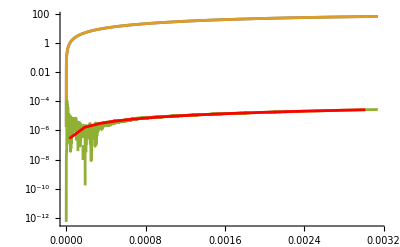

```mathematica
With[{i=1,β=0},Show[LogPlot[{Abs[d2Rint[[2,i]][α,β]Sin[α]],Abs[boxint[[2,i]][α,β]Sin[α]],Abs[(d2Rint[[2,i]][α,β]-boxint[[2,i]][α,β])Sin[α]]},{α,0,π/1000},PlotRange->All,AxesOrigin->{0,0}],Monitor[ListLogPlot[Abs[Table[{α,Abs[(d2RintHP[[2,i]][α,β]-boxint[[2,i]][α,β])Sin[α]]},{α,π/100000,π/1000,5π/100000}]],PlotStyle->Red,Joined->True],N[α/π]]]]
```

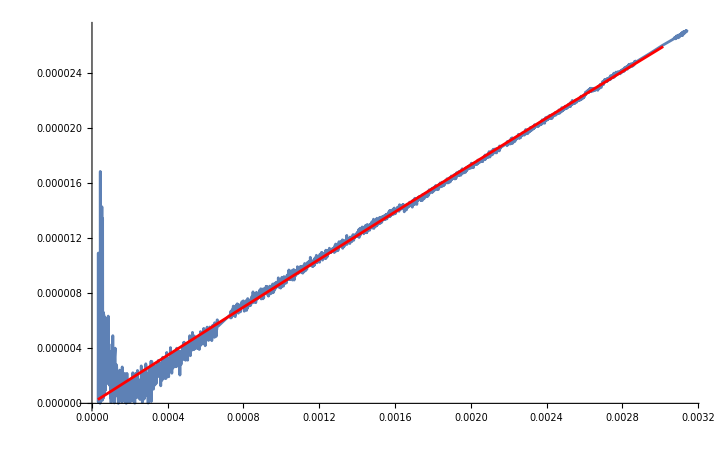

```mathematica
With[{i=1,β=0},Show[Plot[Abs[(d2Rint[[2,i]][α,β]-boxint[[2,i]][α,β])Sin[α]],{α,π/100000,π/1000},AxesOrigin->{0,0}],ListPlot[Monitor[Table[{α,Abs[(d2RintHP[[2,i]][α,β]-boxint[[2,i]][α,β])Sin[α]]},{α,π/100000,π/1000,5π/100000}],N[α/π]],PlotStyle->Red,Joined->True]]]
```

```mathematica
With[{i=1,β=0},Interpolation[Table[{(*Abs[d2Rint[[2,i]][α,β]],Abs[boxint[[2,i]][α,β]]*)α,Abs[d2RintHP[[2,i]][α,β]-boxint[[2,i]][α,β]]},{α,π/100000,π/1000,5π/100000}]]]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[%[α]Sin[α],{α,0,0.003}]
```

3.89421×10^-8

```mathematica
With[{i=1,β=0},NIntegrate[(d2RintHP[[2,i]][α,β]-boxint[[2,i]][α,β])Sin[α],{α,0,π}]]
```

-0.000790998

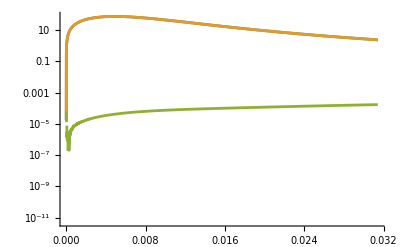
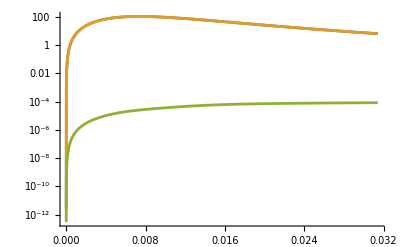
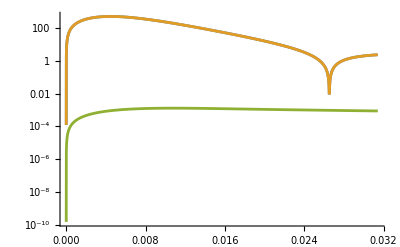
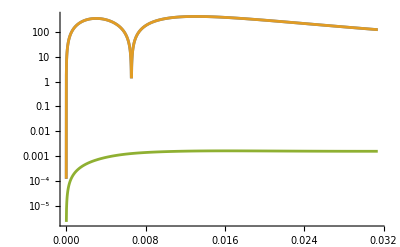
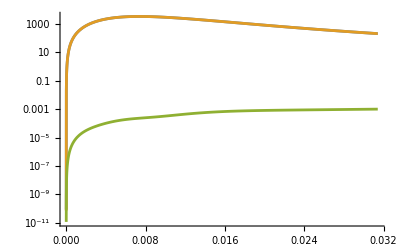
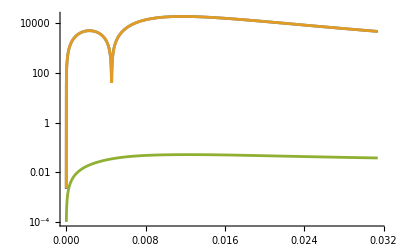
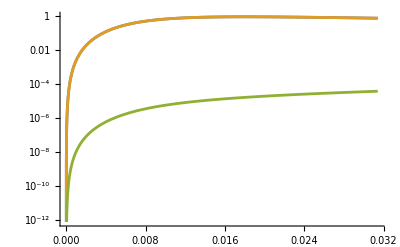
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[LogPlot[{Abs[d2Rint[[2,i]][α,0]Sin[α]],Abs[boxint[[2,i]][α,0]Sin[α]],Abs[(d2Rint[[2,i]][α,0]-boxint[[2,i]][α,0])Sin[α]]},{α,0,π/100}],{i,10}]
```

```mathematica
(*Reap[d2Rminusbox[d2Rint,boxint,1,0,0]]*)
```

```mathematica
(*Reap[d2R[d2Rint,1,0,0]]*)
```

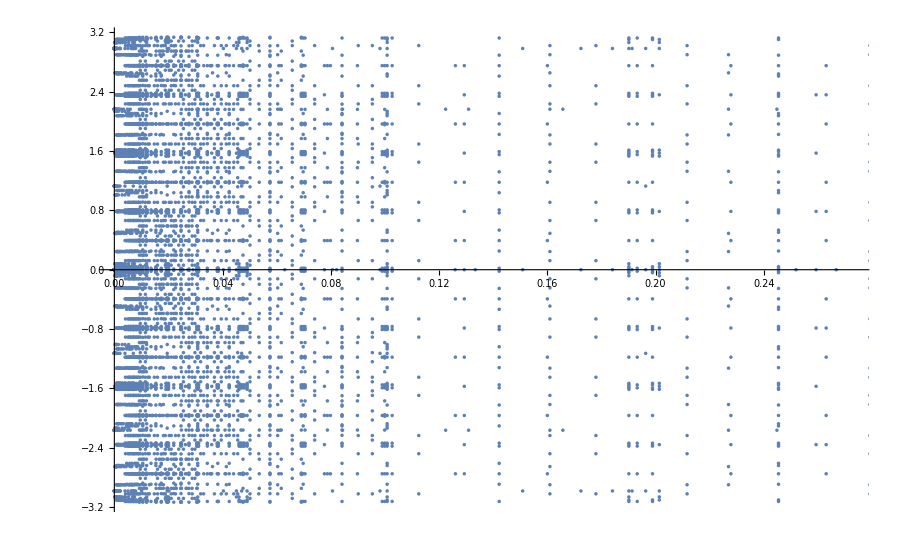

```mathematica
ListPlot[%[[2,1]]]
```